beta functions and fixed points, distinguishing η_TT and η_σ

```mathematica
etas=-(5 g4/(768 π^2)(-6+ηh)-g4/(384 π^2)(-6+ησ)-16 g3/(512 π^2)+1/(512 π^2)g3 ησ+g3/(512 π^2)ηs/.{g3->32 π g3,g4->32 π g4, g5->32 π g5})
```

g3/π-(5 g4 (-6+ηh))/(24 π)-(g3 ηs)/(16 π)+(g4 (-6+ησ))/(12 π)-(g3 ησ)/(16 π)

```mathematica
etah=Ns g3/(768 π^2)-145/(648 π)G4(-6+ηh)+29/(324 π)G4(-6+ησ)-25/(576π)G3(-16+ηh+ησ)+G3/(216 π)(-31+5 ησ)+5 G3/(864 π)(-388+53 ηh)/.{g3->32 π g3,g4->32 π g4, g5->32 π g5}
```

(g3 Ns)/(24 π)-(145 G4 (-6+ηh))/(648 π)+(5 G3 (-388+53 ηh))/(864 π)+(29 G4 (-6+ησ))/(324 π)-(25 G3 (-16+ηh+ησ))/(576 π)+(G3 (-31+5 ησ))/(216 π)

```mathematica
etaσ=g3(8-3 ηs)/(1536 π^2)Ns+G3(136 - 35 ησ)/(432π)+11 G4/(324 π)(-6+ησ)-55 G4(-6+ηh)/(648 π)+5 G3(40-23ηh)/(432 π)+5 G3(-16+ηh+ησ)/(144 π)/.{g3->32 π g3,g4->32 π g4, g5->32 π g5}
```

(5 G3 (40-23 ηh))/(432 π)-(55 G4 (-6+ηh))/(648 π)+(g3 Ns (8-3 ηs))/(48 π)+(G3 (136-35 ησ))/(432 π)+(11 G4 (-6+ησ))/(324 π)+(5 G3 (-16+ηh+ησ))/(144 π)

```mathematica
βg3=Collect[2g3 +g3(2ηs+ηh)+2 Sqrt[g3] 1/Sqrt[32 π]((-g3^(3/2)/(2560 π^2)(-30 +ησ+2 ηs)-g3 Sqrt[G3]/(Sqrt[2] π^(3/2)320)(-30+2 ησ +ηs)+5Sqrt[g3] g4/(2304 π^2)(-16+ησ+ηs)-(19(g5)^(3/2))/(10368 π^2)(-6+ησ)+95 g5^(3/2)/(20736 π^2)(-6+ηh)+g4 Sqrt[G3]/(216 Sqrt[2] π^(3/2))(-8+ησ)+5 g4 Sqrt[G3]/(864 Sqrt[2] π^(3/2))(-8+ηh))/.{g3->32 π g3,g4->32 π g4, g5->32 π g5}),{g5,g3, G3, g4}]
```

√g3 g5^(3/2) (-19/(18 π)+(95 ηh)/(324 π)-(19 ησ)/(162 π))+g3^(3/2) √G3 (3/(4 π)-ηs/(40 π)-ησ/(20 π))+g3^2 (3/(4 π)-ηs/(20 π)-ησ/(40 π))+√g3 √G3 g4 (-2/(3 π)+(5 ηh)/(108 π)+ησ/(27 π))+g3 (2+ηh+2 ηs+g4 (-20/(9 π)+(5 ηs)/(36 π)+(5 ησ)/(36 π)))

```mathematica
etasol=Solve[{ηh==etah, ηs==etas, ησ==etaσ},{ηh,ηs, ησ}][[1]]
```

{ηh→(4 (-5160 g3 G3^2+6751 g3 G3 G4+7758 g3^2 G3 Ns-7839 g3 G3 g4 Ns-7860 g3^2 G4 Ns-162 g3^3 Ns^2+216 g3^2 g4 Ns^2-105408 g3 G3 π-82560 G3^2 π+50112 g3 G4 π+108016 G3 G4 π+2592 g3^2 Ns π-1440 g3 G3 Ns π+13440 g3 G4 Ns π-1686528 G3 π^2+801792 G4 π^2+41472 g3 Ns π^2))/(-4200 g3 G3^2+9530 g3 G3 G4+4095 g3^2 G3 Ns-4410 g3 G3 g4 Ns-3480 g3^2 G4 Ns-54000 g3 G3 π-67200 G3^2 π+47232 g3 G4 π+152480 G3 G4 π-15552 g3^2 Ns π+20736 g3 g4 Ns π+248832 g3 π^2-864000 G3 π^2+755712 G4 π^2+3981312 π^3),ηs→(4 (-37560 g3 G3^2+32280 G3^2 g4+42685 g3 G3 G4+3330 g3^2 G3 Ns-4140 g3 G3 g4 Ns-2100 g3^2 G4 Ns-229824 g3 G3 π+207792 G3 g4 π+169920 g3 G4 π-10368 g3^2 Ns π+5184 g3 g4 Ns π+995328 g3 π^2+746496 g4 π^2))/(-4200 g3 G3^2+9530 g3 G3 G4+4095 g3^2 G3 Ns-4410 g3 G3 g4 Ns-3480 g3^2 G4 Ns-54000 g3 G3 π-67200 G3^2 π+47232 g3 G4 π+152480 G3 G4 π-15552 g3^2 Ns π+20736 g3 g4 Ns π+248832 g3 π^2-864000 G3 π^2+755712 G4 π^2+3981312 π^3),ησ→-((4 (20760 g3 G3^2-4565 g3 G3 G4+13050 g3^2 G3 Ns-9675 g3 G3 g4 Ns-11820 g3^2 G4 Ns+540 g3^2 g4 Ns^2+13824 g3 G3 π+332160 G3^2 π+19008 g3 G4 π-73040 G3 G4 π-51840 g3^2 Ns π-53280 g3 G3 Ns π-46656 g3 g4 Ns π+33600 g3 G4 Ns π+221184 G3 π^2+304128 G4 π^2+165888 g3 Ns π^2))/(4200 g3 G3^2-9530 g3 G3 G4-4095 g3^2 G3 Ns+4410 g3 G3 g4 Ns+3480 g3^2 G4 Ns+54000 g3 G3 π+67200 G3^2 π-47232 g3 G4 π-152480 G3 G4 π+15552 g3^2 Ns π-20736 g3 g4 Ns π-248832 g3 π^2+864000 G3 π^2-755712 G4 π^2-3981312 π^3))}

```mathematica
etasolpert={ηh->(etah/.{ηh->0, ηs->0, ησ->0}),ηs->(etas/.{ηh->0,ηs->0, ησ->0}),ησ->(etaσ/.{ηh->0,ηs->0, ησ->0})}
```

{ηh→-(61 G3)/(36 π)+(29 G4)/(36 π)+(g3 Ns)/(24 π),ηs→g3/π+(3 g4)/(4 π),ησ→(2 G3)/(9 π)+(11 G4)/(36 π)+(g3 Ns)/(6 π)}

```mathematica
βgetapert=βg3/.etasolpert
```

g3 (2+2 (g3/π+(3 g4)/(4 π))+g4 (-20/(9 π)+(5 (g3/π+(3 g4)/(4 π)))/(36 π)+(5 ((2 G3)/(9 π)+(11 G4)/(36 π)+(g3 Ns)/(6 π)))/(36 π))-(61 G3)/(36 π)+(29 G4)/(36 π)+(g3 Ns)/(24 π))+√g3 g5^(3/2) (-19/(18 π)+(95 (-(61 G3)/(36 π)+(29 G4)/(36 π)+(g3 Ns)/(24 π)))/(324 π)-(19 ((2 G3)/(9 π)+(11 G4)/(36 π)+(g3 Ns)/(6 π)))/(162 π))+g3^(3/2) √G3 (3/(4 π)-(g3/π+(3 g4)/(4 π))/(40 π)-((2 G3)/(9 π)+(11 G4)/(36 π)+(g3 Ns)/(6 π))/(20 π))+g3^2 (3/(4 π)-(g3/π+(3 g4)/(4 π))/(20 π)-((2 G3)/(9 π)+(11 G4)/(36 π)+(g3 Ns)/(6 π))/(40 π))+√g3 √G3 g4 (-2/(3 π)+(5 (-(61 G3)/(36 π)+(29 G4)/(36 π)+(g3 Ns)/(24 π)))/(108 π)+((2 G3)/(9 π)+(11 G4)/(36 π)+(g3 Ns)/(6 π))/(27 π))

```mathematica
βgeta=βg3/.etasol
```

g3^2 (3/(4 π)+(20760 g3 G3^2-4565 g3 G3 G4+13050 g3^2 G3 Ns-9675 g3 G3 g4 Ns-11820 g3^2 G4 Ns+540 g3^2 g4 Ns^2+13824 g3 G3 π+332160 G3^2 π+19008 g3 G4 π-73040 G3 G4 π-51840 g3^2 Ns π-53280 g3 G3 Ns π-46656 g3 g4 Ns π+33600 g3 G4 Ns π+221184 G3 π^2+304128 G4 π^2+165888 g3 Ns π^2)/(10 π (4200 g3 G3^2-9530 g3 G3 G4-4095 g3^2 G3 Ns+4410 g3 G3 g4 Ns+3480 g3^2 G4 Ns+54000 g3 G3 π+67200 G3^2 π-47232 g3 G4 π-152480 G3 G4 π+15552 g3^2 Ns π-20736 g3 g4 Ns π-248832 g3 π^2+864000 G3 π^2-755712 G4 π^2-3981312 π^3))-(-37560 g3 G3^2+32280 G3^2 g4+42685 g3 G3 G4+3330 g3^2 G3 Ns-4140 g3 G3 g4 Ns-2100 g3^2 G4 Ns-229824 g3 G3 π+207792 G3 g4 π+169920 g3 G4 π-10368 g3^2 Ns π+5184 g3 g4 Ns π+995328 g3 π^2+746496 g4 π^2)/(5 π (-4200 g3 G3^2+9530 g3 G3 G4+4095 g3^2 G3 Ns-4410 g3 G3 g4 Ns-3480 g3^2 G4 Ns-54000 g3 G3 π-67200 G3^2 π+47232 g3 G4 π+152480 G3 G4 π-15552 g3^2 Ns π+20736 g3 g4 Ns π+248832 g3 π^2-864000 G3 π^2+755712 G4 π^2+3981312 π^3)))+g3^(3/2) √G3 (3/(4 π)+(20760 g3 G3^2-4565 g3 G3 G4+13050 g3^2 G3 Ns-9675 g3 G3 g4 Ns-11820 g3^2 G4 Ns+540 g3^2 g4 Ns^2+13824 g3 G3 π+332160 G3^2 π+19008 g3 G4 π-73040 G3 G4 π-51840 g3^2 Ns π-53280 g3 G3 Ns π-46656 g3 g4 Ns π+33600 g3 G4 Ns π+221184 G3 π^2+304128 G4 π^2+165888 g3 Ns π^2)/(5 π (4200 g3 G3^2-9530 g3 G3 G4-4095 g3^2 G3 Ns+4410 g3 G3 g4 Ns+3480 g3^2 G4 Ns+54000 g3 G3 π+67200 G3^2 π-47232 g3 G4 π-152480 G3 G4 π+15552 g3^2 Ns π-20736 g3 g4 Ns π-248832 g3 π^2+864000 G3 π^2-755712 G4 π^2-3981312 π^3))-(-37560 g3 G3^2+32280 G3^2 g4+42685 g3 G3 G4+3330 g3^2 G3 Ns-4140 g3 G3 g4 Ns-2100 g3^2 G4 Ns-229824 g3 G3 π+207792 G3 g4 π+169920 g3 G4 π-10368 g3^2 Ns π+5184 g3 g4 Ns π+995328 g3 π^2+746496 g4 π^2)/(10 π (-4200 g3 G3^2+9530 g3 G3 G4+4095 g3^2 G3 Ns-4410 g3 G3 g4 Ns-3480 g3^2 G4 Ns-54000 g3 G3 π-67200 G3^2 π+47232 g3 G4 π+152480 G3 G4 π-15552 g3^2 Ns π+20736 g3 g4 Ns π+248832 g3 π^2-864000 G3 π^2+755712 G4 π^2+3981312 π^3)))+√g3 √G3 g4 (-2/(3 π)-(4 (20760 g3 G3^2-4565 g3 G3 G4+13050 g3^2 G3 Ns-9675 g3 G3 g4 Ns-11820 g3^2 G4 Ns+540 g3^2 g4 Ns^2+13824 g3 G3 π+332160 G3^2 π+19008 g3 G4 π-73040 G3 G4 π-51840 g3^2 Ns π-53280 g3 G3 Ns π-46656 g3 g4 Ns π+33600 g3 G4 Ns π+221184 G3 π^2+304128 G4 π^2+165888 g3 Ns π^2))/(27 π (4200 g3 G3^2-9530 g3 G3 G4-4095 g3^2 G3 Ns+4410 g3 G3 g4 Ns+3480 g3^2 G4 Ns+54000 g3 G3 π+67200 G3^2 π-47232 g3 G4 π-152480 G3 G4 π+15552 g3^2 Ns π-20736 g3 g4 Ns π-248832 g3 π^2+864000 G3 π^2-755712 G4 π^2-3981312 π^3))+(5 (-5160 g3 G3^2+6751 g3 G3 G4+7758 g3^2 G3 Ns-7839 g3 G3 g4 Ns-7860 g3^2 G4 Ns-162 g3^3 Ns^2+216 g3^2 g4 Ns^2-105408 g3 G3 π-82560 G3^2 π+50112 g3 G4 π+108016 G3 G4 π+2592 g3^2 Ns π-1440 g3 G3 Ns π+13440 g3 G4 Ns π-1686528 G3 π^2+801792 G4 π^2+41472 g3 Ns π^2))/(27 π (-4200 g3 G3^2+9530 g3 G3 G4+4095 g3^2 G3 Ns-4410 g3 G3 g4 Ns-3480 g3^2 G4 Ns-54000 g3 G3 π-67200 G3^2 π+47232 g3 G4 π+152480 G3 G4 π-15552 g3^2 Ns π+20736 g3 g4 Ns π+248832 g3 π^2-864000 G3 π^2+755712 G4 π^2+3981312 π^3)))+√g3 g5^(3/2) (-19/(18 π)+(38 (20760 g3 G3^2-4565 g3 G3 G4+13050 g3^2 G3 Ns-9675 g3 G3 g4 Ns-11820 g3^2 G4 Ns+540 g3^2 g4 Ns^2+13824 g3 G3 π+332160 G3^2 π+19008 g3 G4 π-73040 G3 G4 π-51840 g3^2 Ns π-53280 g3 G3 Ns π-46656 g3 g4 Ns π+33600 g3 G4 Ns π+221184 G3 π^2+304128 G4 π^2+165888 g3 Ns π^2))/(81 π (4200 g3 G3^2-9530 g3 G3 G4-4095 g3^2 G3 Ns+4410 g3 G3 g4 Ns+3480 g3^2 G4 Ns+54000 g3 G3 π+67200 G3^2 π-47232 g3 G4 π-152480 G3 G4 π+15552 g3^2 Ns π-20736 g3 g4 Ns π-248832 g3 π^2+864000 G3 π^2-755712 G4 π^2-3981312 π^3))+(95 (-5160 g3 G3^2+6751 g3 G3 G4+7758 g3^2 G3 Ns-7839 g3 G3 g4 Ns-7860 g3^2 G4 Ns-162 g3^3 Ns^2+216 g3^2 g4 Ns^2-105408 g3 G3 π-82560 G3^2 π+50112 g3 G4 π+108016 G3 G4 π+2592 g3^2 Ns π-1440 g3 G3 Ns π+13440 g3 G4 Ns π-1686528 G3 π^2+801792 G4 π^2+41472 g3 Ns π^2))/(81 π (-4200 g3 G3^2+9530 g3 G3 G4+4095 g3^2 G3 Ns-4410 g3 G3 g4 Ns-3480 g3^2 G4 Ns-54000 g3 G3 π-67200 G3^2 π+47232 g3 G4 π+152480 G3 G4 π-15552 g3^2 Ns π+20736 g3 g4 Ns π+248832 g3 π^2-864000 G3 π^2+755712 G4 π^2+3981312 π^3)))+g3 (2+(8 (-37560 g3 G3^2+32280 G3^2 g4+42685 g3 G3 G4+3330 g3^2 G3 Ns-4140 g3 G3 g4 Ns-2100 g3^2 G4 Ns-229824 g3 G3 π+207792 G3 g4 π+169920 g3 G4 π-10368 g3^2 Ns π+5184 g3 g4 Ns π+995328 g3 π^2+746496 g4 π^2))/(-4200 g3 G3^2+9530 g3 G3 G4+4095 g3^2 G3 Ns-4410 g3 G3 g4 Ns-3480 g3^2 G4 Ns-54000 g3 G3 π-67200 G3^2 π+47232 g3 G4 π+152480 G3 G4 π-15552 g3^2 Ns π+20736 g3 g4 Ns π+248832 g3 π^2-864000 G3 π^2+755712 G4 π^2+3981312 π^3)+(4 (-5160 g3 G3^2+6751 g3 G3 G4+7758 g3^2 G3 Ns-7839 g3 G3 g4 Ns-7860 g3^2 G4 Ns-162 g3^3 Ns^2+216 g3^2 g4 Ns^2-105408 g3 G3 π-82560 G3^2 π+50112 g3 G4 π+108016 G3 G4 π+2592 g3^2 Ns π-1440 g3 G3 Ns π+13440 g3 G4 Ns π-1686528 G3 π^2+801792 G4 π^2+41472 g3 Ns π^2))/(-4200 g3 G3^2+9530 g3 G3 G4+4095 g3^2 G3 Ns-4410 g3 G3 g4 Ns-3480 g3^2 G4 Ns-54000 g3 G3 π-67200 G3^2 π+47232 g3 G4 π+152480 G3 G4 π-15552 g3^2 Ns π+20736 g3 g4 Ns π+248832 g3 π^2-864000 G3 π^2+755712 G4 π^2+3981312 π^3)+g4 (-20/(9 π)-(5 (20760 g3 G3^2-4565 g3 G3 G4+13050 g3^2 G3 Ns-9675 g3 G3 g4 Ns-11820 g3^2 G4 Ns+540 g3^2 g4 Ns^2+13824 g3 G3 π+332160 G3^2 π+19008 g3 G4 π-73040 G3 G4 π-51840 g3^2 Ns π-53280 g3 G3 Ns π-46656 g3 g4 Ns π+33600 g3 G4 Ns π+221184 G3 π^2+304128 G4 π^2+165888 g3 Ns π^2))/(9 π (4200 g3 G3^2-9530 g3 G3 G4-4095 g3^2 G3 Ns+4410 g3 G3 g4 Ns+3480 g3^2 G4 Ns+54000 g3 G3 π+67200 G3^2 π-47232 g3 G4 π-152480 G3 G4 π+15552 g3^2 Ns π-20736 g3 g4 Ns π-248832 g3 π^2+864000 G3 π^2-755712 G4 π^2-3981312 π^3))+(5 (-37560 g3 G3^2+32280 G3^2 g4+42685 g3 G3 G4+3330 g3^2 G3 Ns-4140 g3 G3 g4 Ns-2100 g3^2 G4 Ns-229824 g3 G3 π+207792 G3 g4 π+169920 g3 G4 π-10368 g3^2 Ns π+5184 g3 g4 Ns π+995328 g3 π^2+746496 g4 π^2))/(9 π (-4200 g3 G3^2+9530 g3 G3 G4+4095 g3^2 G3 Ns-4410 g3 G3 g4 Ns-3480 g3^2 G4 Ns-54000 g3 G3 π-67200 G3^2 π+47232 g3 G4 π+152480 G3 G4 π-15552 g3^2 Ns π+20736 g3 g4 Ns π+248832 g3 π^2-864000 G3 π^2+755712 G4 π^2+3981312 π^3))))

#### approximation 1: treat g_4, g_5, G_EH as parameters (G3=G4), set all couplings except g_3 to zero

```mathematica
βgeta0=βgeta/.{G4->0, G3->0, g4->0, g5->0}
```

2 g3+(3 g3^2)/(4 π)+(g3^2 (-51840 g3^2 Ns π+165888 g3 Ns π^2))/(10 π (15552 g3^2 Ns π-248832 g3 π^2-3981312 π^3))+(8 g3 (-10368 g3^2 Ns π+995328 g3 π^2))/(-15552 g3^2 Ns π+248832 g3 π^2+3981312 π^3)-(g3^2 (-10368 g3^2 Ns π+995328 g3 π^2))/(5 π (-15552 g3^2 Ns π+248832 g3 π^2+3981312 π^3))+(4 g3 (-162 g3^3 Ns^2+2592 g3^2 Ns π+41472 g3 Ns π^2))/(-15552 g3^2 Ns π+248832 g3 π^2+3981312 π^3)

```mathematica
βgeta0pert=βgetapert/.{G4->0, G3->0, g4->0, g5->0, GEH->0}
```

2 g3-g3^3/(20 π^2)-(g3^3 Ns)/(240 π^2)+(11 g3^2)/(4 π)+(g3^2 Ns)/(24 π)

```mathematica
FP=NSolve[(βgeta0/.Ns->1)==0,g3]
```

{{g3→-196.573},{g3→116.224},{g3→-2.13804},{g3→0.}}

```mathematica
theta=-D[βgeta0,g3]/.Ns->1/.FP
```

{26.8895,-86.6154,2.10812,-2.}

```mathematica
ηh/.etasol/.{G4->0, G3->0, g4->0, g5->0}/.Ns->1/.FP
```

{-2.60713,1.54147,-0.0283566,0.}

```mathematica
ησ/.etasol/.{G4->0, G3->0, g4->0, g5->0}/.Ns->1/.FP
```

{11.7743,32.0133,-0.143932,0.}

```mathematica
ηs/.etasol/.{G4->0, G3->0, g4->0, g5->0}/.Ns->1/.FP
```

{5.67746,-11.1787,-0.717186,0.}

```mathematica
FPpert=NSolve[(βgeta0pert/.{Ns->1})==0,g3]
```

{{g3→-2.22025},{g3→0.+0. ⅈ},{g3→164.133}}

```mathematica
thetapert=-D[βgeta0pert,g3]/.Ns->1/.FPpert
```

{2.02705,-2.+0. ⅈ,149.851}

```mathematica
etah/.{ηh->0,ησ->0, ηs->0}/.{G4->0, G3->0, g4->0, g5->0}/.Ns->1/.FPpert
```

{-0.029447,0.+0. ⅈ,2.17688}

```mathematica
etaσ/.{ηh->0,ησ->0, ηs->0}/.{G4->0, G3->0, g4->0, g5->0}/.Ns->1/.FPpert
```

{-0.117788,0.+0. ⅈ,8.70753}

```mathematica
etas/.{ηh->0,ησ->0, ηs->0}/.{G4->0, G3->0, g4->0, g5->0}/.Ns->1/.FPpert
```

{-0.706727,0.+0. ⅈ,52.2452}

#### approximation 1: set g_4=g_3=g_5 set G_3=0=G_4

```mathematica
βgeta0=βgeta/.{G4->0, G3->0}/.{g4->g3, g5->g3}
```

2 g3-(91 g3^2)/(36 π)+(11 g3^2 (540 g3^3 Ns^2-98496 g3^2 Ns π+165888 g3 Ns π^2))/(810 π (-5184 g3^2 Ns π-248832 g3 π^2-3981312 π^3))+(8 g3 (-5184 g3^2 Ns π+1741824 g3 π^2))/(5184 g3^2 Ns π+248832 g3 π^2+3981312 π^3)+(16 g3^2 (-5184 g3^2 Ns π+1741824 g3 π^2))/(45 π (5184 g3^2 Ns π+248832 g3 π^2+3981312 π^3))+(4 g3 (54 g3^3 Ns^2+2592 g3^2 Ns π+41472 g3 Ns π^2))/(5184 g3^2 Ns π+248832 g3 π^2+3981312 π^3)+(95 g3^2 (54 g3^3 Ns^2+2592 g3^2 Ns π+41472 g3 Ns π^2))/(81 π (5184 g3^2 Ns π+248832 g3 π^2+3981312 π^3))

```mathematica
βgeta0pert=βgetapert/.{G4->0, G3->0}/.{g4->g3, g5->g3}
```

2 g3+(7 g3^3)/(45 π^2)+(151 g3^3 Ns)/(12960 π^2)+(35 g3^2)/(36 π)+(g3^2 Ns)/(24 π)

```mathematica
FPs=NSolve[(βgeta0/.{Ns->1}),g3]
```

{{g3→568.023},{g3→75.87},{g3→-57.464},{g3→-5.59289},{g3→0.}}

```mathematica
FPspert=NSolve[(βgeta0pert/.Ns->1),g3]
```

{{g3→-9.52481-5.22787 ⅈ},{g3→-9.52481+5.22787 ⅈ},{g3→0.+0. ⅈ}}

```mathematica
thetas=-D[βgeta0,g3]/.FPs/.{Ns->1}
```

{-263.97,17.9161,-122.749,2.19241,-2.}

```mathematica
ηh/.etasol/.{Ns->1, G3->3, G4->3,g4->2.2, g5->-3}/.FPs
```

{7.95992,-4.46252,-0.775815,-0.934966,-0.830855}

```mathematica
ησ/.etasol/.{Ns->1, G3->3, G4->3,g4->2.2, g5->-3}/.FPs
```

{14.7364,-67.313,13.0719,0.353014,0.746195}

```mathematica
ηs/.etasol/.{Ns->1, G3->3, G4->3,g4->2.2, g5->-3}/.FPs
```

{1.17904,49.0158,13.59,-1.19133,0.689972}

#### approximation 1: g_5=g_3, g_4=g_3, G_EH=g_3

```mathematica
βgeta2=βgeta/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}
```

g3^2 (3/(4 π)+(16195 g3^3-8445 g3^3 Ns+540 g3^3 Ns^2+291952 g3^2 π-118176 g3^2 Ns π+525312 g3 π^2+165888 g3 Ns π^2)/(10 π (-5330 g3^3+3795 g3^3 Ns-78512 g3^2 π-5184 g3^2 Ns π-140544 g3 π^2-3981312 π^3))-(37405 g3^3-2910 g3^3 Ns+147888 g3^2 π-5184 g3^2 Ns π+1741824 g3 π^2)/(5 π (5330 g3^3-3795 g3^3 Ns+78512 g3^2 π+5184 g3^2 Ns π+140544 g3 π^2+3981312 π^3)))+g3^2 (3/(4 π)+(16195 g3^3-8445 g3^3 Ns+540 g3^3 Ns^2+291952 g3^2 π-118176 g3^2 Ns π+525312 g3 π^2+165888 g3 Ns π^2)/(5 π (-5330 g3^3+3795 g3^3 Ns-78512 g3^2 π-5184 g3^2 Ns π-140544 g3 π^2-3981312 π^3))-(37405 g3^3-2910 g3^3 Ns+147888 g3^2 π-5184 g3^2 Ns π+1741824 g3 π^2)/(10 π (5330 g3^3-3795 g3^3 Ns+78512 g3^2 π+5184 g3^2 Ns π+140544 g3 π^2+3981312 π^3)))+g3^2 (-2/(3 π)-(4 (16195 g3^3-8445 g3^3 Ns+540 g3^3 Ns^2+291952 g3^2 π-118176 g3^2 Ns π+525312 g3 π^2+165888 g3 Ns π^2))/(27 π (-5330 g3^3+3795 g3^3 Ns-78512 g3^2 π-5184 g3^2 Ns π-140544 g3 π^2-3981312 π^3))+(5 (1591 g3^3-7941 g3^3 Ns+54 g3^3 Ns^2-29840 g3^2 π+14592 g3^2 Ns π-884736 g3 π^2+41472 g3 Ns π^2))/(27 π (5330 g3^3-3795 g3^3 Ns+78512 g3^2 π+5184 g3^2 Ns π+140544 g3 π^2+3981312 π^3)))+g3^2 (-19/(18 π)+(38 (16195 g3^3-8445 g3^3 Ns+540 g3^3 Ns^2+291952 g3^2 π-118176 g3^2 Ns π+525312 g3 π^2+165888 g3 Ns π^2))/(81 π (-5330 g3^3+3795 g3^3 Ns-78512 g3^2 π-5184 g3^2 Ns π-140544 g3 π^2-3981312 π^3))+(95 (1591 g3^3-7941 g3^3 Ns+54 g3^3 Ns^2-29840 g3^2 π+14592 g3^2 Ns π-884736 g3 π^2+41472 g3 Ns π^2))/(81 π (5330 g3^3-3795 g3^3 Ns+78512 g3^2 π+5184 g3^2 Ns π+140544 g3 π^2+3981312 π^3)))+g3 (2+(8 (37405 g3^3-2910 g3^3 Ns+147888 g3^2 π-5184 g3^2 Ns π+1741824 g3 π^2))/(5330 g3^3-3795 g3^3 Ns+78512 g3^2 π+5184 g3^2 Ns π+140544 g3 π^2+3981312 π^3)+(4 (1591 g3^3-7941 g3^3 Ns+54 g3^3 Ns^2-29840 g3^2 π+14592 g3^2 Ns π-884736 g3 π^2+41472 g3 Ns π^2))/(5330 g3^3-3795 g3^3 Ns+78512 g3^2 π+5184 g3^2 Ns π+140544 g3 π^2+3981312 π^3)+g3 (-20/(9 π)-(5 (16195 g3^3-8445 g3^3 Ns+540 g3^3 Ns^2+291952 g3^2 π-118176 g3^2 Ns π+525312 g3 π^2+165888 g3 Ns π^2))/(9 π (-5330 g3^3+3795 g3^3 Ns-78512 g3^2 π-5184 g3^2 Ns π-140544 g3 π^2-3981312 π^3))+(5 (37405 g3^3-2910 g3^3 Ns+147888 g3^2 π-5184 g3^2 Ns π+1741824 g3 π^2))/(9 π (5330 g3^3-3795 g3^3 Ns+78512 g3^2 π+5184 g3^2 Ns π+140544 g3 π^2+3981312 π^3))))

```mathematica
βgetapert2=Expand[βgetapert/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}]
```

2 g3-(143 g3^3)/(720 π^2)+(37 g3^3 Ns)/(3240 π^2)+g3^2/(6 π)+(g3^2 Ns)/(24 π)

```mathematica
FPs=NSolve[(βgeta2/.{Ns->1}),g3]
```

{{g3→53.393},{g3→1.15771+16.074 ⅈ},{g3→1.15771-16.074 ⅈ},{g3→-13.8815},{g3→0.}}

```mathematica
thetas=-D[βgeta2,g3]/.FPs/.Ns->1
```

{11.6544,12.9453+0.220317 ⅈ,12.9453-0.220317 ⅈ,3.84995,-2.}

```mathematica
ηh/.etasol/.{G3->GEH, G4->GEH, g4->g3}/.Ns->1/.GEH->g3/.FPs
```

{-5.21458,-2.4841-6.68854 ⅈ,-2.4841+6.68854 ⅈ,3.26741,0.}

```mathematica
ηs/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}/.Ns->1/.GEH->g3/.FPs
```

{25.2266,-3.31389+12.3627 ⅈ,-3.31389-12.3627 ⅈ,-6.48804,0.}

```mathematica
ησ/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}/.Ns->1/.GEH->g3/.FPs
```

{10.7811,-5.6292+9.44139 ⅈ,-5.6292-9.44139 ⅈ,-0.309741,0.}

```mathematica
FPspert=NSolve[(βgetapert2/.{Ns->1}),g3]
```

{{g3→-8.66839},{g3→0.+0. ⅈ},{g3→12.1648}}

```mathematica
thetaspert=-D[βgetapert2,g3]/.FPspert/.Ns->1
```

{3.42516,-2.+0. ⅈ,4.8067}

```mathematica
etah/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}/.{ηh->0, ηs->0, Ns->1, GEH->g3, ησ->0}/.FPspert
```

{2.33769,0.+0. ⅈ,-3.2806}

```mathematica
etas/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}/.{ηh->0, ηs->0, Ns->1, GEH->g3, ησ->0}/.FPspert
```

{-4.82866,0.+0. ⅈ,6.77631}

```mathematica
etaσ/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}/.{ηh->0, ηs->0, Ns->1, GEH->g3, ησ->0}/.FPspert
```

{-1.91614,0.+0. ⅈ,2.68901}

#### approximation 1: g_5=g_3, g_4=g_3, G_EH=g_3+ background Newton coupling

```mathematica
βgeta2=βgeta/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}
```

g3^2 (3/(4 π)+(16195 g3^3-8445 g3^3 Ns+540 g3^3 Ns^2+291952 g3^2 π-118176 g3^2 Ns π+525312 g3 π^2+165888 g3 Ns π^2)/(10 π (-5330 g3^3+3795 g3^3 Ns-78512 g3^2 π-5184 g3^2 Ns π-140544 g3 π^2-3981312 π^3))-(37405 g3^3-2910 g3^3 Ns+147888 g3^2 π-5184 g3^2 Ns π+1741824 g3 π^2)/(5 π (5330 g3^3-3795 g3^3 Ns+78512 g3^2 π+5184 g3^2 Ns π+140544 g3 π^2+3981312 π^3)))+g3^2 (3/(4 π)+(16195 g3^3-8445 g3^3 Ns+540 g3^3 Ns^2+291952 g3^2 π-118176 g3^2 Ns π+525312 g3 π^2+165888 g3 Ns π^2)/(5 π (-5330 g3^3+3795 g3^3 Ns-78512 g3^2 π-5184 g3^2 Ns π-140544 g3 π^2-3981312 π^3))-(37405 g3^3-2910 g3^3 Ns+147888 g3^2 π-5184 g3^2 Ns π+1741824 g3 π^2)/(10 π (5330 g3^3-3795 g3^3 Ns+78512 g3^2 π+5184 g3^2 Ns π+140544 g3 π^2+3981312 π^3)))+g3^2 (-2/(3 π)-(4 (16195 g3^3-8445 g3^3 Ns+540 g3^3 Ns^2+291952 g3^2 π-118176 g3^2 Ns π+525312 g3 π^2+165888 g3 Ns π^2))/(27 π (-5330 g3^3+3795 g3^3 Ns-78512 g3^2 π-5184 g3^2 Ns π-140544 g3 π^2-3981312 π^3))+(5 (1591 g3^3-7941 g3^3 Ns+54 g3^3 Ns^2-29840 g3^2 π+14592 g3^2 Ns π-884736 g3 π^2+41472 g3 Ns π^2))/(27 π (5330 g3^3-3795 g3^3 Ns+78512 g3^2 π+5184 g3^2 Ns π+140544 g3 π^2+3981312 π^3)))+g3^2 (-19/(18 π)+(38 (16195 g3^3-8445 g3^3 Ns+540 g3^3 Ns^2+291952 g3^2 π-118176 g3^2 Ns π+525312 g3 π^2+165888 g3 Ns π^2))/(81 π (-5330 g3^3+3795 g3^3 Ns-78512 g3^2 π-5184 g3^2 Ns π-140544 g3 π^2-3981312 π^3))+(95 (1591 g3^3-7941 g3^3 Ns+54 g3^3 Ns^2-29840 g3^2 π+14592 g3^2 Ns π-884736 g3 π^2+41472 g3 Ns π^2))/(81 π (5330 g3^3-3795 g3^3 Ns+78512 g3^2 π+5184 g3^2 Ns π+140544 g3 π^2+3981312 π^3)))+g3 (2+(8 (37405 g3^3-2910 g3^3 Ns+147888 g3^2 π-5184 g3^2 Ns π+1741824 g3 π^2))/(5330 g3^3-3795 g3^3 Ns+78512 g3^2 π+5184 g3^2 Ns π+140544 g3 π^2+3981312 π^3)+(4 (1591 g3^3-7941 g3^3 Ns+54 g3^3 Ns^2-29840 g3^2 π+14592 g3^2 Ns π-884736 g3 π^2+41472 g3 Ns π^2))/(5330 g3^3-3795 g3^3 Ns+78512 g3^2 π+5184 g3^2 Ns π+140544 g3 π^2+3981312 π^3)+g3 (-20/(9 π)-(5 (16195 g3^3-8445 g3^3 Ns+540 g3^3 Ns^2+291952 g3^2 π-118176 g3^2 Ns π+525312 g3 π^2+165888 g3 Ns π^2))/(9 π (-5330 g3^3+3795 g3^3 Ns-78512 g3^2 π-5184 g3^2 Ns π-140544 g3 π^2-3981312 π^3))+(5 (37405 g3^3-2910 g3^3 Ns+147888 g3^2 π-5184 g3^2 Ns π+1741824 g3 π^2))/(9 π (5330 g3^3-3795 g3^3 Ns+78512 g3^2 π+5184 g3^2 Ns π+140544 g3 π^2+3981312 π^3))))

```mathematica
FPs=NSolve[(βgeta2/.{Ns->1}),g3]
```

{{g3→53.393},{g3→1.15771+16.074 ⅈ},{g3→1.15771-16.074 ⅈ},{g3→-13.8815},{g3→0.}}

```mathematica
(ησ/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3})/.{Ns->1}/.FPs[[4]]
```

-0.309741

```mathematica
(ηh/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3})/.{Ns->1}/.FPs[[4]]
```

3.26741

```mathematica
(ηs/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3})/.{Ns->1}/.FPs[[4]]
```

-6.48804

```mathematica
βGbackground4=2 G -G^2/π (15/8-5/18(ηh/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3})+(ησ/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3})/24) +Ns G^2/(24 π)(4-ηs/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3})/.Ns->1/.FPs[[4]]
```

2 G-0.164718 G^2

```mathematica
FP=NSolve[βGbackground4==0,G]
```

{{G→0.+0. ⅈ},{G→12.1419}}

```mathematica
-D[βGbackground4,G]/.FP
```

{-2.+0. ⅈ,2.}

```mathematica
βGbackground1=2 G +G^2 (-15/(8π)-17/(72 π)ηh/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}) +Ns G^2/(24 π)(4-ηs/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3})/.Ns->1/.FPs[[1]]
```

2 G-0.486449 G^2

```mathematica
FP=NSolve[βGbackground1==0,G]
```

{{G→0.},{G→4.11143}}

```mathematica
-D[βGbackground1,G]/.FP
```

{-2.,2.}

## Dependence on Ns

#### approximation 1: treat g_4, g_5, G_EH as parameters (G3=G4), set all couplings except g_3 to zero

```mathematica
βgeta0=βgeta/.{G4->0, G3->0, g4->0, g5->0}
```

2 g3+(3 g3^2)/(4 π)+(g3^2 (-51840 g3^2 Ns π+165888 g3 Ns π^2))/(10 π (15552 g3^2 Ns π-248832 g3 π^2-3981312 π^3))+(8 g3 (-10368 g3^2 Ns π+995328 g3 π^2))/(-15552 g3^2 Ns π+248832 g3 π^2+3981312 π^3)-(g3^2 (-10368 g3^2 Ns π+995328 g3 π^2))/(5 π (-15552 g3^2 Ns π+248832 g3 π^2+3981312 π^3))+(4 g3 (-162 g3^3 Ns^2+2592 g3^2 Ns π+41472 g3 Ns π^2))/(-15552 g3^2 Ns π+248832 g3 π^2+3981312 π^3)

```mathematica
βgeta0pert=βgetapert/.{G4->0, G3->0, g4->0, g5->0, GEH->0}
```

2 g3-g3^3/(20 π^2)-(g3^3 Ns)/(240 π^2)+(11 g3^2)/(4 π)+(g3^2 Ns)/(24 π)

```mathematica
Solve[βgeta0pert==0,g3]
```

{{g3→0},{g3→((330+5 Ns-√5 √(22932+756 Ns+5 Ns^2)) π)/(12+Ns)},{g3→((330+5 Ns+√5 √(22932+756 Ns+5 Ns^2)) π)/(12+Ns)}}

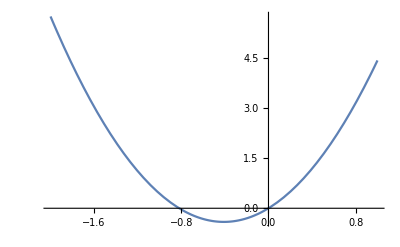

```mathematica
Plot[2 g3+(7 g3^2)/(2 π)+(g3^2 Ns)/(24 π)/.Ns->100,{g3,-2,1}]
```

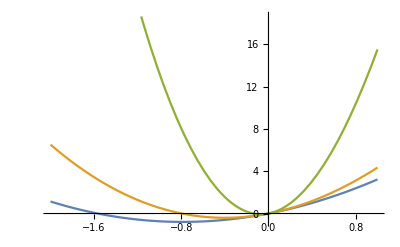

```mathematica
Plot[{(βgeta0pert/.Ns->10),(βgeta0pert/.Ns->100),(βgeta0pert/.Ns->1000)},{g3,-2,1}]
```

```mathematica
FPs=Table[NSolve[(βgeta0/.Ns->i)==0,g3],{i,1,200}]
```

{{{g3→-152.468},{g3→100.464},{g3→-1.70368},{g3→0.}},{{g3→-110.579},{g3→65.8566},{g3→-1.67689},{g3→0.}},{{g3→-91.4229},{g3→50.6815},{g3→-1.65119},{g3→0.}},{{g3→-79.592},{g3→41.8057},{g3→-1.6265},{g3→0.}},{{g3→-71.2449},{g3→35.8782},{g3→-1.60274},{g3→0.}},{{g3→-64.8973},{g3→31.5991},{g3→-1.57987},{g3→0.}},{{g3→-59.8342},{g3→28.3464},{g3→-1.55782},{g3→0.}},{{g3→-55.6602},{g3→25.7808},{g3→-1.53655},{g3→0.}},{{g3→-52.1357},{g3→23.7},{g3→-1.51599},{g3→0.}},{{g3→-49.1046},{g3→21.975},{g3→-1.49613},{g3→0.}},{{g3→-46.4603},{g3→20.5196},{g3→-1.4769},{g3→0.}},{{g3→-44.1264},{g3→19.2738},{g3→-1.45829},{g3→0.}},{{g3→-42.0467},{g3→18.1943},{g3→-1.44025},{g3→0.}},{{g3→-40.1786},{g3→17.2492},{g3→-1.42275},{g3→0.}},{{g3→-38.4891},{g3→16.4142},{g3→-1.40578},{g3→0.}},{{g3→-36.9519},{g3→15.6707},{g3→-1.38929},{g3→0.}},{{g3→-35.546},{g3→15.0042},{g3→-1.37327},{g3→0.}},{{g3→-34.2543},{g3→14.403},{g3→-1.3577},{g3→0.}},{{g3→-33.0628},{g3→13.8577},{g3→-1.34255},{g3→0.}},{{g3→-31.9595},{g3→13.3606},{g3→-1.3278},{g3→0.}},{{g3→-30.9346},{g3→12.9056},{g3→-1.31344},{g3→0.}},{{g3→-29.9797},{g3→12.4873},{g3→-1.29945},{g3→0.}},{{g3→-29.0875},{g3→12.1014},{g3→-1.28582},{g3→0.}},{{g3→-28.2517},{g3→11.7442},{g3→-1.27252},{g3→0.}},{{g3→-27.4671},{g3→11.4124},{g3→-1.25954},{g3→0.}},{{g3→-26.7289},{g3→11.1034},{g3→-1.24688},{g3→0.}},{{g3→-26.0329},{g3→10.8149},{g3→-1.23451},{g3→0.}},{{g3→-25.3756},{g3→10.5448},{g3→-1.22243},{g3→0.}},{{g3→-24.7536},{g3→10.2914},{g3→-1.21063},{g3→0.}},{{g3→-24.1642},{g3→-1.19909},{g3→0.}},{{g3→-23.6048},{g3→9.82857},{g3→-1.1878},{g3→0.}},{{g3→-23.0731},{g3→9.61661},{g3→-1.17676},{g3→0.}},{{g3→-22.567},{g3→9.41617},{g3→-1.16596},{g3→0.}},{{g3→-22.0846},{g3→9.2263},{g3→-1.15539},{g3→0.}},{{g3→-21.6244},{g3→9.04616},{g3→-1.14503},{g3→0.}},{{g3→-21.1848},{g3→8.875},{g3→-1.13489},{g3→0.}},{{g3→-20.7643},{g3→8.71214},{g3→-1.12496},{g3→0.}},{{g3→-20.3619},{g3→8.55696},{g3→-1.11522},{g3→0.}},{{g3→-19.9762},{g3→8.40892},{g3→-1.10567},{g3→0.}},{{g3→-19.6063},{g3→8.26752},{g3→-1.09632},{g3→0.}},{{g3→-19.2512},{g3→8.1323},{g3→-1.08714},{g3→0.}},{{g3→-18.9099},{g3→8.00286},{g3→-1.07813},{g3→0.}},{{g3→-18.5818},{g3→7.87882},{g3→-1.06929},{g3→0.}},{{g3→-18.266},{g3→7.75983},{g3→-1.06062},{g3→0.}},{{g3→-17.9618},{g3→7.64558},{g3→-1.05211},{g3→0.}},{{g3→-17.6687},{g3→7.53578},{g3→-1.04375},{g3→0.}},{{g3→-17.3859},{g3→7.43016},{g3→-1.03554},{g3→0.}},{{g3→-17.113},{g3→7.32848},{g3→-1.02747},{g3→0.}},{{g3→-16.8494},{g3→7.23052},{g3→-1.01954},{g3→0.}},{{g3→-16.5947},{g3→7.13607},{g3→-1.01175},{g3→0.}},{{g3→-16.3484},{g3→7.04493},{g3→-1.0041},{g3→0.}},{{g3→-16.1101},{g3→6.95692},{g3→-0.99657},{g3→0.}},{{g3→-15.8794},{g3→6.87188},{g3→-0.989169},{g3→0.}},{{g3→-15.656},{g3→6.78966},{g3→-0.981889},{g3→0.}},{{g3→-15.4394},{g3→6.7101},{g3→-0.974729},{g3→0.}},{{g3→-15.2295},{g3→6.63308},{g3→-0.967684},{g3→0.}},{{g3→-15.0258},{g3→6.55848},{g3→-0.960752},{g3→0.}},{{g3→-14.8281},{g3→6.48617},{g3→-0.953929},{g3→0.}},{{g3→-14.6362},{g3→6.41604},{g3→-0.947214},{g3→0.}},{{g3→-14.4497},{g3→6.34799},{g3→-0.940602},{g3→0.}},{{g3→-14.2685},{g3→6.28194},{g3→-0.934093},{g3→0.}},{{g3→-14.0923},{g3→6.21778},{g3→-0.927682},{g3→0.}},{{g3→-13.921},{g3→6.15543},{g3→-0.921368},{g3→0.}},{{g3→-13.7543},{g3→6.09481},{g3→-0.915148},{g3→0.}},{{g3→-13.592},{g3→6.03585},{g3→-0.909021},{g3→0.}},{{g3→-13.4339},{g3→5.97848},{g3→-0.902983},{g3→0.}},{{g3→-13.28},{g3→5.92263},{g3→-0.897032},{g3→0.}},{{g3→-13.13},{g3→5.86824},{g3→-0.891168},{g3→0.}},{{g3→-12.9838},{g3→5.81524},{g3→-0.885387},{g3→0.}},{{g3→-12.8412},{g3→5.76359},{g3→-0.879688},{g3→0.}},{{g3→-12.7021},{g3→5.71323},{g3→-0.874068},{g3→0.}},{{g3→-12.5664},{g3→5.6641},{g3→-0.868527},{g3→0.}},{{g3→-12.4339},{g3→5.61617},{g3→-0.863062},{g3→0.}},{{g3→-12.3046},{g3→5.56938},{g3→-0.857672},{g3→0.}},{{g3→-12.1783},{g3→5.5237},{g3→-0.852355},{g3→0.}},{{g3→-12.0549},{g3→5.47908},{g3→-0.847109},{g3→0.}},{{g3→-11.9343},{g3→5.43548},{g3→-0.841933},{g3→0.}},{{g3→-11.8164},{g3→5.39287},{g3→-0.836825},{g3→0.}},{{g3→-11.7012},{g3→5.35121},{g3→-0.831785},{g3→0.}},{{g3→-11.5885},{g3→5.31047},{g3→-0.82681},{g3→0.}},{{g3→-11.4782},{g3→5.27061},{g3→-0.821899},{g3→0.}},{{g3→-11.3704},{g3→5.23161},{g3→-0.817051},{g3→0.}},{{g3→-11.2648},{g3→5.19344},{g3→-0.812264},{g3→0.}},{{g3→-11.1614},{g3→5.15606},{g3→-0.807538},{g3→0.}},{{g3→-11.0602},{g3→5.11946},{g3→-0.802871},{g3→0.}},{{g3→-10.9611},{g3→5.08361},{g3→-0.798262},{g3→0.}},{{g3→-10.864},{g3→5.04848},{g3→-0.79371},{g3→0.}},{{g3→-10.7689},{g3→5.01405},{g3→-0.789214},{g3→0.}},{{g3→-10.6756},{g3→4.9803},{g3→-0.784772},{g3→0.}},{{g3→-10.5842},{g3→4.94721},{g3→-0.780383},{g3→0.}},{{g3→-10.4946},{g3→4.91476},{g3→-0.776047},{g3→0.}},{{g3→-10.4068},{g3→4.88292},{g3→-0.771763},{g3→0.}},{{g3→-10.3206},{g3→4.85168},{g3→-0.767529},{g3→0.}},{{g3→-10.236},{g3→4.82103},{g3→-0.763345},{g3→0.}},{{g3→-10.153},{g3→4.79093},{g3→-0.759209},{g3→0.}},{{g3→-10.0716},{g3→4.76139},{g3→-0.755122},{g3→0.}},{{g3→-9.99167},{g3→4.73237},{g3→-0.751081},{g3→0.}},{{g3→-9.9132},{g3→4.70388},{g3→-0.747086},{g3→0.}},{{g3→-9.83615},{g3→4.67588},{g3→-0.743136},{g3→0.}},{{g3→-9.76047},{g3→4.64838},{g3→-0.739231},{g3→0.}},{{g3→-9.68614},{g3→4.62135},{g3→-0.735369},{g3→0.}},{{g3→-9.61311},{g3→4.59478},{g3→-0.731551},{g3→0.}},{{g3→-9.54136},{g3→4.56865},{g3→-0.727774},{g3→0.}},{{g3→-9.47084},{g3→4.54297},{g3→-0.724039},{g3→0.}},{{g3→-9.40153},{g3→4.51771},{g3→-0.720344},{g3→0.}},{{g3→-9.33339},{g3→4.49286},{g3→-0.71669},{g3→0.}},{{g3→-9.26639},{g3→4.46842},{g3→-0.713074},{g3→0.}},{{g3→-9.20051},{g3→4.44437},{g3→-0.709498},{g3→0.}},{{g3→-9.13572},{g3→4.42071},{g3→-0.705959},{g3→0.}},{{g3→-9.07199},{g3→4.39741},{g3→-0.702457},{g3→0.}},{{g3→-9.00929},{g3→4.37448},{g3→-0.698993},{g3→0.}},{{g3→-8.9476},{g3→4.35191},{g3→-0.695564},{g3→0.}},{{g3→-8.88689},{g3→4.32968},{g3→-0.692171},{g3→0.}},{{g3→-8.82714},{g3→4.30778},{g3→-0.688813},{g3→0.}},{{g3→-8.76833},{g3→4.28622},{g3→-0.685489},{g3→0.}},{{g3→-8.71044},{g3→4.26498},{g3→-0.682199},{g3→0.}},{{g3→-8.65344},{g3→4.24405},{g3→-0.678942},{g3→0.}},{{g3→-8.59731},{g3→4.22343},{g3→-0.675718},{g3→0.}},{{g3→-8.54203},{g3→4.2031},{g3→-0.672526},{g3→0.}},{{g3→-8.48758},{g3→4.18307},{g3→-0.669366},{g3→0.}},{{g3→-8.43395},{g3→4.16333},{g3→-0.666237},{g3→0.}},{{g3→-8.38111},{g3→4.14386},{g3→-0.663139},{g3→0.}},{{g3→-8.32905},{g3→4.12466},{g3→-0.660071},{g3→0.}},{{g3→-8.27775},{g3→4.10574},{g3→-0.657033},{g3→0.}},{{g3→-8.22719},{g3→4.08707},{g3→-0.654024},{g3→0.}},{{g3→-8.17736},{g3→4.06865},{g3→-0.651045},{g3→0.}},{{g3→-8.12824},{g3→4.05049},{g3→-0.648093},{g3→0.}},{{g3→-8.07982},{g3→4.03257},{g3→-0.64517},{g3→0.}},{{g3→-8.03207},{g3→4.01489},{g3→-0.642274},{g3→0.}},{{g3→-7.985},{g3→3.99744},{g3→-0.639406},{g3→0.}},{{g3→-7.93857},{g3→3.98022},{g3→-0.636564},{g3→0.}},{{g3→-7.89278},{g3→3.96322},{g3→-0.633749},{g3→0.}},{{g3→-7.84762},{g3→3.94644},{g3→-0.63096},{g3→0.}},{{g3→-7.80307},{g3→3.92988},{g3→-0.628197},{g3→0.}},{{g3→-7.75911},{g3→3.91352},{g3→-0.625459},{g3→0.}},{{g3→-7.71575},{g3→3.89737},{g3→-0.622745},{g3→0.}},{{g3→-7.67295},{g3→3.88142},{g3→-0.620057},{g3→0.}},{{g3→-7.63073},{g3→3.86568},{g3→-0.617392},{g3→0.}},{{g3→-7.58905},{g3→3.85012},{g3→-0.614752},{g3→0.}},{{g3→-7.54792},{g3→3.83475},{g3→-0.612135},{g3→0.}},{{g3→-7.50731},{g3→3.81957},{g3→-0.609541},{g3→0.}},{{g3→-7.46723},{g3→3.80457},{g3→-0.60697},{g3→0.}},{{g3→-7.42765},{g3→3.78975},{g3→-0.604422},{g3→0.}},{{g3→-7.38858},{g3→3.77511},{g3→-0.601896},{g3→0.}},{{g3→-7.35},{g3→3.76064},{g3→-0.599393},{g3→0.}},{{g3→-7.31189},{g3→3.74633},{g3→-0.59691},{g3→0.}},{{g3→-7.27426},{g3→3.73219},{g3→-0.594449},{g3→0.}},{{g3→-7.23709},{g3→3.71822},{g3→-0.59201},{g3→0.}},{{g3→-7.20038},{g3→3.7044},{g3→-0.589591},{g3→0.}},{{g3→-7.16411},{g3→3.69074},{g3→-0.587193},{g3→0.}},{{g3→-7.12828},{g3→3.67723},{g3→-0.584814},{g3→0.}},{{g3→-7.09288},{g3→3.66388},{g3→-0.582456},{g3→0.}},{{g3→-7.0579},{g3→3.65067},{g3→-0.580118},{g3→0.}},{{g3→-7.02334},{g3→3.63761},{g3→-0.577799},{g3→0.}},{{g3→-6.98918},{g3→3.62469},{g3→-0.5755},{g3→0.}},{{g3→-6.95542},{g3→3.61191},{g3→-0.573219},{g3→0.}},{{g3→-6.92205},{g3→3.59926},{g3→-0.570957},{g3→0.}},{{g3→-6.88907},{g3→3.58676},{g3→-0.568714},{g3→0.}},{{g3→-6.85646},{g3→3.57438},{g3→-0.566489},{g3→0.}},{{g3→-6.82423},{g3→3.56214},{g3→-0.564282},{g3→0.}},{{g3→-6.79236},{g3→3.55003},{g3→-0.562093},{g3→0.}},{{g3→-6.76086},{g3→3.53804},{g3→-0.559921},{g3→0.}},{{g3→-6.7297},{g3→3.52617},{g3→-0.557767},{g3→0.}},{{g3→-6.69889},{g3→3.51443},{g3→-0.55563},{g3→0.}},{{g3→-6.66842},{g3→3.50281},{g3→-0.55351},{g3→0.}},{{g3→-6.63829},{g3→3.49131},{g3→-0.551407},{g3→0.}},{{g3→-6.60849},{g3→3.47992},{g3→-0.54932},{g3→0.}},{{g3→-6.57901},{g3→3.46864},{g3→-0.54725},{g3→0.}},{{g3→-6.54985},{g3→3.45748},{g3→-0.545195},{g3→0.}},{{g3→-6.521},{g3→3.44643},{g3→-0.543157},{g3→0.}},{{g3→-6.49246},{g3→3.43549},{g3→-0.541134},{g3→0.}},{{g3→-6.46422},{g3→3.42465},{g3→-0.539127},{g3→0.}},{{g3→-6.43628},{g3→3.41392},{g3→-0.537136},{g3→0.}},{{g3→-6.40864},{g3→3.4033},{g3→-0.535159},{g3→0.}},{{g3→-6.38128},{g3→3.39277},{g3→-0.533198},{g3→0.}},{{g3→-6.35421},{g3→3.38235},{g3→-0.531251},{g3→0.}},{{g3→-6.32742},{g3→3.37202},{g3→-0.529319},{g3→0.}},{{g3→-6.3009},{g3→3.3618},{g3→-0.527402},{g3→0.}},{{g3→-6.27465},{g3→3.35166},{g3→-0.525498},{g3→0.}},{{g3→-6.24867},{g3→3.34163},{g3→-0.523609},{g3→0.}},{{g3→-6.22295},{g3→3.33168},{g3→-0.521735},{g3→0.}},{{g3→-6.19749},{g3→3.32183},{g3→-0.519873},{g3→0.}},{{g3→-6.17229},{g3→3.31206},{g3→-0.518026},{g3→0.}},{{g3→-6.14733},{g3→3.30239},{g3→-0.516192},{g3→0.}},{{g3→-6.12262},{g3→3.2928},{g3→-0.514372},{g3→0.}},{{g3→-6.09816},{g3→3.2833},{g3→-0.512564},{g3→0.}},{{g3→-6.07393},{g3→3.27388},{g3→-0.51077},{g3→0.}},{{g3→-6.04994},{g3→3.26455},{g3→-0.508989},{g3→0.}},{{g3→-6.02618},{g3→3.2553},{g3→-0.50722},{g3→0.}},{{g3→-6.00265},{g3→3.24613},{g3→-0.505464},{g3→0.}},{{g3→-5.97934},{g3→3.23704},{g3→-0.503721},{g3→0.}},{{g3→-5.95626},{g3→3.22803},{g3→-0.50199},{g3→0.}},{{g3→-5.9334},{g3→3.2191},{g3→-0.500271},{g3→0.}},{{g3→-5.91075},{g3→3.21024},{g3→-0.498565},{g3→0.}},{{g3→-5.88831},{g3→3.20146},{g3→-0.49687},{g3→0.}},{{g3→-5.86608},{g3→3.19276},{g3→-0.495187},{g3→0.}},{{g3→-5.84406},{g3→3.18413},{g3→-0.493516},{g3→0.}},{{g3→-5.82224},{g3→3.17557},{g3→-0.491856},{g3→0.}},{{g3→-5.80063},{g3→3.16708},{g3→-0.490208},{g3→0.}},{{g3→-5.77921},{g3→3.15866},{g3→-0.488571},{g3→0.}}}

```mathematica
FPplottab=Table[Sort[g3/.FPs[[i]],#1<#2&],{i,1,Length[FPs]}]
```

{{-152.468,-1.70368,0.,100.464},{-110.579,-1.67689,0.,65.8566},{-91.4229,-1.65119,0.,50.6815},{-79.592,-1.6265,0.,41.8057},{-71.2449,-1.60274,0.,35.8782},{-64.8973,-1.57987,0.,31.5991},{-59.8342,-1.55782,0.,28.3464},{-55.6602,-1.53655,0.,25.7808},{-52.1357,-1.51599,0.,23.7},{-49.1046,-1.49613,0.,21.975},{-46.4603,-1.4769,0.,20.5196},{-44.1264,-1.45829,0.,19.2738},{-42.0467,-1.44025,0.,18.1943},{-40.1786,-1.42275,0.,17.2492},{-38.4891,-1.40578,0.,16.4142},{-36.9519,-1.38929,0.,15.6707},{-35.546,-1.37327,0.,15.0042},{-34.2543,-1.3577,0.,14.403},{-33.0628,-1.34255,0.,13.8577},{-31.9595,-1.3278,0.,13.3606},{-30.9346,-1.31344,0.,12.9056},{-29.9797,-1.29945,0.,12.4873},{-29.0875,-1.28582,0.,12.1014},{-28.2517,-1.27252,0.,11.7442},{-27.4671,-1.25954,0.,11.4124},{-26.7289,-1.24688,0.,11.1034},{-26.0329,-1.23451,0.,10.8149},{-25.3756,-1.22243,0.,10.5448},{-24.7536,-1.21063,0.,10.2914},{-24.1642,-1.19909,0.},{-23.6048,-1.1878,0.,9.82857},{-23.0731,-1.17676,0.,9.61661},{-22.567,-1.16596,0.,9.41617},{-22.0846,-1.15539,0.,9.2263},{-21.6244,-1.14503,0.,9.04616},{-21.1848,-1.13489,0.,8.875},{-20.7643,-1.12496,0.,8.71214},{-20.3619,-1.11522,0.,8.55696},{-19.9762,-1.10567,0.,8.40892},{-19.6063,-1.09632,0.,8.26752},{-19.2512,-1.08714,0.,8.1323},{-18.9099,-1.07813,0.,8.00286},{-18.5818,-1.06929,0.,7.87882},{-18.266,-1.06062,0.,7.75983},{-17.9618,-1.05211,0.,7.64558},{-17.6687,-1.04375,0.,7.53578},{-17.3859,-1.03554,0.,7.43016},{-17.113,-1.02747,0.,7.32848},{-16.8494,-1.01954,0.,7.23052},{-16.5947,-1.01175,0.,7.13607},{-16.3484,-1.0041,0.,7.04493},{-16.1101,-0.99657,0.,6.95692},{-15.8794,-0.989169,0.,6.87188},{-15.656,-0.981889,0.,6.78966},{-15.4394,-0.974729,0.,6.7101},{-15.2295,-0.967684,0.,6.63308},{-15.0258,-0.960752,0.,6.55848},{-14.8281,-0.953929,0.,6.48617},{-14.6362,-0.947214,0.,6.41604},{-14.4497,-0.940602,0.,6.34799},{-14.2685,-0.934093,0.,6.28194},{-14.0923,-0.927682,0.,6.21778},{-13.921,-0.921368,0.,6.15543},{-13.7543,-0.915148,0.,6.09481},{-13.592,-0.909021,0.,6.03585},{-13.4339,-0.902983,0.,5.97848},{-13.28,-0.897032,0.,5.92263},{-13.13,-0.891168,0.,5.86824},{-12.9838,-0.885387,0.,5.81524},{-12.8412,-0.879688,0.,5.76359},{-12.7021,-0.874068,0.,5.71323},{-12.5664,-0.868527,0.,5.6641},{-12.4339,-0.863062,0.,5.61617},{-12.3046,-0.857672,0.,5.56938},{-12.1783,-0.852355,0.,5.5237},{-12.0549,-0.847109,0.,5.47908},{-11.9343,-0.841933,0.,5.43548},{-11.8164,-0.836825,0.,5.39287},{-11.7012,-0.831785,0.,5.35121},{-11.5885,-0.82681,0.,5.31047},{-11.4782,-0.821899,0.,5.27061},{-11.3704,-0.817051,0.,5.23161},{-11.2648,-0.812264,0.,5.19344},{-11.1614,-0.807538,0.,5.15606},{-11.0602,-0.802871,0.,5.11946},{-10.9611,-0.798262,0.,5.08361},{-10.864,-0.79371,0.,5.04848},{-10.7689,-0.789214,0.,5.01405},{-10.6756,-0.784772,0.,4.9803},{-10.5842,-0.780383,0.,4.94721},{-10.4946,-0.776047,0.,4.91476},{-10.4068,-0.771763,0.,4.88292},{-10.3206,-0.767529,0.,4.85168},{-10.236,-0.763345,0.,4.82103},{-10.153,-0.759209,0.,4.79093},{-10.0716,-0.755122,0.,4.76139},{-9.99167,-0.751081,0.,4.73237},{-9.9132,-0.747086,0.,4.70388},{-9.83615,-0.743136,0.,4.67588},{-9.76047,-0.739231,0.,4.64838},{-9.68614,-0.735369,0.,4.62135},{-9.61311,-0.731551,0.,4.59478},{-9.54136,-0.727774,0.,4.56865},{-9.47084,-0.724039,0.,4.54297},{-9.40153,-0.720344,0.,4.51771},{-9.33339,-0.71669,0.,4.49286},{-9.26639,-0.713074,0.,4.46842},{-9.20051,-0.709498,0.,4.44437},{-9.13572,-0.705959,0.,4.42071},{-9.07199,-0.702457,0.,4.39741},{-9.00929,-0.698993,0.,4.37448},{-8.9476,-0.695564,0.,4.35191},{-8.88689,-0.692171,0.,4.32968},{-8.82714,-0.688813,0.,4.30778},{-8.76833,-0.685489,0.,4.28622},{-8.71044,-0.682199,0.,4.26498},{-8.65344,-0.678942,0.,4.24405},{-8.59731,-0.675718,0.,4.22343},{-8.54203,-0.672526,0.,4.2031},{-8.48758,-0.669366,0.,4.18307},{-8.43395,-0.666237,0.,4.16333},{-8.38111,-0.663139,0.,4.14386},{-8.32905,-0.660071,0.,4.12466},{-8.27775,-0.657033,0.,4.10574},{-8.22719,-0.654024,0.,4.08707},{-8.17736,-0.651045,0.,4.06865},{-8.12824,-0.648093,0.,4.05049},{-8.07982,-0.64517,0.,4.03257},{-8.03207,-0.642274,0.,4.01489},{-7.985,-0.639406,0.,3.99744},{-7.93857,-0.636564,0.,3.98022},{-7.89278,-0.633749,0.,3.96322},{-7.84762,-0.63096,0.,3.94644},{-7.80307,-0.628197,0.,3.92988},{-7.75911,-0.625459,0.,3.91352},{-7.71575,-0.622745,0.,3.89737},{-7.67295,-0.620057,0.,3.88142},{-7.63073,-0.617392,0.,3.86568},{-7.58905,-0.614752,0.,3.85012},{-7.54792,-0.612135,0.,3.83475},{-7.50731,-0.609541,0.,3.81957},{-7.46723,-0.60697,0.,3.80457},{-7.42765,-0.604422,0.,3.78975},{-7.38858,-0.601896,0.,3.77511},{-7.35,-0.599393,0.,3.76064},{-7.31189,-0.59691,0.,3.74633},{-7.27426,-0.594449,0.,3.73219},{-7.23709,-0.59201,0.,3.71822},{-7.20038,-0.589591,0.,3.7044},{-7.16411,-0.587193,0.,3.69074},{-7.12828,-0.584814,0.,3.67723},{-7.09288,-0.582456,0.,3.66388},{-7.0579,-0.580118,0.,3.65067},{-7.02334,-0.577799,0.,3.63761},{-6.98918,-0.5755,0.,3.62469},{-6.95542,-0.573219,0.,3.61191},{-6.92205,-0.570957,0.,3.59926},{-6.88907,-0.568714,0.,3.58676},{-6.85646,-0.566489,0.,3.57438},{-6.82423,-0.564282,0.,3.56214},{-6.79236,-0.562093,0.,3.55003},{-6.76086,-0.559921,0.,3.53804},{-6.7297,-0.557767,0.,3.52617},{-6.69889,-0.55563,0.,3.51443},{-6.66842,-0.55351,0.,3.50281},{-6.63829,-0.551407,0.,3.49131},{-6.60849,-0.54932,0.,3.47992},{-6.57901,-0.54725,0.,3.46864},{-6.54985,-0.545195,0.,3.45748},{-6.521,-0.543157,0.,3.44643},{-6.49246,-0.541134,0.,3.43549},{-6.46422,-0.539127,0.,3.42465},{-6.43628,-0.537136,0.,3.41392},{-6.40864,-0.535159,0.,3.4033},{-6.38128,-0.533198,0.,3.39277},{-6.35421,-0.531251,0.,3.38235},{-6.32742,-0.529319,0.,3.37202},{-6.3009,-0.527402,0.,3.3618},{-6.27465,-0.525498,0.,3.35166},{-6.24867,-0.523609,0.,3.34163},{-6.22295,-0.521735,0.,3.33168},{-6.19749,-0.519873,0.,3.32183},{-6.17229,-0.518026,0.,3.31206},{-6.14733,-0.516192,0.,3.30239},{-6.12262,-0.514372,0.,3.2928},{-6.09816,-0.512564,0.,3.2833},{-6.07393,-0.51077,0.,3.27388},{-6.04994,-0.508989,0.,3.26455},{-6.02618,-0.50722,0.,3.2553},{-6.00265,-0.505464,0.,3.24613},{-5.97934,-0.503721,0.,3.23704},{-5.95626,-0.50199,0.,3.22803},{-5.9334,-0.500271,0.,3.2191},{-5.91075,-0.498565,0.,3.21024},{-5.88831,-0.49687,0.,3.20146},{-5.86608,-0.495187,0.,3.19276},{-5.84406,-0.493516,0.,3.18413},{-5.82224,-0.491856,0.,3.17557},{-5.80063,-0.490208,0.,3.16708},{-5.77921,-0.488571,0.,3.15866}}

```mathematica
βGbackground=2 G +G^2 (-15/(8π)-17/(72 π)ηh/.etasol/.{G3->0, G4->0}/.{g5->0,g4->0}) +Ns G^2/(24 π)(4-ηs/.etasol/.{G3->0, G4->0}/.{g5->0,g4->0})
```

2 G+(G^2 Ns (4-(4 (-10368 g3^2 Ns π+995328 g3 π^2))/(-15552 g3^2 Ns π+248832 g3 π^2+3981312 π^3)))/(24 π)+G^2 (-15/(8 π)-(17 (-162 g3^3 Ns^2+2592 g3^2 Ns π+41472 g3 Ns π^2))/(18 π (-15552 g3^2 Ns π+248832 g3 π^2+3981312 π^3)))

```mathematica
backgroundtab=Table[{i,NSolve[(βGbackground/.Ns->i/.g3->FPplottab[[i,2]])==0,G]},{i,1,10}]
```

{{1,{{G→0.},{G→3.74122}}},{2,{{G→0.},{G→4.23244}}},{3,{{G→0.+0. ⅈ},{G→4.86989}}},{4,{{G→0.+0. ⅈ},{G→5.7304}}},{5,{{G→0.+0. ⅈ},{G→6.95602}}},{6,{{G→0.+0. ⅈ},{G→8.84197}}},{7,{{G→0.+0. ⅈ},{G→12.1191}}},{8,{{G→0.+0. ⅈ},{G→19.2273}}},{9,{{G→0.+0. ⅈ},{G→46.3408}}},{10,{{G→-113.91},{G→0.+0. ⅈ}}}}

```mathematica
thetatab=Table[-D[βgeta0,g3]/.Ns->i/.{g3->FPplottab[[i,2]]},{i,1,Length[FPs]}]
```

{2.08423,2.09435,2.10378,2.11256,2.12074,2.12838,2.13552,2.1422,2.14844,2.15429,2.15977,2.1649,2.16971,2.17423,2.17847,2.18245,2.18618,2.18969,2.19298,2.19607,2.19898,2.2017,2.20426,2.20667,2.20892,2.21104,2.21302,2.21488,2.21662,2.21825,2.21978,2.22121,2.22254,2.22378,2.22494,2.22602,2.22702,2.22795,2.22881,2.2296,2.23033,2.23101,2.23162,2.23219,2.2327,2.23316,2.23358,2.23396,2.23429,2.23458,2.23483,2.23505,2.23523,2.23539,2.2355,2.23559,2.23565,2.23568,2.23569,2.23567,2.23563,2.23557,2.23548,2.23537,2.23524,2.2351,2.23493,2.23475,2.23455,2.23434,2.23411,2.23387,2.23361,2.23334,2.23306,2.23277,2.23246,2.23215,2.23182,2.23148,2.23114,2.23078,2.23042,2.23005,2.22967,2.22928,2.22889,2.22849,2.22808,2.22767,2.22725,2.22683,2.2264,2.22597,2.22553,2.22509,2.22464,2.22419,2.22374,2.22328,2.22282,2.22235,2.22189,2.22142,2.22094,2.22047,2.21999,2.21951,2.21903,2.21855,2.21807,2.21758,2.21709,2.2166,2.21611,2.21562,2.21513,2.21464,2.21415,2.21365,2.21316,2.21266,2.21217,2.21167,2.21118,2.21068,2.21018,2.20969,2.20919,2.2087,2.2082,2.20771,2.20721,2.20672,2.20622,2.20573,2.20523,2.20474,2.20425,2.20376,2.20327,2.20278,2.20229,2.2018,2.20131,2.20083,2.20034,2.19986,2.19937,2.19889,2.19841,2.19793,2.19745,2.19697,2.19649,2.19601,2.19554,2.19507,2.19459,2.19412,2.19365,2.19318,2.19271,2.19225,2.19178,2.19132,2.19086,2.1904,2.18994,2.18948,2.18902,2.18857,2.18811,2.18766,2.18721,2.18676,2.18631,2.18586,2.18542,2.18497,2.18453,2.18409,2.18365,2.18321,2.18277,2.18234,2.1819,2.18147,2.18104,2.18061,2.18018,2.17976,2.17933,2.17891,2.17849,2.17807,2.17765,2.17723,2.17681,2.1764}

```mathematica
etahtab=Table[ηh/.etasol/.{G4->0, G3->0, g4->0, g5->0}/.Ns->i/.{g3->FPplottab[[i,2]]},{i,1,Length[FPs]}]
```

{-0.0225958,-0.044481,-0.0656988,-0.0862883,-0.106285,-0.125722,-0.144629,-0.163033,-0.180958,-0.19843,-0.215468,-0.232094,-0.248325,-0.264178,-0.279671,-0.294817,-0.309631,-0.324127,-0.338316,-0.352211,-0.365822,-0.37916,-0.392234,-0.405055,-0.41763,-0.429968,-0.442076,-0.453963,-0.465636,-0.477101,-0.488365,-0.499433,-0.510313,-0.521009,-0.531526,-0.541871,-0.552047,-0.56206,-0.571914,-0.581613,-0.591162,-0.600565,-0.609824,-0.618945,-0.62793,-0.636784,-0.645508,-0.654107,-0.662584,-0.67094,-0.67918,-0.687306,-0.695321,-0.703226,-0.711026,-0.718721,-0.726315,-0.733809,-0.741206,-0.748508}

```mathematica
etaσtab=Table[ησ/.etasol/.{G4->0, G3->0, g4->0, g5->0}/.Ns->i/.{g3->FPplottab[[i,2]]},{i,1,Length[FPs]}]
```

{-0.109539,-0.215263,-0.317413,-0.416207,-0.511843,-0.604502,-0.694349,-0.781536,-0.866203,-0.948477,-1.02848,-1.10631,-1.18209,-1.2559,-1.32783,-1.39796,-1.46638,-1.53315,-1.59834,-1.66202,-1.72425,-1.78507,-1.84455,-1.90274,-1.95968,-2.01542,-2.07,-2.12346,-2.17584,-2.22718,-2.27751,-2.32686,-2.37527,-2.42276,-2.46937,-2.51511,-2.56003,-2.60413,-2.64745,-2.69002,-2.73184,-2.77294,-2.81335,-2.85307,-2.89214,-2.93056,-2.96836,-3.00555,-3.04215,-3.07817,-3.11363,-3.14854,-3.18291,-3.21676,-3.2501,-3.28295,-3.31531,-3.3472,-3.37863,-3.4096}

```mathematica
etastab=Table[ηs/.etasol/.{G4->0, G3->0, g4->0, g5->0}/.Ns->i/.{g3->FPplottab[[i,2]]},{i,1,Length[FPs]}]
```

{-0.565168,-0.559623,-0.554223,-0.548961,-0.54383,-0.538824,-0.533937,-0.529164,-0.524499,-0.519938,-0.515477,-0.511112,-0.506838,-0.502652,-0.498551,-0.494532,-0.490592,-0.486727,-0.482936,-0.479216,-0.475564,-0.471978,-0.468456,-0.464996,-0.461596,-0.458255,-0.45497,-0.451739,-0.448562,-0.445436,-0.442361,-0.439334,-0.436355,-0.433422,-0.430534,-0.42769,-0.424888,-0.422128,-0.419408,-0.416728,-0.414086,-0.411482,-0.408914,-0.406382,-0.403885,-0.401423,-0.398993,-0.396596,-0.394231,-0.391898,-0.389594,-0.387321,-0.385076,-0.38286,-0.380672,-0.378512,-0.376378,-0.37427,-0.372189,-0.370132}

```mathematica
FPpert=Table[NSolve[(βgeta0pert/.{Ns->i})==0,g3],{i,1,200}]
```

{{{g3→-1.74445},{g3→0.+0. ⅈ},{g3→104.45}},{{g3→-1.72269},{g3→0.+0. ⅈ},{g3→98.2145}},{{g3→-1.70151},{g3→0.+0. ⅈ},{g3→92.8077}},{{g3→-1.68089},{g3→0.+0. ⅈ},{g3→88.0747}},{{g3→-1.6608},{g3→0.+0. ⅈ},{g3→83.8966}},{{g3→-1.64122},{g3→0.+0. ⅈ},{g3→80.181}},{{g3→-1.62213},{g3→0.+0. ⅈ},{g3→76.855}},{{g3→-1.60351},{g3→0.+0. ⅈ},{g3→73.8601}},{{g3→-1.58534},{g3→0.+0. ⅈ},{g3→71.1492}},{{g3→-1.5676},{g3→0.+0. ⅈ},{g3→68.6834}},{{g3→-1.55029},{g3→0.+0. ⅈ},{g3→66.431}},{{g3→-1.53338},{g3→0.+0. ⅈ},{g3→64.3652}},{{g3→-1.51685},{g3→0.+0. ⅈ},{g3→62.4637}},{{g3→-1.5007},{g3→0.+0. ⅈ},{g3→60.7076}},{{g3→-1.48491},{g3→0.+0. ⅈ},{g3→59.0808}},{{g3→-1.46947},{g3→0.+0. ⅈ},{g3→57.5693}},{{g3→-1.45437},{g3→0.+0. ⅈ},{g3→56.1614}},{{g3→-1.43959},{g3→0.+0. ⅈ},{g3→54.8467}},{{g3→-1.42513},{g3→0.+0. ⅈ},{g3→53.6161}},{{g3→-1.41097},{g3→0.+0. ⅈ},{g3→52.4618}},{{g3→-1.3971},{g3→0.+0. ⅈ},{g3→51.377}},{{g3→-1.38352},{g3→0.+0. ⅈ},{g3→50.3554}},{{g3→-1.37022},{g3→0.+0. ⅈ},{g3→49.3917}},{{g3→-1.35718},{g3→0.+0. ⅈ},{g3→48.4811}},{{g3→-1.3444},{g3→0.+0. ⅈ},{g3→47.6192}},{{g3→-1.33187},{g3→0.+0. ⅈ},{g3→46.8023}},{{g3→-1.31958},{g3→0.+0. ⅈ},{g3→46.0269}},{{g3→-1.30753},{g3→0.+0. ⅈ},{g3→45.2898}},{{g3→-1.2957},{g3→0.+0. ⅈ},{g3→44.5884}},{{g3→-1.2841},{g3→0.+0. ⅈ},{g3→43.92}},{{g3→-1.27272},{g3→0.+0. ⅈ},{g3→43.2824}},{{g3→-1.26154},{g3→0.+0. ⅈ},{g3→42.6734}},{{g3→-1.25057},{g3→0.+0. ⅈ},{g3→42.0913}},{{g3→-1.23979},{g3→0.+0. ⅈ},{g3→41.5341}},{{g3→-1.22921},{g3→0.+0. ⅈ},{g3→41.0004}},{{g3→-1.21881},{g3→0.+0. ⅈ},{g3→40.4887}},{{g3→-1.20859},{g3→0.+0. ⅈ},{g3→39.9976}},{{g3→-1.19856},{g3→0.+0. ⅈ},{g3→39.526}},{{g3→-1.18869},{g3→0.+0. ⅈ},{g3→39.0726}},{{g3→-1.17899},{g3→0.+0. ⅈ},{g3→38.6364}},{{g3→-1.16946},{g3→0.+0. ⅈ},{g3→38.2165}},{{g3→-1.16008},{g3→0.+0. ⅈ},{g3→37.812}},{{g3→-1.15086},{g3→0.+0. ⅈ},{g3→37.422}},{{g3→-1.14179},{g3→0.+0. ⅈ},{g3→37.0457}},{{g3→-1.13286},{g3→0.+0. ⅈ},{g3→36.6825}},{{g3→-1.12408},{g3→0.+0. ⅈ},{g3→36.3316}},{{g3→-1.11544},{g3→0.+0. ⅈ},{g3→35.9924}},{{g3→-1.10694},{g3→0.+0. ⅈ},{g3→35.6645}},{{g3→-1.09857},{g3→0.+0. ⅈ},{g3→35.3471}},{{g3→-1.09033},{g3→0.+0. ⅈ},{g3→35.0398}},{{g3→-1.08222},{g3→0.+0. ⅈ},{g3→34.7421}},{{g3→-1.07423},{g3→0.+0. ⅈ},{g3→34.4536}},{{g3→-1.06636},{g3→0.+0. ⅈ},{g3→34.1739}},{{g3→-1.05861},{g3→0.+0. ⅈ},{g3→33.9025}},{{g3→-1.05097},{g3→0.+0. ⅈ},{g3→33.6391}},{{g3→-1.04345},{g3→0.+0. ⅈ},{g3→33.3834}},{{g3→-1.03604},{g3→0.+0. ⅈ},{g3→33.1349}},{{g3→-1.02873},{g3→0.+0. ⅈ},{g3→32.8935}},{{g3→-1.02154},{g3→0.+0. ⅈ},{g3→32.6587}},{{g3→-1.01444},{g3→0.+0. ⅈ},{g3→32.4304}},{{g3→-1.00745},{g3→0.+0. ⅈ},{g3→32.2082}},{{g3→-1.00055},{g3→0.+0. ⅈ},{g3→31.9919}},{{g3→-0.99375},{g3→0.+0. ⅈ},{g3→31.7814}},{{g3→-0.987045},{g3→0.+0. ⅈ},{g3→31.5762}},{{g3→-0.980432},{g3→0.+0. ⅈ},{g3→31.3764}},{{g3→-0.97391},{g3→0.+0. ⅈ},{g3→31.1815}},{{g3→-0.967477},{g3→0.+0. ⅈ},{g3→30.9916}},{{g3→-0.96113},{g3→0.+0. ⅈ},{g3→30.8063}},{{g3→-0.954868},{g3→0.+0. ⅈ},{g3→30.6255}},{{g3→-0.948689},{g3→0.+0. ⅈ},{g3→30.449}},{{g3→-0.942592},{g3→0.+0. ⅈ},{g3→30.2767}},{{g3→-0.936575},{g3→0.+0. ⅈ},{g3→30.1085}},{{g3→-0.930636},{g3→0.+0. ⅈ},{g3→29.9442}},{{g3→-0.924774},{g3→0.+0. ⅈ},{g3→29.7836}},{{g3→-0.918987},{g3→0.+0. ⅈ},{g3→29.6266}},{{g3→-0.913274},{g3→0.+0. ⅈ},{g3→29.4732}},{{g3→-0.907633},{g3→0.+0. ⅈ},{g3→29.3232}},{{g3→-0.902063},{g3→0.+0. ⅈ},{g3→29.1764}},{{g3→-0.896563},{g3→0.+0. ⅈ},{g3→29.0328}},{{g3→-0.891131},{g3→0.+0. ⅈ},{g3→28.8923}},{{g3→-0.885765},{g3→0.+0. ⅈ},{g3→28.7547}},{{g3→-0.880466},{g3→0.+0. ⅈ},{g3→28.6201}},{{g3→-0.875231},{g3→0.+0. ⅈ},{g3→28.4882}},{{g3→-0.870059},{g3→0.+0. ⅈ},{g3→28.359}},{{g3→-0.86495},{g3→0.+0. ⅈ},{g3→28.2324}},{{g3→-0.859901},{g3→0.+0. ⅈ},{g3→28.1084}},{{g3→-0.854913},{g3→0.+0. ⅈ},{g3→27.9868}},{{g3→-0.849983},{g3→0.+0. ⅈ},{g3→27.8677}},{{g3→-0.845111},{g3→0.+0. ⅈ},{g3→27.7508}},{{g3→-0.840295},{g3→0.+0. ⅈ},{g3→27.6362}},{{g3→-0.835536},{g3→0.+0. ⅈ},{g3→27.5238}},{{g3→-0.830831},{g3→0.+0. ⅈ},{g3→27.4135}},{{g3→-0.82618},{g3→0.+0. ⅈ},{g3→27.3053}},{{g3→-0.821581},{g3→0.+0. ⅈ},{g3→27.1991}},{{g3→-0.817035},{g3→0.+0. ⅈ},{g3→27.0948}},{{g3→-0.812539},{g3→0.+0. ⅈ},{g3→26.9925}},{{g3→-0.808094},{g3→0.+0. ⅈ},{g3→26.892}},{{g3→-0.803698},{g3→0.+0. ⅈ},{g3→26.7932}},{{g3→-0.799351},{g3→0.+0. ⅈ},{g3→26.6963}},{{g3→-0.795051},{g3→0.+0. ⅈ},{g3→26.601}},{{g3→-0.790798},{g3→0.+0. ⅈ},{g3→26.5074}},{{g3→-0.786592},{g3→0.+0. ⅈ},{g3→26.4154}},{{g3→-0.78243},{g3→0.+0. ⅈ},{g3→26.3249}},{{g3→-0.778314},{g3→0.+0. ⅈ},{g3→26.236}},{{g3→-0.774241},{g3→0.+0. ⅈ},{g3→26.1486}},{{g3→-0.770211},{g3→0.+0. ⅈ},{g3→26.0627}},{{g3→-0.766224},{g3→0.+0. ⅈ},{g3→25.9782}},{{g3→-0.762278},{g3→0.+0. ⅈ},{g3→25.895}},{{g3→-0.758374},{g3→0.+0. ⅈ},{g3→25.8132}},{{g3→-0.75451},{g3→0.+0. ⅈ},{g3→25.7327}},{{g3→-0.750686},{g3→0.+0. ⅈ},{g3→25.6536}},{{g3→-0.746901},{g3→0.+0. ⅈ},{g3→25.5756}},{{g3→-0.743155},{g3→0.+0. ⅈ},{g3→25.4989}},{{g3→-0.739447},{g3→0.+0. ⅈ},{g3→25.4234}},{{g3→-0.735776},{g3→0.+0. ⅈ},{g3→25.349}},{{g3→-0.732142},{g3→0.+0. ⅈ},{g3→25.2758}},{{g3→-0.728545},{g3→0.+0. ⅈ},{g3→25.2037}},{{g3→-0.724983},{g3→0.+0. ⅈ},{g3→25.1327}},{{g3→-0.721456},{g3→0.+0. ⅈ},{g3→25.0628}},{{g3→-0.717964},{g3→0.+0. ⅈ},{g3→24.9939}},{{g3→-0.714507},{g3→0.+0. ⅈ},{g3→24.926}},{{g3→-0.711083},{g3→0.+0. ⅈ},{g3→24.8591}},{{g3→-0.707692},{g3→0.+0. ⅈ},{g3→24.7932}},{{g3→-0.704333},{g3→0.+0. ⅈ},{g3→24.7283}},{{g3→-0.701007},{g3→0.+0. ⅈ},{g3→24.6643}},{{g3→-0.697713},{g3→0.+0. ⅈ},{g3→24.6011}},{{g3→-0.69445},{g3→0.+0. ⅈ},{g3→24.5389}},{{g3→-0.691218},{g3→0.+0. ⅈ},{g3→24.4776}},{{g3→-0.688016},{g3→0.+0. ⅈ},{g3→24.4171}},{{g3→-0.684844},{g3→0.+0. ⅈ},{g3→24.3574}},{{g3→-0.681701},{g3→0.+0. ⅈ},{g3→24.2986}},{{g3→-0.678588},{g3→0.+0. ⅈ},{g3→24.2405}},{{g3→-0.675504},{g3→0.+0. ⅈ},{g3→24.1833}},{{g3→-0.672447},{g3→0.+0. ⅈ},{g3→24.1268}},{{g3→-0.669419},{g3→0.+0. ⅈ},{g3→24.0711}},{{g3→-0.666418},{g3→0.+0. ⅈ},{g3→24.0161}},{{g3→-0.663445},{g3→0.+0. ⅈ},{g3→23.9618}},{{g3→-0.660498},{g3→0.+0. ⅈ},{g3→23.9083}},{{g3→-0.657577},{g3→0.+0. ⅈ},{g3→23.8554}},{{g3→-0.654683},{g3→0.+0. ⅈ},{g3→23.8033}},{{g3→-0.651814},{g3→0.+0. ⅈ},{g3→23.7518}},{{g3→-0.648971},{g3→0.+0. ⅈ},{g3→23.7009}},{{g3→-0.646152},{g3→0.+0. ⅈ},{g3→23.6507}},{{g3→-0.643359},{g3→0.+0. ⅈ},{g3→23.6012}},{{g3→-0.640589},{g3→0.+0. ⅈ},{g3→23.5522}},{{g3→-0.637844},{g3→0.+0. ⅈ},{g3→23.5039}},{{g3→-0.635123},{g3→0.+0. ⅈ},{g3→23.4561}},{{g3→-0.632424},{g3→0.+0. ⅈ},{g3→23.409}},{{g3→-0.629749},{g3→0.+0. ⅈ},{g3→23.3624}},{{g3→-0.627097},{g3→0.+0. ⅈ},{g3→23.3164}},{{g3→-0.624468},{g3→0.+0. ⅈ},{g3→23.2709}},{{g3→-0.62186},{g3→0.+0. ⅈ},{g3→23.226}},{{g3→-0.619275},{g3→0.+0. ⅈ},{g3→23.1816}},{{g3→-0.616711},{g3→0.+0. ⅈ},{g3→23.1378}},{{g3→-0.614168},{g3→0.+0. ⅈ},{g3→23.0944}},{{g3→-0.611647},{g3→0.+0. ⅈ},{g3→23.0516}},{{g3→-0.609146},{g3→0.+0. ⅈ},{g3→23.0093}},{{g3→-0.606666},{g3→0.+0. ⅈ},{g3→22.9674}},{{g3→-0.604207},{g3→0.+0. ⅈ},{g3→22.926}},{{g3→-0.601767},{g3→0.+0. ⅈ},{g3→22.8852}},{{g3→-0.599348},{g3→0.+0. ⅈ},{g3→22.8447}},{{g3→-0.596948},{g3→0.+0. ⅈ},{g3→22.8048}},{{g3→-0.594567},{g3→0.+0. ⅈ},{g3→22.7652}},{{g3→-0.592205},{g3→0.+0. ⅈ},{g3→22.7262}},{{g3→-0.589863},{g3→0.+0. ⅈ},{g3→22.6875}},{{g3→-0.587539},{g3→0.+0. ⅈ},{g3→22.6493}},{{g3→-0.585233},{g3→0.+0. ⅈ},{g3→22.6115}},{{g3→-0.582946},{g3→0.+0. ⅈ},{g3→22.5741}},{{g3→-0.580676},{g3→0.+0. ⅈ},{g3→22.5371}},{{g3→-0.578425},{g3→0.+0. ⅈ},{g3→22.5005}},{{g3→-0.576191},{g3→0.+0. ⅈ},{g3→22.4643}},{{g3→-0.573974},{g3→0.+0. ⅈ},{g3→22.4285}},{{g3→-0.571775},{g3→0.+0. ⅈ},{g3→22.3931}},{{g3→-0.569592},{g3→0.+0. ⅈ},{g3→22.3581}},{{g3→-0.567426},{g3→0.+0. ⅈ},{g3→22.3234}},{{g3→-0.565277},{g3→0.+0. ⅈ},{g3→22.2891}},{{g3→-0.563144},{g3→0.+0. ⅈ},{g3→22.2551}},{{g3→-0.561028},{g3→0.+0. ⅈ},{g3→22.2215}},{{g3→-0.558927},{g3→0.+0. ⅈ},{g3→22.1882}},{{g3→-0.556842},{g3→0.+0. ⅈ},{g3→22.1553}},{{g3→-0.554773},{g3→0.+0. ⅈ},{g3→22.1227}},{{g3→-0.55272},{g3→0.+0. ⅈ},{g3→22.0904}},{{g3→-0.550681},{g3→0.+0. ⅈ},{g3→22.0585}},{{g3→-0.548658},{g3→0.+0. ⅈ},{g3→22.0269}},{{g3→-0.54665},{g3→0.+0. ⅈ},{g3→21.9956}},{{g3→-0.544656},{g3→0.+0. ⅈ},{g3→21.9646}},{{g3→-0.542677},{g3→0.+0. ⅈ},{g3→21.9339}},{{g3→-0.540713},{g3→0.+0. ⅈ},{g3→21.9035}},{{g3→-0.538763},{g3→0.+0. ⅈ},{g3→21.8735}},{{g3→-0.536827},{g3→0.+0. ⅈ},{g3→21.8437}},{{g3→-0.534905},{g3→0.+0. ⅈ},{g3→21.8142}},{{g3→-0.532996},{g3→0.+0. ⅈ},{g3→21.7849}},{{g3→-0.531102},{g3→0.+0. ⅈ},{g3→21.756}},{{g3→-0.529221},{g3→0.+0. ⅈ},{g3→21.7273}},{{g3→-0.527353},{g3→0.+0. ⅈ},{g3→21.699}},{{g3→-0.525499},{g3→0.+0. ⅈ},{g3→21.6708}},{{g3→-0.523658},{g3→0.+0. ⅈ},{g3→21.643}},{{g3→-0.52183},{g3→0.+0. ⅈ},{g3→21.6154}},{{g3→-0.520014},{g3→0.+0. ⅈ},{g3→21.588}},{{g3→-0.518212},{g3→0.+0. ⅈ},{g3→21.561}}}

```mathematica
thetapert=Table[-D[βgeta0pert,g3]/.Ns->i/.FPpert[[i,1]],{i,1,Length[FPpert]}]
```

{2.0334,2.03508,2.03667,2.03817,2.03959,2.04094,2.04221,2.04342,2.04456,2.04565,2.04667,2.04765,2.04857,2.04944,2.05027,2.05105,2.05179,2.0525,2.05316,2.05379,2.05439,2.05495,2.05548,2.05599,2.05646,2.05691,2.05734,2.05774,2.05812,2.05847,2.05881,2.05913,2.05942,2.0597,2.05996,2.0602,2.06043,2.06065,2.06085,2.06103,2.0612,2.06136,2.06151,2.06164,2.06177,2.06188,2.06198,2.06208,2.06216,2.06223,2.0623,2.06236,2.06241,2.06245,2.06249,2.06251,2.06253,2.06255,2.06256,2.06256}

```mathematica
etahpert=Table[etah/.etasolpert/.{G3->0,G4->0}/.Ns->i/.FPpert[[i,1]],{i,1,Length[FPpert]}]
```

{-0.0231364,-0.0456958,-0.0677011,-0.0891741,-0.110135,-0.130604,-0.150599,-0.170137,-0.189236,-0.20791,-0.226175,-0.244044,-0.261532,-0.278651,-0.295414,-0.311832,-0.327916,-0.343677,-0.359126,-0.374271,-0.389123,-0.40369,-0.41798,-0.432003,-0.445765,-0.459275,-0.472539,-0.485565,-0.498359,-0.510928,-0.523277,-0.535414,-0.547343,-0.55907,-0.5706,-0.581939,-0.593091,-0.604061,-0.614854,-0.625474,-0.635926,-0.646213,-0.65634,-0.666311,-0.676128,-0.685797,-0.695319,-0.7047,-0.713941,-0.723047,-0.73202,-0.740863,-0.749579,-0.758172,-0.766643,-0.774995,-0.783231,-0.791353,-0.799364,-0.807266}

```mathematica
etaσpert=Table[etaσ/.etasolpert/.{G3->0,G4->0,g4->0}/.Ns->i/.FPpert[[i,1]],{i,1,Length[FPpert]}]
```

{-0.111816,-0.220369,-0.325806,-0.428265,-0.527876,-0.624761,-0.719036,-0.81081,-0.900184,-0.987255,-1.07211,-1.15485,-1.23554,-1.31427,-1.3911,-1.46612,-1.53937,-1.61094,-1.68087,-1.74923,-1.81606,-1.88143,-1.94538,-2.00795,-2.0692,-2.12916,-2.18788,-2.2454,-2.30175,-2.35697,-2.41109,-2.46416,-2.51619,-2.56722,-2.61729,-2.66641,-2.71461,-2.76193,-2.80838,-2.85399,-2.89879,-2.94279,-2.98602,-3.02849,-3.07023,-3.11126,-3.15159,-3.19125,-3.23025,-3.2686,-3.30633,-3.34345,-3.37997,-3.4159,-3.45127,-3.48609,-3.52037,-3.55411,-3.58734,-3.62007}

```mathematica
etaspert=Table[etas/.etasolpert/.{G3->0,G4->0,g4->0}/.Ns->i/.FPpert[[i,1]],{i,1,Length[FPpert]}]
```

{-0.577757,-0.573407,-0.56911,-0.564865,-0.560672,-0.556531,-0.552442,-0.548405,-0.544418,-0.540481,-0.536594,-0.532757,-0.528968,-0.525227,-0.521533,-0.517887,-0.514286,-0.510732,-0.507222,-0.503756,-0.500334,-0.496955,-0.493618,-0.490323,-0.487069,-0.483856,-0.480682,-0.477548,-0.474452,-0.471394,-0.468373,-0.465389,-0.462441,-0.459528,-0.456651,-0.453808,-0.450999,-0.448223,-0.44548,-0.44277,-0.440091,-0.437443,-0.434826,-0.432239,-0.429682,-0.427154,-0.424655,-0.422185,-0.419742,-0.417327,-0.414938,-0.412577,-0.410241,-0.407931,-0.405647,-0.403387,-0.401152,-0.398942,-0.396755,-0.394591}

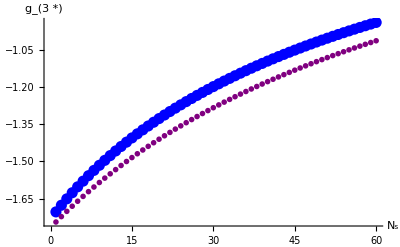

```mathematica
ListPlot[{Table[{i,FPplottab[[i,2]]},{i,1,Length[FPs]}],Table[{i,g3/.FPpert[[i,1]]},{i,1,Length[FPpert]}]},AxesLabel->{"N_s","g_(3 *)"}, LabelStyle->16,AxesStyle->Black, PlotStyle->{Directive[Blue, PointSize->0.02], Directive[Purple, PointSize->0.01]}, PlotRange->All]
```

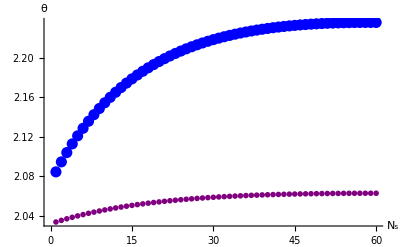

```mathematica
ListPlot[{Table[{i,thetatab[[i]]},{i,1,Length[FPs]}],Table[{i,thetapert[[i]]},{i,1,Length[FPpert]}]},AxesLabel->{"N_s","θ"}, LabelStyle->16,AxesStyle->Black, PlotStyle->{Directive[Blue, PointSize->0.02], Directive[Purple, PointSize->0.01]}, PlotRange->All]
```

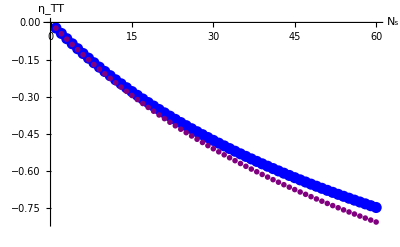

```mathematica
ListPlot[{Table[{i,etahtab[[i]]},{i,1,Length[FPs]}],Table[{i,etahpert[[i]]},{i,1,Length[FPpert]}]},AxesLabel->{"N_s","η_TT"}, LabelStyle->16,AxesStyle->Black, PlotStyle->{Directive[Blue, PointSize->0.02], Directive[Purple, PointSize->0.01]}, PlotRange->All]
```

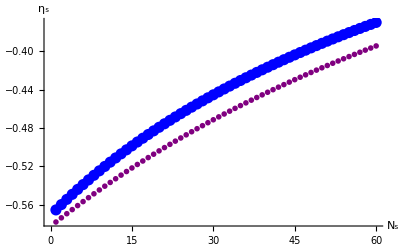

```mathematica
ListPlot[{Table[{i,etastab[[i]]},{i,1,Length[FPs]}],Table[{i,etaspert[[i]]},{i,1,Length[FPpert]}]},AxesLabel->{"N_s","η_s"}, LabelStyle->16,AxesStyle->Black, PlotStyle->{Directive[Blue, PointSize->0.02], Directive[Purple, PointSize->0.01]}, PlotRange->All]
```

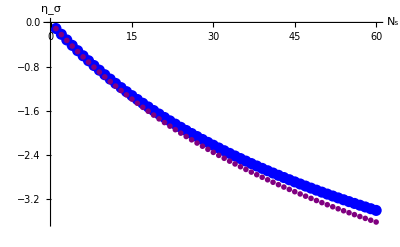

```mathematica
ListPlot[{Table[{i,etaσtab[[i]]},{i,1,Length[FPs]}],Table[{i,etaσpert[[i]]},{i,1,Length[FPpert]}]},AxesLabel->{"N_s","η_σ"}, LabelStyle->16,AxesStyle->Black, PlotStyle->{Directive[Blue, PointSize->0.02], Directive[Purple, PointSize->0.01]}, PlotRange->All]
```

#### approximation 1: g_5=g_3, g_4=g_3, G_EH=g_3

```mathematica
βgeta2=βgeta/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}
```

g3^2 (3/(4 π)+(16195 g3^3-8445 g3^3 Ns+540 g3^3 Ns^2+291952 g3^2 π-118176 g3^2 Ns π+525312 g3 π^2+165888 g3 Ns π^2)/(10 π (-5330 g3^3+3795 g3^3 Ns-78512 g3^2 π-5184 g3^2 Ns π-140544 g3 π^2-3981312 π^3))-(37405 g3^3-2910 g3^3 Ns+147888 g3^2 π-5184 g3^2 Ns π+1741824 g3 π^2)/(5 π (5330 g3^3-3795 g3^3 Ns+78512 g3^2 π+5184 g3^2 Ns π+140544 g3 π^2+3981312 π^3)))+g3^2 (3/(4 π)+(16195 g3^3-8445 g3^3 Ns+540 g3^3 Ns^2+291952 g3^2 π-118176 g3^2 Ns π+525312 g3 π^2+165888 g3 Ns π^2)/(5 π (-5330 g3^3+3795 g3^3 Ns-78512 g3^2 π-5184 g3^2 Ns π-140544 g3 π^2-3981312 π^3))-(37405 g3^3-2910 g3^3 Ns+147888 g3^2 π-5184 g3^2 Ns π+1741824 g3 π^2)/(10 π (5330 g3^3-3795 g3^3 Ns+78512 g3^2 π+5184 g3^2 Ns π+140544 g3 π^2+3981312 π^3)))+g3^2 (-2/(3 π)-(4 (16195 g3^3-8445 g3^3 Ns+540 g3^3 Ns^2+291952 g3^2 π-118176 g3^2 Ns π+525312 g3 π^2+165888 g3 Ns π^2))/(27 π (-5330 g3^3+3795 g3^3 Ns-78512 g3^2 π-5184 g3^2 Ns π-140544 g3 π^2-3981312 π^3))+(5 (1591 g3^3-7941 g3^3 Ns+54 g3^3 Ns^2-29840 g3^2 π+14592 g3^2 Ns π-884736 g3 π^2+41472 g3 Ns π^2))/(27 π (5330 g3^3-3795 g3^3 Ns+78512 g3^2 π+5184 g3^2 Ns π+140544 g3 π^2+3981312 π^3)))+g3^2 (-19/(18 π)+(38 (16195 g3^3-8445 g3^3 Ns+540 g3^3 Ns^2+291952 g3^2 π-118176 g3^2 Ns π+525312 g3 π^2+165888 g3 Ns π^2))/(81 π (-5330 g3^3+3795 g3^3 Ns-78512 g3^2 π-5184 g3^2 Ns π-140544 g3 π^2-3981312 π^3))+(95 (1591 g3^3-7941 g3^3 Ns+54 g3^3 Ns^2-29840 g3^2 π+14592 g3^2 Ns π-884736 g3 π^2+41472 g3 Ns π^2))/(81 π (5330 g3^3-3795 g3^3 Ns+78512 g3^2 π+5184 g3^2 Ns π+140544 g3 π^2+3981312 π^3)))+g3 (2+(8 (37405 g3^3-2910 g3^3 Ns+147888 g3^2 π-5184 g3^2 Ns π+1741824 g3 π^2))/(5330 g3^3-3795 g3^3 Ns+78512 g3^2 π+5184 g3^2 Ns π+140544 g3 π^2+3981312 π^3)+(4 (1591 g3^3-7941 g3^3 Ns+54 g3^3 Ns^2-29840 g3^2 π+14592 g3^2 Ns π-884736 g3 π^2+41472 g3 Ns π^2))/(5330 g3^3-3795 g3^3 Ns+78512 g3^2 π+5184 g3^2 Ns π+140544 g3 π^2+3981312 π^3)+g3 (-20/(9 π)-(5 (16195 g3^3-8445 g3^3 Ns+540 g3^3 Ns^2+291952 g3^2 π-118176 g3^2 Ns π+525312 g3 π^2+165888 g3 Ns π^2))/(9 π (-5330 g3^3+3795 g3^3 Ns-78512 g3^2 π-5184 g3^2 Ns π-140544 g3 π^2-3981312 π^3))+(5 (37405 g3^3-2910 g3^3 Ns+147888 g3^2 π-5184 g3^2 Ns π+1741824 g3 π^2))/(9 π (5330 g3^3-3795 g3^3 Ns+78512 g3^2 π+5184 g3^2 Ns π+140544 g3 π^2+3981312 π^3))))

```mathematica
βgetapert2=βgetapert/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}
```

g3 (2+g3 ((35 g3)/(144 π^2)-20/(9 π)+(5 ((19 g3)/(36 π)+(g3 Ns)/(6 π)))/(36 π))+(47 g3)/(18 π)+(g3 Ns)/(24 π))+g3^2 (-19/(18 π)+(95 (-(8 g3)/(9 π)+(g3 Ns)/(24 π)))/(324 π)-(19 ((19 g3)/(36 π)+(g3 Ns)/(6 π)))/(162 π))+g3^2 (-(7 g3)/(160 π^2)+3/(4 π)-((19 g3)/(36 π)+(g3 Ns)/(6 π))/(20 π))+g3^2 (-(7 g3)/(80 π^2)+3/(4 π)-((19 g3)/(36 π)+(g3 Ns)/(6 π))/(40 π))+g3^2 (-2/(3 π)+(5 (-(8 g3)/(9 π)+(g3 Ns)/(24 π)))/(108 π)+((19 g3)/(36 π)+(g3 Ns)/(6 π))/(27 π))

```mathematica
FP2=NSolve[βgeta2/.{Ns->2},{g3}]
```

{{g3→29.7842},{g3→-19.0491},{g3→-3.90898+15.1076 ⅈ},{g3→-3.90898-15.1076 ⅈ},{g3→0.}}

```mathematica
FP2pert=NSolve[βgetapert2/.{Ns->2},{g3}]
```

{{g3→-8.59599},{g3→0.+0. ⅈ},{g3→13.0643}}

```mathematica
FP8=NSolve[βgeta2/.{Ns->8},{g3}]
```

{{g3→-70.2374},{g3→14.3638},{g3→-4.1552+6.29114 ⅈ},{g3→-4.1552-6.29114 ⅈ},{g3→0.}}

```mathematica
-D[βgeta2,g3]/.Ns->8/.FP8
```

{10.6761,13.6172,4.72119+2.46469 ⅈ,4.72119-2.46469 ⅈ,-2.}

```mathematica
FP20=NSolve[βgeta2/.{Ns->20},{g3}]
```

{{g3→-123.258},{g3→11.7285},{g3→-3.14147+3.9386 ⅈ},{g3→-3.14147-3.9386 ⅈ},{g3→0.}}

```mathematica
-D[βgeta2,g3]/.Ns->20/.FP20
```

{11.4846,24.1003,3.84713+2.43201 ⅈ,3.84713-2.43201 ⅈ,-2.}

```mathematica
FPs=Table[NSolve[(βgeta2/.{Ns->i}),g3],{i,1,95}]
```

{{{g3→53.393},{g3→1.15771+16.074 ⅈ},{g3→1.15771-16.074 ⅈ},{g3→-13.8815},{g3→0.}},{{g3→29.7842},{g3→-19.0491},{g3→-3.90898+15.1076 ⅈ},{g3→-3.90898-15.1076 ⅈ},{g3→0.}},{{g3→-30.0025},{g3→22.3477},{g3→-5.60947+11.4435 ⅈ},{g3→-5.60947-11.4435 ⅈ},{g3→0.}},{{g3→-41.5492},{g3→19.0164},{g3→-5.32477+9.29497 ⅈ},{g3→-5.32477-9.29497 ⅈ},{g3→0.}},{{g3→-50.8463},{g3→17.1215},{g3→-4.92871+8.09936 ⅈ},{g3→-4.92871-8.09936 ⅈ},{g3→0.}},{{g3→-58.3761},{g3→15.8878},{g3→-4.609+7.31301 ⅈ},{g3→-4.609-7.31301 ⅈ},{g3→0.}},{{g3→-64.7103},{g3→15.0153},{g3→-4.35721+6.73867 ⅈ},{g3→-4.35721-6.73867 ⅈ},{g3→0.}},{{g3→-70.2374},{g3→14.3638},{g3→-4.1552+6.29114 ⅈ},{g3→-4.1552-6.29114 ⅈ},{g3→0.}},{{g3→-75.2154},{g3→13.8581},{g3→-3.98953+5.92705 ⅈ},{g3→-3.98953-5.92705 ⅈ},{g3→0.}},{{g3→-79.8206},{g3→13.4547},{g3→-3.85099+5.62166 ⅈ},{g3→-3.85099-5.62166 ⅈ},{g3→0.}},{{g3→-84.1788},{g3→13.1259},{g3→-3.73325+5.35957 ⅈ},{g3→-3.73325-5.35957 ⅈ},{g3→0.}},{{g3→-88.3834},{g3→12.8536},{g3→-3.63179+5.13066 ⅈ},{g3→-3.63179-5.13066 ⅈ},{g3→0.}},{{g3→-92.5067},{g3→12.6252},{g3→-3.54335+4.92788 ⅈ},{g3→-3.54335-4.92788 ⅈ},{g3→0.}},{{g3→-96.6074},{g3→12.4318},{g3→-3.46551+4.74617 ⅈ},{g3→-3.46551-4.74617 ⅈ},{g3→0.}},{{g3→-100.735},{g3→12.2669},{g3→-3.39643+4.58179 ⅈ},{g3→-3.39643-4.58179 ⅈ},{g3→0.}},{{g3→-104.935},{g3→12.1253},{g3→-3.33467+4.43187 ⅈ},{g3→-3.33467-4.43187 ⅈ},{g3→0.}},{{g3→-109.247},{g3→12.0034},{g3→-3.27911+4.29419 ⅈ},{g3→-3.27911-4.29419 ⅈ},{g3→0.}},{{g3→-113.711},{g3→11.8981},{g3→-3.22886+4.16699 ⅈ},{g3→-3.22886-4.16699 ⅈ},{g3→0.}},{{g3→-118.367},{g3→11.8071},{g3→-3.18317+4.04885 ⅈ},{g3→-3.18317-4.04885 ⅈ},{g3→0.}},{{g3→-123.258},{g3→11.7285},{g3→-3.14147+3.9386 ⅈ},{g3→-3.14147-3.9386 ⅈ},{g3→0.}},{{g3→-128.428},{g3→11.6607},{g3→-3.10325+3.8353 ⅈ},{g3→-3.10325-3.8353 ⅈ},{g3→0.}},{{g3→-133.925},{g3→11.6024},{g3→-3.06809+3.73814 ⅈ},{g3→-3.06809-3.73814 ⅈ},{g3→0.}},{{g3→-139.806},{g3→11.5525},{g3→-3.03566+3.64646 ⅈ},{g3→-3.03566-3.64646 ⅈ},{g3→0.}},{{g3→-146.134},{g3→11.5103},{g3→-3.00565+3.55966 ⅈ},{g3→-3.00565-3.55966 ⅈ},{g3→0.}},{{g3→-152.982},{g3→11.4749},{g3→-2.97782+3.47727 ⅈ},{g3→-2.97782-3.47727 ⅈ},{g3→0.}},{{g3→-160.437},{g3→11.4457},{g3→-2.95194+3.39886 ⅈ},{g3→-2.95194-3.39886 ⅈ},{g3→0.}},{{g3→-168.602},{g3→11.4221},{g3→-2.92783+3.32406 ⅈ},{g3→-2.92783-3.32406 ⅈ},{g3→0.}},{{g3→-177.604},{g3→11.4037},{g3→-2.90532+3.25254 ⅈ},{g3→-2.90532-3.25254 ⅈ},{g3→0.}},{{g3→-187.594},{g3→11.3901},{g3→-2.88426+3.18402 ⅈ},{g3→-2.88426-3.18402 ⅈ},{g3→0.}},{{g3→-198.766},{g3→11.381},{g3→-2.86454+3.11825 ⅈ},{g3→-2.86454-3.11825 ⅈ},{g3→0.}},{{g3→-211.359},{g3→11.376},{g3→-2.84603+3.05501 ⅈ},{g3→-2.84603-3.05501 ⅈ},{g3→0.}},{{g3→-225.683},{g3→11.3748},{g3→-2.82864+2.9941 ⅈ},{g3→-2.82864-2.9941 ⅈ},{g3→0.}},{{g3→-242.14},{g3→11.3773},{g3→-2.81229+2.93533 ⅈ},{g3→-2.81229-2.93533 ⅈ},{g3→0.}},{{g3→-261.267},{g3→11.3833},{g3→-2.79688+2.87856 ⅈ},{g3→-2.79688-2.87856 ⅈ},{g3→0.}},{{g3→-283.793},{g3→11.3925},{g3→-2.78236+2.82362 ⅈ},{g3→-2.78236-2.82362 ⅈ},{g3→0.}},{{g3→-310.738},{g3→11.4049},{g3→-2.76865+2.7704 ⅈ},{g3→-2.76865-2.7704 ⅈ},{g3→0.}},{{g3→-343.569},{g3→11.4203},{g3→-2.7557+2.71878 ⅈ},{g3→-2.7557-2.71878 ⅈ},{g3→0.}},{{g3→-384.486},{g3→11.4386},{g3→-2.74345+2.66863 ⅈ},{g3→-2.74345-2.66863 ⅈ},{g3→0.}},{{g3→-436.932},{g3→11.4596},{g3→-2.73187+2.61987 ⅈ},{g3→-2.73187-2.61987 ⅈ},{g3→0.}},{{g3→-506.63},{g3→11.4834},{g3→-2.7209+2.57241 ⅈ},{g3→-2.7209-2.57241 ⅈ},{g3→0.}},{{g3→-603.83},{g3→11.5098},{g3→-2.71051+2.52615 ⅈ},{g3→-2.71051-2.52615 ⅈ},{g3→0.}},{{g3→-748.904},{g3→11.5387},{g3→-2.70066+2.48103 ⅈ},{g3→-2.70066-2.48103 ⅈ},{g3→0.}},{{g3→-988.933},{g3→11.5703},{g3→-2.69132+2.43697 ⅈ},{g3→-2.69132-2.43697 ⅈ},{g3→0.}},{{g3→-1462.81},{g3→11.6043},{g3→-2.68245+2.3939 ⅈ},{g3→-2.68245-2.3939 ⅈ},{g3→0.}},{{g3→-2838.01},{g3→11.6407},{g3→-2.67404+2.35176 ⅈ},{g3→-2.67404-2.35176 ⅈ},{g3→0.}},{{g3→-58066.3},{g3→11.6797},{g3→-2.66605+2.3105 ⅈ},{g3→-2.66605-2.3105 ⅈ},{g3→0.}},{{g3→3105.61},{g3→11.721},{g3→-2.65847+2.27006 ⅈ},{g3→-2.65847-2.27006 ⅈ},{g3→0.}},{{g3→1502.62},{g3→11.7648},{g3→-2.65126+2.23038 ⅈ},{g3→-2.65126-2.23038 ⅈ},{g3→0.}},{{g3→986.68},{g3→11.8111},{g3→-2.64441+2.19144 ⅈ},{g3→-2.64441-2.19144 ⅈ},{g3→0.}},{{g3→731.956},{g3→11.8598},{g3→-2.63791+2.15317 ⅈ},{g3→-2.63791-2.15317 ⅈ},{g3→0.}},{{g3→580.104},{g3→11.9109},{g3→-2.63173+2.11553 ⅈ},{g3→-2.63173-2.11553 ⅈ},{g3→0.}},{{g3→479.248},{g3→11.9646},{g3→-2.62585+2.0785 ⅈ},{g3→-2.62585-2.0785 ⅈ},{g3→0.}},{{g3→407.372},{g3→12.0208},{g3→-2.62027+2.04202 ⅈ},{g3→-2.62027-2.04202 ⅈ},{g3→0.}},{{g3→353.54},{g3→12.0796},{g3→-2.61497+2.00606 ⅈ},{g3→-2.61497-2.00606 ⅈ},{g3→0.}},{{g3→311.703},{g3→12.1411},{g3→-2.60993+1.9706 ⅈ},{g3→-2.60993-1.9706 ⅈ},{g3→0.}},{{g3→278.244},{g3→12.2052},{g3→-2.60515+1.93559 ⅈ},{g3→-2.60515-1.93559 ⅈ},{g3→0.}},{{g3→250.867},{g3→12.2721},{g3→-2.60061+1.901 ⅈ},{g3→-2.60061-1.901 ⅈ},{g3→0.}},{{g3→228.046},{g3→12.3418},{g3→-2.59629+1.86681 ⅈ},{g3→-2.59629-1.86681 ⅈ},{g3→0.}},{{g3→208.725},{g3→12.4145},{g3→-2.5922+1.83298 ⅈ},{g3→-2.5922-1.83298 ⅈ},{g3→0.}},{{g3→192.15},{g3→12.4902},{g3→-2.58833+1.79948 ⅈ},{g3→-2.58833-1.79948 ⅈ},{g3→0.}},{{g3→177.771},{g3→12.569},{g3→-2.58465+1.7663 ⅈ},{g3→-2.58465-1.7663 ⅈ},{g3→0.}},{{g3→165.175},{g3→12.6511},{g3→-2.58117+1.7334 ⅈ},{g3→-2.58117-1.7334 ⅈ},{g3→0.}},{{g3→154.044},{g3→12.7366},{g3→-2.57787+1.70075 ⅈ},{g3→-2.57787-1.70075 ⅈ},{g3→0.}},{{g3→144.135},{g3→12.8257},{g3→-2.57476+1.66833 ⅈ},{g3→-2.57476-1.66833 ⅈ},{g3→0.}},{{g3→135.252},{g3→12.9184},{g3→-2.57182+1.63611 ⅈ},{g3→-2.57182-1.63611 ⅈ},{g3→0.}},{{g3→127.242},{g3→13.0151},{g3→-2.56904+1.60407 ⅈ},{g3→-2.56904-1.60407 ⅈ},{g3→0.}},{{g3→119.979},{g3→13.1159},{g3→-2.56642+1.57217 ⅈ},{g3→-2.56642-1.57217 ⅈ},{g3→0.}},{{g3→113.36},{g3→13.221},{g3→-2.56396+1.54041 ⅈ},{g3→-2.56396-1.54041 ⅈ},{g3→0.}},{{g3→107.3},{g3→13.3307},{g3→-2.56164+1.50874 ⅈ},{g3→-2.56164-1.50874 ⅈ},{g3→0.}},{{g3→101.729},{g3→13.4452},{g3→-2.55947+1.47715 ⅈ},{g3→-2.55947-1.47715 ⅈ},{g3→0.}},{{g3→96.5872},{g3→13.5649},{g3→-2.55743+1.4456 ⅈ},{g3→-2.55743-1.4456 ⅈ},{g3→0.}},{{g3→91.8238},{g3→13.6902},{g3→-2.55553+1.41407 ⅈ},{g3→-2.55553-1.41407 ⅈ},{g3→0.}},{{g3→87.396},{g3→13.8214},{g3→-2.55375+1.38254 ⅈ},{g3→-2.55375-1.38254 ⅈ},{g3→0.}},{{g3→83.2669},{g3→13.9589},{g3→-2.5521+1.35096 ⅈ},{g3→-2.5521-1.35096 ⅈ},{g3→0.}},{{g3→79.4044},{g3→14.1033},{g3→-2.55057+1.31931 ⅈ},{g3→-2.55057-1.31931 ⅈ},{g3→0.}},{{g3→75.7807},{g3→14.2552},{g3→-2.54916+1.28756 ⅈ},{g3→-2.54916-1.28756 ⅈ},{g3→0.}},{{g3→72.3713},{g3→14.4151},{g3→-2.54786+1.25567 ⅈ},{g3→-2.54786-1.25567 ⅈ},{g3→0.}},{{g3→69.1547},{g3→14.584},{g3→-2.54667+1.2236 ⅈ},{g3→-2.54667-1.2236 ⅈ},{g3→0.}},{{g3→66.1118},{g3→14.7625},{g3→-2.54558+1.19133 ⅈ},{g3→-2.54558-1.19133 ⅈ},{g3→0.}},{{g3→63.2253},{g3→14.9518},{g3→-2.5446+1.15879 ⅈ},{g3→-2.5446-1.15879 ⅈ},{g3→0.}},{{g3→60.4799},{g3→15.1531},{g3→-2.54371+1.12596 ⅈ},{g3→-2.54371-1.12596 ⅈ},{g3→0.}},{{g3→57.8612},{g3→15.3677},{g3→-2.54293+1.09277 ⅈ},{g3→-2.54293-1.09277 ⅈ},{g3→0.}},{{g3→55.3564},{g3→15.5975},{g3→-2.54223+1.05917 ⅈ},{g3→-2.54223-1.05917 ⅈ},{g3→0.}},{{g3→52.9532},{g3→15.8445},{g3→-2.54163+1.02509 ⅈ},{g3→-2.54163-1.02509 ⅈ},{g3→0.}},{{g3→50.6398},{g3→16.1113},{g3→-2.54112+0.990466 ⅈ},{g3→-2.54112-0.990466 ⅈ},{g3→0.}},{{g3→48.4048},{g3→16.4011},{g3→-2.54069+0.955213 ⅈ},{g3→-2.54069-0.955213 ⅈ},{g3→0.}},{{g3→46.2367},{g3→16.7183},{g3→-2.54035+0.919236 ⅈ},{g3→-2.54035-0.919236 ⅈ},{g3→0.}},{{g3→44.1231},{g3→17.0683},{g3→-2.54009+0.882423 ⅈ},{g3→-2.54009-0.882423 ⅈ},{g3→0.}},{{g3→42.0503},{g3→17.4588},{g3→-2.53991+0.844642 ⅈ},{g3→-2.53991-0.844642 ⅈ},{g3→0.}},{{g3→40.0022},{g3→17.9005},{g3→-2.5398+0.805736 ⅈ},{g3→-2.5398-0.805736 ⅈ},{g3→0.}},{{g3→37.9575},{g3→18.4097},{g3→-2.53978+0.765508 ⅈ},{g3→-2.53978-0.765508 ⅈ},{g3→0.}},{{g3→35.8854},{g3→19.0123},{g3→-2.53982+0.723716 ⅈ},{g3→-2.53982-0.723716 ⅈ},{g3→0.}},{{g3→33.7344},{g3→19.756},{g3→-2.53994+0.680047 ⅈ},{g3→-2.53994-0.680047 ⅈ},{g3→0.}},{{g3→31.3962},{g3→20.7449},{g3→-2.54013+0.634089 ⅈ},{g3→-2.54013-0.634089 ⅈ},{g3→0.}},{{g3→28.5137},{g3→22.3329},{g3→-2.54039+0.585278 ⅈ},{g3→-2.54039-0.585278 ⅈ},{g3→0.}}}

```mathematica
AllrealFPs=Table[{i,Sort[DeleteCases[Table[If[Abs[Im[g3/.FPs[[i,j]]]]>0,x,g3/.FPs[[i,j]]],{j,1,Length[FPs[[i]]]}],x],#1<#2&]},{i,1,Length[FPs]}]
```

{{1,{-13.8815,0.,53.393}},{2,{-19.0491,0.,29.7842}},{3,{-30.0025,0.,22.3477}},{4,{-41.5492,0.,19.0164}},{5,{-50.8463,0.,17.1215}},{6,{-58.3761,0.,15.8878}},{7,{-64.7103,0.,15.0153}},{8,{-70.2374,0.,14.3638}},{9,{-75.2154,0.,13.8581}},{10,{-79.8206,0.,13.4547}},{11,{-84.1788,0.,13.1259}},{12,{-88.3834,0.,12.8536}},{13,{-92.5067,0.,12.6252}},{14,{-96.6074,0.,12.4318}},{15,{-100.735,0.,12.2669}},{16,{-104.935,0.,12.1253}},{17,{-109.247,0.,12.0034}},{18,{-113.711,0.,11.8981}},{19,{-118.367,0.,11.8071}},{20,{-123.258,0.,11.7285}},{21,{-128.428,0.,11.6607}},{22,{-133.925,0.,11.6024}},{23,{-139.806,0.,11.5525}},{24,{-146.134,0.,11.5103}},{25,{-152.982,0.,11.4749}},{26,{-160.437,0.,11.4457}},{27,{-168.602,0.,11.4221}},{28,{-177.604,0.,11.4037}},{29,{-187.594,0.,11.3901}},{30,{-198.766,0.,11.381}},{31,{-211.359,0.,11.376}},{32,{-225.683,0.,11.3748}},{33,{-242.14,0.,11.3773}},{34,{-261.267,0.,11.3833}},{35,{-283.793,0.,11.3925}},{36,{-310.738,0.,11.4049}},{37,{-343.569,0.,11.4203}},{38,{-384.486,0.,11.4386}},{39,{-436.932,0.,11.4596}},{40,{-506.63,0.,11.4834}},{41,{-603.83,0.,11.5098}},{42,{-748.904,0.,11.5387}},{43,{-988.933,0.,11.5703}},{44,{-1462.81,0.,11.6043}},{45,{-2838.01,0.,11.6407}},{46,{-58066.3,0.,11.6797}},{47,{0.,11.721,3105.61}},{48,{0.,11.7648,1502.62}},{49,{0.,11.8111,986.68}},{50,{0.,11.8598,731.956}},{51,{0.,11.9109,580.104}},{52,{0.,11.9646,479.248}},{53,{0.,12.0208,407.372}},{54,{0.,12.0796,353.54}},{55,{0.,12.1411,311.703}},{56,{0.,12.2052,278.244}},{57,{0.,12.2721,250.867}},{58,{0.,12.3418,228.046}},{59,{0.,12.4145,208.725}},{60,{0.,12.4902,192.15}},{61,{0.,12.569,177.771}},{62,{0.,12.6511,165.175}},{63,{0.,12.7366,154.044}},{64,{0.,12.8257,144.135}},{65,{0.,12.9184,135.252}},{66,{0.,13.0151,127.242}},{67,{0.,13.1159,119.979}},{68,{0.,13.221,113.36}},{69,{0.,13.3307,107.3}},{70,{0.,13.4452,101.729}},{71,{0.,13.5649,96.5872}},{72,{0.,13.6902,91.8238}},{73,{0.,13.8214,87.396}},{74,{0.,13.9589,83.2669}},{75,{0.,14.1033,79.4044}},{76,{0.,14.2552,75.7807}},{77,{0.,14.4151,72.3713}},{78,{0.,14.584,69.1547}},{79,{0.,14.7625,66.1118}},{80,{0.,14.9518,63.2253}},{81,{0.,15.1531,60.4799}},{82,{0.,15.3677,57.8612}},{83,{0.,15.5975,55.3564}},{84,{0.,15.8445,52.9532}},{85,{0.,16.1113,50.6398}},{86,{0.,16.4011,48.4048}},{87,{0.,16.7183,46.2367}},{88,{0.,17.0683,44.1231}},{89,{0.,17.4588,42.0503}},{90,{0.,17.9005,40.0022}},{91,{0.,18.4097,37.9575}},{92,{0.,19.0123,35.8854}},{93,{0.,19.756,33.7344}},{94,{0.,20.7449,31.3962}},{95,{0.,22.3329,28.5137}}}

```mathematica
thetas3=Table[{i,-D[βgeta2,g3]/.{g3->AllrealFPs[[i,2]]}/.Ns->i},{i,1,Length[FPs]}]
```

{{1,{3.84995,-2.,11.6544}},{2,{3.55397,-2.,10.0461}},{3,{5.0553,-2.,10.3238}},{4,{7.31272,-2.,10.9279}},{5,{8.79589,-2.,11.5842}},{6,{9.70544,-2.,12.2528}},{7,{10.2872,-2.,12.9296}},{8,{10.6761,-2.,13.6172}},{9,{10.9448,-2.,14.319}},{10,{11.1344,-2.,15.039}},{11,{11.2694,-2.,15.7807}},{12,{11.3654,-2.,16.5479}},{13,{11.4324,-2.,17.3442}},{14,{11.4774,-2.,18.1734}},{15,{11.5053,-2.,19.0398}},{16,{11.5197,-2.,19.9476}},{17,{11.523,-2.,20.9018}},{18,{11.5173,-2.,21.9078}},{19,{11.5041,-2.,22.9716}},{20,{11.4846,-2.,24.1003}},{21,{11.4596,-2.,25.3015}},{22,{11.43,-2.,26.5845}},{23,{11.3962,-2.,27.9598}},{24,{11.3589,-2.,29.4396}},{25,{11.3184,-2.,31.0386}},{26,{11.2751,-2.,32.7738}},{27,{11.2291,-2.,34.666}},{28,{11.1808,-2.,36.7401}},{29,{11.1304,-2.,39.0266}},{30,{11.0779,-2.,41.563}},{31,{11.0236,-2.,44.3964}},{32,{10.9676,-2.,47.586}},{33,{10.9099,-2.,51.2082}},{34,{10.8507,-2.,55.3629}},{35,{10.79,-2.,60.183}},{36,{10.7278,-2.,65.8497}},{37,{10.6643,-2.,72.6164}},{38,{10.5995,-2.,80.8491}},{39,{10.5334,-2.,91.0961}},{40,{10.4659,-2.,104.218}},{41,{10.3973,-2.,121.648}},{42,{10.3274,-2.,145.961}},{43,{10.2562,-2.,182.291}},{44,{10.1839,-2.,242.579}},{45,{10.1103,-2.,362.405}},{46,{10.0355,-2.,716.91}},{47,{-2.,36788.8,9.95941}},{48,{-2.,-743.19,9.8821}},{49,{-2.,-366.948,9.80353}},{50,{-2.,-243.095,9.72366}},{51,{-2.,-181.394,9.64249}},{52,{-2.,-144.406,9.55997}},{53,{-2.,-119.732,9.47607}},{54,{-2.,-102.08,9.39077}},{55,{-2.,-88.809,9.30401}},{56,{-2.,-78.4553,9.21576}},{57,{-2.,-70.1416,9.12596}},{58,{-2.,-63.31,9.03456}},{59,{-2.,-57.5891,8.94149}},{60,{-2.,-52.7217,8.84669}},{61,{-2.,-48.5243,8.7501}},{62,{-2.,-44.8623,8.65162}},{63,{-2.,-41.6349,8.55117}},{64,{-2.,-38.7647,8.44866}},{65,{-2.,-36.1919,8.34398}},{66,{-2.,-33.8688,8.23701}},{67,{-2.,-31.7577,8.12764}},{68,{-2.,-29.8278,8.01573}},{69,{-2.,-28.0537,7.90111}},{70,{-2.,-26.4147,7.78362}},{71,{-2.,-24.8934,7.66308}},{72,{-2.,-23.475,7.53927}},{73,{-2.,-22.1471,7.41197}},{74,{-2.,-20.8989,7.28091}},{75,{-2.,-19.7213,7.1458}},{76,{-2.,-18.6061,7.0063}},{77,{-2.,-17.5463,6.86204}},{78,{-2.,-16.5358,6.71258}},{79,{-2.,-15.5687,6.55742}},{80,{-2.,-14.6402,6.39599}},{81,{-2.,-13.7456,6.2276}},{82,{-2.,-12.8805,6.05144}},{83,{-2.,-12.041,5.86656}},{84,{-2.,-11.223,5.67178}},{85,{-2.,-10.4227,5.46566}},{86,{-2.,-9.63591,5.24641}},{87,{-2.,-8.85846,5.01171}},{88,{-2.,-8.08547,4.75853}},{89,{-2.,-7.3112,4.48278}},{90,{-2.,-6.52836,4.17865}},{91,{-2.,-5.72696,3.8375}},{92,{-2.,-4.89187,3.44543}},{93,{-2.,-3.99697,2.97745}},{94,{-2.,-2.9867,2.37903}},{95,{-2.,-1.67667,1.4667}}}

```mathematica
thetas1=Table[-D[βgeta2,g3]/.{g3->AllrealFPs[[i,2]]}/.Ns->i,{i,1,Length[FPs]}]
```

{{3.84995,-2.,11.6544},{3.55397,-2.,10.0461},{5.0553,-2.,10.3238},{7.31272,-2.,10.9279},{8.79589,-2.,11.5842},{9.70544,-2.,12.2528},{10.2872,-2.,12.9296},{10.6761,-2.,13.6172},{10.9448,-2.,14.319},{11.1344,-2.,15.039},{11.2694,-2.,15.7807},{11.3654,-2.,16.5479},{11.4324,-2.,17.3442},{11.4774,-2.,18.1734},{11.5053,-2.,19.0398},{11.5197,-2.,19.9476},{11.523,-2.,20.9018},{11.5173,-2.,21.9078},{11.5041,-2.,22.9716},{11.4846,-2.,24.1003},{11.4596,-2.,25.3015},{11.43,-2.,26.5845},{11.3962,-2.,27.9598},{11.3589,-2.,29.4396},{11.3184,-2.,31.0386},{11.2751,-2.,32.7738},{11.2291,-2.,34.666},{11.1808,-2.,36.7401},{11.1304,-2.,39.0266},{11.0779,-2.,41.563},{11.0236,-2.,44.3964},{10.9676,-2.,47.586},{10.9099,-2.,51.2082},{10.8507,-2.,55.3629},{10.79,-2.,60.183},{10.7278,-2.,65.8497},{10.6643,-2.,72.6164},{10.5995,-2.,80.8491},{10.5334,-2.,91.0961},{10.4659,-2.,104.218},{10.3973,-2.,121.648},{10.3274,-2.,145.961},{10.2562,-2.,182.291},{10.1839,-2.,242.579},{10.1103,-2.,362.405},{10.0355,-2.,716.91},{-2.,36788.8,9.95941},{-2.,-743.19,9.8821},{-2.,-366.948,9.80353},{-2.,-243.095,9.72366},{-2.,-181.394,9.64249},{-2.,-144.406,9.55997},{-2.,-119.732,9.47607},{-2.,-102.08,9.39077},{-2.,-88.809,9.30401},{-2.,-78.4553,9.21576},{-2.,-70.1416,9.12596},{-2.,-63.31,9.03456},{-2.,-57.5891,8.94149},{-2.,-52.7217,8.84669},{-2.,-48.5243,8.7501},{-2.,-44.8623,8.65162},{-2.,-41.6349,8.55117},{-2.,-38.7647,8.44866},{-2.,-36.1919,8.34398},{-2.,-33.8688,8.23701},{-2.,-31.7577,8.12764},{-2.,-29.8278,8.01573},{-2.,-28.0537,7.90111},{-2.,-26.4147,7.78362},{-2.,-24.8934,7.66308},{-2.,-23.475,7.53927},{-2.,-22.1471,7.41197},{-2.,-20.8989,7.28091},{-2.,-19.7213,7.1458},{-2.,-18.6061,7.0063},{-2.,-17.5463,6.86204},{-2.,-16.5358,6.71258},{-2.,-15.5687,6.55742},{-2.,-14.6402,6.39599},{-2.,-13.7456,6.2276},{-2.,-12.8805,6.05144},{-2.,-12.041,5.86656},{-2.,-11.223,5.67178},{-2.,-10.4227,5.46566},{-2.,-9.63591,5.24641},{-2.,-8.85846,5.01171},{-2.,-8.08547,4.75853},{-2.,-7.3112,4.48278},{-2.,-6.52836,4.17865},{-2.,-5.72696,3.8375},{-2.,-4.89187,3.44543},{-2.,-3.99697,2.97745},{-2.,-2.9867,2.37903},{-2.,-1.67667,1.4667}}

```mathematica
thetas=Table[-D[βgeta2,g3]/.g3->AllrealFPs[[i,2,2]]/.Ns->i,{i,1,Length[FPs]}]
```

{-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,36788.8,-743.19,-366.948,-243.095,-181.394,-144.406,-119.732,-102.08,-88.809,-78.4553,-70.1416,-63.31,-57.5891,-52.7217,-48.5243,-44.8623,-41.6349,-38.7647,-36.1919,-33.8688,-31.7577,-29.8278,-28.0537,-26.4147,-24.8934,-23.475,-22.1471,-20.8989,-19.7213,-18.6061,-17.5463,-16.5358,-15.5687,-14.6402,-13.7456,-12.8805,-12.041,-11.223,-10.4227,-9.63591,-8.85846,-8.08547,-7.3112,-6.52836,-5.72696,-4.89187,-3.99697,-2.9867,-1.67667}

```mathematica
etahtab=Table[ηh/.etasol/.{G3->GEH, G4->GEH}/.Ns->i/.GEH->g3/.g4->g3/.g3->AllrealFPs[[i,2]],{i,1,Length[AllrealFPs]}]
```

{{3.26741,0.,-5.21458},{4.62289,0.,-6.91039},{6.66334,0.,-6.62895},{7.78812,0.,-6.24217},{8.19788,0.,-5.93018},{8.33173,0.,-5.68361},{8.35584,0.,-5.48391},{8.33217,0.,-5.31768},{8.28617,0.,-5.17594},{8.22924,0.,-5.05261},{8.16688,0.,-4.94347},{8.10185,0.,-4.84552},{8.0356,0.,-4.75653},{7.96891,0.,-4.67486},{7.90219,0.,-4.59921},{7.83566,0.,-4.52861},{7.76941,0.,-4.46226},{7.70348,0.,-4.39953},{7.63788,0.,-4.33991},{7.5726,0.,-4.28296},{7.50761,0.,-4.22833},{7.44287,0.,-4.17572},{7.37836,0.,-4.12488},{7.31404,0.,-4.07559},{7.24987,0.,-4.02767},{7.18584,0.,-3.98096},{7.1219,0.,-3.9353},{7.05802,0.,-3.89059},{6.9942,0.,-3.8467},{6.93038,0.,-3.80355},{6.86657,0.,-3.76103},{6.80272,0.,-3.71908},{6.73883,0.,-3.67762},{6.67487,0.,-3.6366},{6.61082,0.,-3.59594},{6.54666,0.,-3.5556},{6.48238,0.,-3.51552},{6.41796,0.,-3.47566},{6.35338,0.,-3.43598},{6.28862,0.,-3.39644},{6.22368,0.,-3.35699},{6.15853,0.,-3.3176},{6.09316,0.,-3.27825},{6.02754,0.,-3.23889},{5.96168,0.,-3.19949},{5.89554,0.,-3.16002},{0.,-3.12046,5.82912},{0.,-3.08078,5.76239},{0.,-3.04094,5.69535},{0.,-3.00092,5.62796},{0.,-2.96069,5.56022},{0.,-2.92022,5.4921},{0.,-2.87949,5.42359},{0.,-2.83846,5.35466},{0.,-2.79711,5.2853},{0.,-2.75541,5.21548},{0.,-2.71333,5.14518},{0.,-2.67084,5.07436},{0.,-2.6279,5.00302},{0.,-2.58448,4.93112},{0.,-2.54056,4.85862},{0.,-2.49608,4.78551},{0.,-2.45102,4.71174},{0.,-2.40533,4.63728},{0.,-2.35897,4.56208},{0.,-2.3119,4.48612},{0.,-2.26406,4.40934},{0.,-2.2154,4.33169},{0.,-2.16587,4.25312},{0.,-2.1154,4.17358},{0.,-2.06393,4.09299},{0.,-2.01139,4.01128},{0.,-1.95768,3.92838},{0.,-1.90272,3.84421},{0.,-1.84642,3.75865},{0.,-1.78865,3.67161},{0.,-1.7293,3.58295},{0.,-1.66822,3.49254},{0.,-1.60524,3.40022},{0.,-1.54018,3.3058},{0.,-1.47281,3.20906},{0.,-1.40289,3.10974},{0.,-1.33011,3.00755},{0.,-1.25409,2.90212},{0.,-1.1744,2.793},{0.,-1.09046,2.67963},{0.,-1.00157,2.56131},{0.,-0.906814,2.4371},{0.,-0.804934,2.30578},{0.,-0.694188,2.16559},{0.,-0.57199,2.01394},{0.,-0.434217,1.84672},{0.,-0.273508,1.65657},{0.,-0.0739446,1.42756},{0.,0.217501,1.10668}}

```mathematica
etastab=Table[ηs/.etasol/.{G3->GEH, G4->GEH}/.Ns->i/.GEH->g3/.g4->g3/.g3->AllrealFPs[[i,2]],{i,1,Length[AllrealFPs]}]
```

{{-6.48804,0.,25.2266},{-7.27274,0.,19.6152},{-7.16492,0.,15.5574},{-5.71569,0.,13.3144},{-4.28654,0.,11.9249},{-3.17668,0.,10.9739},{-2.33507,0.,10.2759},{-1.6868,0.,9.73752},{-1.17608,0.,9.30683},{-0.764828,0.,8.95247},{-0.427144,0.,8.65442},{-0.145109,0.,8.39921},{0.09395,0.,8.17743},{0.299203,0.,7.98231},{0.477423,0.,7.80883},{0.633712,0.,7.65316},{0.77198,0.,7.51237},{0.895269,0.,7.38414},{1.00598,0.,7.26662},{1.10603,0.,7.15832},{1.19698,0.,7.05799},{1.2801,0.,6.96464},{1.35642,0.,6.87741},{1.42682,0.,6.7956},{1.49204,0.,6.71858},{1.55268,0.,6.64585},{1.60928,0.,6.57696},{1.66228,0.,6.51153},{1.71207,0.,6.4492},{1.75898,0.,6.3897},{1.80331,0.,6.33277},{1.84532,0.,6.27816},{1.88522,0.,6.22568},{1.92322,0.,6.17515},{1.95949,0.,6.12641},{1.99418,0.,6.0793},{2.02744,0.,6.03371},{2.0594,0.,5.9895},{2.09015,0.,5.94657},{2.11981,0.,5.90482},{2.14847,0.,5.86417},{2.1762,0.,5.82453},{2.2031,0.,5.78583},{2.22921,0.,5.74799},{2.25462,0.,5.71095},{2.27937,0.,5.67466},{0.,5.63906,2.30353},{0.,5.60409,2.32714},{0.,5.56971,2.35025},{0.,5.53588,2.37289},{0.,5.50254,2.39512},{0.,5.46967,2.41698},{0.,5.43722,2.43848},{0.,5.40516,2.45968},{0.,5.37346,2.4806},{0.,5.34207,2.50127},{0.,5.31098,2.52173},{0.,5.28014,2.54199},{0.,5.24954,2.5621},{0.,5.21914,2.58207},{0.,5.18891,2.60193},{0.,5.15883,2.62171},{0.,5.12886,2.64143},{0.,5.09899,2.66111},{0.,5.06918,2.68079},{0.,5.03942,2.70049},{0.,5.00966,2.72023},{0.,4.97988,2.74004},{0.,4.95006,2.75995},{0.,4.92016,2.77998},{0.,4.89015,2.80017},{0.,4.86001,2.82055},{0.,4.82968,2.84115},{0.,4.79915,2.86201},{0.,4.76836,2.88316},{0.,4.73728,2.90465},{0.,4.70585,2.92652},{0.,4.67402,2.94883},{0.,4.64174,2.97163},{0.,4.60894,2.99499},{0.,4.57553,3.01899},{0.,4.54144,3.04371},{0.,4.50655,3.06925},{0.,4.47075,3.09575},{0.,4.43388,3.12334},{0.,4.39576,3.15222},{0.,4.35614,3.18261},{0.,4.31474,3.21482},{0.,4.27114,3.24927},{0.,4.22477,3.28651},{0.,4.17478,3.32739},{0.,4.11983,3.37325},{0.,4.05753,3.42649},{0.,3.98269,3.4923},{0.,3.87804,3.58793}}

```mathematica
etaσtab=Table[ησ/.etasol/.{G3->GEH, G4->GEH}/.Ns->i/.GEH->g3/.g4->g3/.g3->AllrealFPs[[i,2]],{i,1,Length[AllrealFPs]}]
```

{-0.482708,-0.702378,-0.911009,-1.10819,-1.29364,-1.46726,-1.62912,-1.77943,-1.91857,-2.04702,-2.16538,-2.27426,-2.37435,-2.46632,-2.55085,-2.62856,-2.70008,-2.76595,-2.8267,-2.88281,-2.93471,-2.98279,-3.0274,-3.06887,-3.10746,-3.14345,-3.17707,-3.20851,-3.23796,-3.2656,-3.29156,-3.31599,-3.33901,-3.36073,-3.38124,-3.40064,-3.41902,-3.43643,-3.45296,-3.46867,-3.4836,-3.49782,-3.51137,-3.5243,-3.53663,-3.54842,-3.55969,-3.57048,-3.58081,-3.59071,-3.60021,-3.60933,-3.61809,-3.6265,-3.6346,-3.64239,-3.64989,-3.65712,-3.66409,-3.67081,-3.6773,-3.68356,-3.68961,-3.69546,-3.70112,-3.70659,-3.71189,-3.71702,-3.72199,-3.7268,-3.73147,-3.736,-3.74039,-3.74466,-3.7488,-3.75282,-3.75673,-3.76053,-3.76423,-3.76782,-3.77132,-3.77472,-3.77804,-3.78127,-3.78441,-3.78747,-3.79046,-3.79337,-3.79621,-3.79898,-3.80169,-3.80433,-3.8069,-3.80942,-3.81187,-3.81427,-3.81662,-3.81891,-3.82115,-3.82334}

```mathematica
FPspert=Table[NSolve[(βgetapert2/.{Ns->i}),g3],{i,1,60}]
```

{{{g3→-8.66839},{g3→0.+0. ⅈ},{g3→12.1648}},{{g3→-8.59599},{g3→0.+0. ⅈ},{g3→13.0643}},{{g3→-8.52053},{g3→0.+0. ⅈ},{g3→14.0958}},{{g3→-8.44192},{g3→0.+0. ⅈ},{g3→15.2894}},{{g3→-8.36002},{g3→0.+0. ⅈ},{g3→16.6851}},{{g3→-8.27474},{g3→0.+0. ⅈ},{g3→18.3368}},{{g3→-8.18596},{g3→0.+0. ⅈ},{g3→20.3193}},{{g3→-8.09362},{g3→0.+0. ⅈ},{g3→22.7393}},{{g3→-7.99762},{g3→0.+0. ⅈ},{g3→25.7544}},{{g3→-7.89793},{g3→0.+0. ⅈ},{g3→29.6077}},{{g3→-7.79452},{g3→0.+0. ⅈ},{g3→34.694}},{{g3→-7.68739},{g3→0.+0. ⅈ},{g3→41.7016}},{{g3→-7.57658},{g3→0.+0. ⅈ},{g3→51.9455}},{{g3→-7.46217},{g3→0.+0. ⅈ},{g3→68.2914}},{{g3→-7.34427},{g3→0.+0. ⅈ},{g3→98.3972}},{{g3→-7.22306},{g3→0.+0. ⅈ},{g3→171.928}},{{g3→-7.09874},{g3→0.+0. ⅈ},{g3→621.334}},{{g3→-407.719},{g3→-6.97159},{g3→0.+0. ⅈ}},{{g3→-157.102},{g3→-6.8419},{g3→0.+0. ⅈ}},{{g3→-98.7693},{g3→-6.71004},{g3→0.+0. ⅈ}},{{g3→-72.8459},{g3→-6.5764},{g3→0.+0. ⅈ}},{{g3→-58.233},{g3→-6.44141},{g3→0.+0. ⅈ}},{{g3→-48.8805},{g3→-6.30552},{g3→0.+0. ⅈ}},{{g3→-42.4002},{g3→-6.16918},{g3→0.+0. ⅈ}},{{g3→-37.6593},{g3→-6.03288},{g3→0.+0. ⅈ}},{{g3→-34.051},{g3→-5.89706},{g3→0.+0. ⅈ}},{{g3→-31.2211},{g3→-5.76218},{g3→0.+0. ⅈ}},{{g3→-28.9489},{g3→-5.62864},{g3→0.+0. ⅈ}},{{g3→-27.0894},{g3→-5.49682},{g3→0.+0. ⅈ}},{{g3→-25.5438},{g3→-5.36708},{g3→0.+0. ⅈ}},{{g3→-24.242},{g3→-5.23971},{g3→0.+0. ⅈ}},{{g3→-23.1332},{g3→-5.11497},{g3→0.+0. ⅈ}},{{g3→-22.1797},{g3→-4.99307},{g3→0.+0. ⅈ}},{{g3→-21.3526},{g3→-4.87418},{g3→0.+0. ⅈ}},{{g3→-20.6299},{g3→-4.75843},{g3→0.+0. ⅈ}},{{g3→-19.994},{g3→-4.6459},{g3→0.+0. ⅈ}},{{g3→-19.4312},{g3→-4.53667},{g3→0.+0. ⅈ}},{{g3→-18.9303},{g3→-4.43074},{g3→0.+0. ⅈ}},{{g3→-18.4823},{g3→-4.32813},{g3→0.+0. ⅈ}},{{g3→-18.0797},{g3→-4.22881},{g3→0.+0. ⅈ}},{{g3→-17.7163},{g3→-4.13274},{g3→0.+0. ⅈ}},{{g3→-17.3871},{g3→-4.03986},{g3→0.+0. ⅈ}},{{g3→-17.0878},{g3→-3.95012},{g3→0.+0. ⅈ}},{{g3→-16.8146},{g3→-3.86342},{g3→0.+0. ⅈ}},{{g3→-16.5645},{g3→-3.7797},{g3→0.+0. ⅈ}},{{g3→-16.3349},{g3→-3.69885},{g3→0.+0. ⅈ}},{{g3→-16.1235},{g3→-3.62079},{g3→0.+0. ⅈ}},{{g3→-15.9283},{g3→-3.54542},{g3→0.+0. ⅈ}},{{g3→-15.7476},{g3→-3.47264},{g3→0.+0. ⅈ}},{{g3→-15.58},{g3→-3.40236},{g3→0.+0. ⅈ}},{{g3→-15.4241},{g3→-3.33448},{g3→0.+0. ⅈ}},{{g3→-15.2789},{g3→-3.26892},{g3→0.+0. ⅈ}},{{g3→-15.1432},{g3→-3.20557},{g3→0.+0. ⅈ}},{{g3→-15.0163},{g3→-3.14435},{g3→0.+0. ⅈ}},{{g3→-14.8974},{g3→-3.08518},{g3→0.+0. ⅈ}},{{g3→-14.7858},{g3→-3.02797},{g3→0.+0. ⅈ}},{{g3→-14.6807},{g3→-2.97263},{g3→0.+0. ⅈ}},{{g3→-14.5818},{g3→-2.9191},{g3→0.+0. ⅈ}},{{g3→-14.4885},{g3→-2.86729},{g3→0.+0. ⅈ}},{{g3→-14.4003},{g3→-2.81714},{g3→0.+0. ⅈ}}}

```mathematica
thetaspert=Table[-D[βgetapert2,g3]/.FPspert[[i,2]]/.Ns->i,{i,1,Length[FPspert]}]
```

{-2.+0. ⅈ,-2.+0. ⅈ,-2.+0. ⅈ,-2.+0. ⅈ,-2.+0. ⅈ,-2.+0. ⅈ,-2.+0. ⅈ,-2.+0. ⅈ,-2.+0. ⅈ,-2.+0. ⅈ,-2.+0. ⅈ,-2.+0. ⅈ,-2.+0. ⅈ,-2.+0. ⅈ,-2.+0. ⅈ,-2.+0. ⅈ,-2.+0. ⅈ,1.9658,1.9129,1.86413,1.81944,1.77877,1.742,1.709,1.67961,1.65363,1.63088,1.61113,1.59417,1.57977,1.56772,1.55778,1.54976,1.54346,1.53869,1.53527,1.53305,1.53189,1.53165,1.5322,1.53346,1.5353,1.53767,1.54047,1.54364,1.54712,1.55087,1.55483,1.55896,1.56324,1.56763,1.5721,1.57663,1.58121,1.58581,1.59042,1.59503,1.59963,1.6042,1.60874}

```mathematica
etahpert=Table[etah/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}/.{ηh->0, ηs->0, Ns->i, GEH->g3, ησ->0}/.FPspert[[i,2]],{i,1,Length[FPspert]}]
```

{1.38144,1.28173,1.18617,1.09462,1.00694,0.922988,0.842619,0.765681,0.692025,0.621504,0.553974,0.489294,0.427326,0.367938,0.311004,0.256402,0.204015,0.153732,0.105447,0.0590602,0.0144764,-0.0283949,-0.069639,-0.109337,-0.147565,-0.184395,-0.219895,-0.254131,-0.287162,-0.319045,-0.349836,-0.379586,-0.408342,-0.43615,-0.463054,-0.489093,-0.514308,-0.538734,-0.562405,-0.585354,-0.607613,-0.62921,-0.650173,-0.670529,-0.690302,-0.709516,-0.728193,-0.746355,-0.764022,-0.781213,-0.797947,-0.814241,-0.830111,-0.845574,-0.860644,-0.875335,-0.889662,-0.903638,-0.917274,-0.930583}

```mathematica
etaspert=Table[etas/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}/.{ηh->0, ηs->0, Ns->i, GEH->g3, ησ->0}/.FPspert[[i,2]],{i,1,Length[FPspert]}]
```

{-2.85346,-2.78445,-2.7174,-2.65234,-2.58927,-2.52818,-2.46907,-2.41189,-2.35663,-2.30322,-2.25164,-2.20182,-2.15372,-2.10728,-2.06245,-2.01917,-1.97737,-1.93702,-1.89804,-1.8604,-1.82403,-1.78888,-1.7549,-1.72206,-1.69029,-1.65955,-1.62981,-1.60102,-1.57315,-1.54614,-1.51998,-1.49462,-1.47003,-1.44618,-1.42304,-1.40059,-1.37878,-1.35761,-1.33704,-1.31705,-1.29761,-1.27872,-1.26034,-1.24245,-1.22504,-1.20809,-1.19159,-1.17551,-1.15984,-1.14457,-1.12968,-1.11516,-1.10099,-1.08717,-1.07367,-1.0605,-1.04764,-1.03508,-1.0228,-1.01081}

```mathematica
etaσpert=Table[etaσ/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}/.{ηh->0, ηs->0, Ns->i, GEH->g3, ησ->0}/.FPspert[[i,2]],{i,1,Length[FPspert]}]
```

{-1.13232,-1.37012,-1.59593,-1.81032,-2.01387,-2.20714,-2.39069,-2.56503,-2.73069,-2.88817,-3.03792,-3.18041,-3.31605,-3.44524,-3.56837,-3.68578,-3.79781,-3.90478,-4.00698,-4.10469,-4.19816,-4.28763,-4.37333,-4.45548,-4.53426,-4.60987,-4.68248,-4.75224,-4.81932,-4.88385,-4.94596,-5.00579,-5.06344,-5.11902,-5.17265,-5.22441,-5.27439,-5.32269,-5.36937,-5.41453,-5.45822,-5.50052,-5.54148,-5.58117,-5.61964,-5.65695,-5.69315,-5.72828,-5.76238,-5.79551,-5.8277,-5.85899,-5.88942,-5.91902,-5.94781,-5.97585,-6.00314,-6.02973,-6.05563,-6.08088}

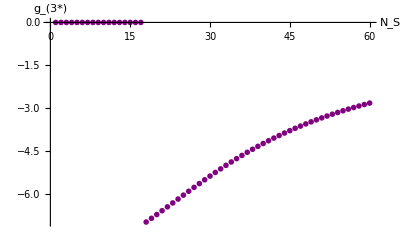

```mathematica
ListPlot[{(*Table[AllrealFPs[[i,2]],{i,1,Length[AllrealFPs]}],*)Table[g3/.FPspert[[i,2]],{i,1,Length[FPspert]}]}, PlotStyle->{Directive[Purple, PointSize->0.01]}, AxesLabel->{"N_S","g_(3*)"}, LabelStyle->16, AxesStyle->Black]
```

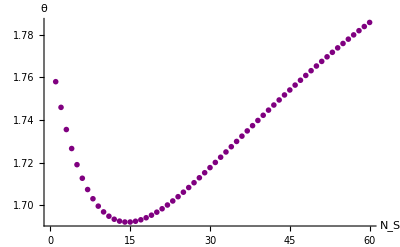

```mathematica
ListPlot[{(*Table[thetas[[i]],{i,1,Length[AllrealFPs]}],*)Table[thetaspert[[i]],{i,1,100}]}, PlotStyle->{(*Directive[Blue, PointSize->0.02],*)Directive[Purple, PointSize->0.01]}, AxesLabel->{"N_S","θ"}, LabelStyle->16, AxesStyle->Black, PlotRange->All]
```

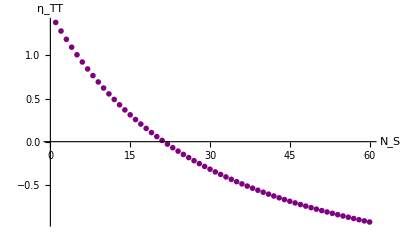

```mathematica
ListPlot[{(*Table[etahtab[[i]],{i,1,Length[AllrealFPs]}],*)Table[etahpert[[i]],{i,1,100}]}, PlotStyle->{(*Directive[Blue, PointSize->0.02],*)Directive[Purple, PointSize->0.01]}, AxesLabel->{"N_S","η_TT"}, LabelStyle->16, AxesStyle->Black, PlotRange->All]
```

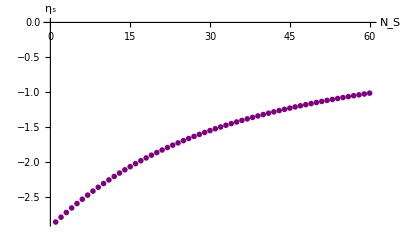

```mathematica
ListPlot[{(*Table[etastab[[i]],{i,1,Length[AllrealFPs]}],*)Table[etaspert[[i]],{i,1,100}]}, PlotStyle->{(*Directive[Blue, PointSize->0.02],*)Directive[Purple, PointSize->0.01]}, AxesLabel->{"N_S","η_s"}, LabelStyle->16, AxesStyle->Black, PlotRange->All]
```

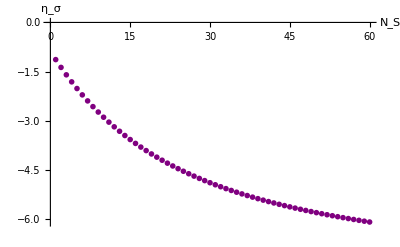

```mathematica
ListPlot[{(*Table[etaσtab[[i]],{i,1,Length[AllrealFPs]}],*)Table[etaσpert[[i]],{i,1,100}]}, PlotStyle->{(*Directive[Blue, PointSize->0.02],*)Directive[Purple, PointSize->0.01]}, AxesLabel->{"N_S","η_σ"}, LabelStyle->16, AxesStyle->Black, PlotRange->All]
```

```mathematica
βGbackground=2 G +G^2 (-15/(8π)-17/(72 π)ηh/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}) +Ns G^2/(24 π)(4-ηs/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3})
```

2 G+(G^2 Ns (4-(4 (37405 g3^3-2910 g3^3 Ns+147888 g3^2 π-5184 g3^2 Ns π+1741824 g3 π^2))/(5330 g3^3-3795 g3^3 Ns+78512 g3^2 π+5184 g3^2 Ns π+140544 g3 π^2+3981312 π^3)))/(24 π)+G^2 (-15/(8 π)-(17 (1591 g3^3-7941 g3^3 Ns+54 g3^3 Ns^2-29840 g3^2 π+14592 g3^2 Ns π-884736 g3 π^2+41472 g3 Ns π^2))/(18 π (5330 g3^3-3795 g3^3 Ns+78512 g3^2 π+5184 g3^2 Ns π+140544 g3 π^2+3981312 π^3)))

```mathematica
Gbacktab=Table[NSolve[(βGbackground/.{Ns->i}/.g3->AllrealFPs[[i,2]])==0,G],{i,1,100}]
```

{{{G→0.},{G→3.4489}},{{G→0.},{G→3.95497}},{{G→0.},{G→4.62838}},{{G→0.+0. ⅈ},{G→5.56786}},{{G→0.+0. ⅈ},{G→6.96891}},{{G→0.+0. ⅈ},{G→9.28092}},{{G→0.+0. ⅈ},{G→13.8176}},{{G→0.+0. ⅈ},{G→26.7605}},{{G→0.+0. ⅈ},{G→365.008}},{{G→-31.7262},{G→0.+0. ⅈ}},{{G→-15.2865},{G→0.+0. ⅈ}},{{G→-10.1047},{G→0.+0. ⅈ}},{{G→-7.56583},{G→0.+0. ⅈ}},{{G→-6.05843},{G→0.+0. ⅈ}},{{G→-5.05975},{G→0.+0. ⅈ}},{{G→-4.34923},{G→0.}},{{G→-3.81768},{G→0.}},{{G→-3.40491},{G→0.}},{{G→-3.07499},{G→0.}},{{G→-2.80515},{G→0.}},{{G→-2.58028},{G→0.}},{{G→-2.38993},{G→0.}},{{G→-2.22667},{G→0.}},{{G→-2.08506},{G→0.}},{{G→-1.96102},{G→0.}},{{G→-1.85144},{G→0.}},{{G→-1.75392},{G→0.}},{{G→-1.66653},{G→0.}},{{G→-1.58777},{G→0.}},{{G→-1.51639},{G→0.}},{{G→-1.4514},{G→0.}},{{G→-1.39197},{G→0.}},{{G→-1.33739},{G→0.}},{{G→-1.28709},{G→0.}},{{G→-1.24058},{G→0.}},{{G→-1.19744},{G→0.}},{{G→-1.15731},{G→0.}},{{G→-1.11988},{G→0.}},{{G→-1.08489},{G→0.}},{{G→-1.05209},{G→0.}},{{G→-1.02129},{G→0.}},{{G→-0.992305},{G→0.}},{{G→-0.964976},{G→0.}},{{G→-0.939165},{G→0.}},{{G→-0.914745},{G→0.}},{{G→-0.891606},{G→0.}},{{G→-0.869647},{G→0.}},{{G→-0.848779},{G→0.}},{{G→-0.828921},{G→0.}},{{G→-0.810001},{G→0.}},{{G→-0.791952},{G→0.}},{{G→-0.774716},{G→0.}},{{G→-0.758236},{G→0.}},{{G→-0.742464},{G→0.}},{{G→-0.727354},{G→0.}},{{G→-0.712865},{G→0.}},{{G→-0.698958},{G→0.}},{{G→-0.6856},{G→0.}},{{G→-0.672756},{G→0.}},{{G→-0.660398},{G→0.}},{{G→-0.648499},{G→0.}},{{G→-0.637032},{G→0.}},{{G→-0.625974},{G→0.}},{{G→-0.615304},{G→0.}},{{G→-0.605001},{G→0.}},{{G→-0.595045},{G→0.}},{{G→-0.585421},{G→0.}},{{G→-0.57611},{G→0.}},{{G→-0.567098},{G→0.}},{{G→-0.558371},{G→0.}},{{G→-0.549914},{G→0.}},{{G→-0.541716},{G→0.}},{{G→-0.533764},{G→0.}},{{G→-0.526048},{G→0.}},{{G→-0.518556},{G→0.}},{{G→-0.51128},{G→0.}},{{G→-0.504209},{G→0.}},{{G→-0.497336},{G→0.}},{{G→-0.490651},{G→0.}},{{G→-0.484148},{G→0.}},{{G→-0.477818},{G→0.}},{{G→-0.471655},{G→0.}},{{G→-0.465652},{G→0.}},{{G→-0.459803},{G→0.}},{{G→-0.454101},{G→0.}},{{G→-0.448543},{G→0.}},{{G→-0.443121},{G→0.}},{{G→-0.437831},{G→0.}},{{G→-0.432669},{G→0.}},{{G→-0.427629},{G→0.}},{{G→-0.422707},{G→0.}},{{G→-0.417899},{G→0.}},{{G→-0.413201},{G→0.}},{{G→-0.40861},{G→0.}},{{G→-0.404121},{G→0.}},{{G→-0.399732},{G→0.}},{{G→-0.395438},{G→0.}},{{G→-0.391237},{G→0.}},{{G→-0.387126},{G→0.}},{{G→-0.383102},{G→0.}}}

beta functions and fixed points, ignoring  internal scalars ("pure gravity" result), distinguishing η_TT and η_σ

```mathematica
ηs=0;
```

```mathematica
etah=-145/(648 π)G4(-6+ηh)+29/(324 π)G4(-6+ησ)-25/(576π)G3(-16+ηh+ησ)+G3/(216 π)(-31+5 ησ)+5 G3/(864 π)(-388+53 ηh)/.{g3->32 π g3,g4->32 π g4, g5->32 π g5}
```

-(145 G4 (-6+ηh))/(648 π)+(5 G3 (-388+53 ηh))/(864 π)+(29 G4 (-6+ησ))/(324 π)-(25 G3 (-16+ηh+ησ))/(576 π)+(G3 (-31+5 ησ))/(216 π)

```mathematica
etaσ=+G3(136 - 35 ησ)/(432π)+11 G4/(324 π)(-6+ησ)-55 G4(-6+ηh)/(648 π)+5 G3(40-23ηh)/(432 π)+5 G3(-16+ηh+ησ)/(144 π)/.{g3->32 π g3,g4->32 π g4, g5->32 π g5}
```

(5 G3 (40-23 ηh))/(432 π)-(55 G4 (-6+ηh))/(648 π)+(G3 (136-35 ησ))/(432 π)+(11 G4 (-6+ησ))/(324 π)+(5 G3 (-16+ηh+ησ))/(144 π)

```mathematica
βg3=Expand[2g3 +g3(2ηs+ηh)+2 Sqrt[g3] 1/Sqrt[32 π]((-(19(g5)^(3/2))/(10368 π^2)(-6+ησ)+95 g5^(3/2)/(20736 π^2)(-6+ηh)+g4 Sqrt[G3]/(216 Sqrt[2] π^(3/2))(-8+ησ)+5 g4 Sqrt[G3]/(864 Sqrt[2] π^(3/2))(-8+ηh))/.{g3->32 π g3,g4->32 π g4, g5->32 π g5})]
```

2 g3-(2 √g3 √G3 g4)/(3 π)-(19 √g3 g5^(3/2))/(18 π)+g3 ηh+(5 √g3 √G3 g4 ηh)/(108 π)+(95 √g3 g5^(3/2) ηh)/(324 π)+(√g3 √G3 g4 ησ)/(27 π)-(19 √g3 g5^(3/2) ησ)/(162 π)

```mathematica
etasol=Solve[{ηh==etah, ησ==etaσ},{ηh, ησ}][[1]]
```

{ηh→-(2 (5160 G3^2-6751 G3 G4+105408 G3 π-50112 G4 π))/(-2100 G3^2+4765 G3 G4-27000 G3 π+23616 G4 π+124416 π^2),ησ→-(2 (20760 G3^2-4565 G3 G4+13824 G3 π+19008 G4 π))/(2100 G3^2-4765 G3 G4+27000 G3 π-23616 G4 π-124416 π^2)}

```mathematica
etasolpert={ηh->(etah/.{ηh->0,  ησ->0}),ησ->(etaσ/.{ηh->0, ησ->0})}
```

{ηh→-(61 G3)/(36 π)+(29 G4)/(36 π),ησ→(2 G3)/(9 π)+(11 G4)/(36 π)}

```mathematica
βgetapert=βg3/.etasolpert
```

2 g3+g3 (-(61 G3)/(36 π)+(29 G4)/(36 π))-(2 √g3 √G3 g4)/(3 π)-(19 √g3 g5^(3/2))/(18 π)+(√g3 √G3 g4 ((2 G3)/(9 π)+(11 G4)/(36 π)))/(27 π)-(19 √g3 g5^(3/2) ((2 G3)/(9 π)+(11 G4)/(36 π)))/(162 π)+(5 √g3 √G3 g4 (-(61 G3)/(36 π)+(29 G4)/(36 π)))/(108 π)+(95 √g3 g5^(3/2) (-(61 G3)/(36 π)+(29 G4)/(36 π)))/(324 π)

```mathematica
βgeta=βg3/.etasol
```

2 g3-(2 √g3 √G3 g4)/(3 π)-(19 √g3 g5^(3/2))/(18 π)-(2 √g3 √G3 g4 (20760 G3^2-4565 G3 G4+13824 G3 π+19008 G4 π))/(27 π (2100 G3^2-4765 G3 G4+27000 G3 π-23616 G4 π-124416 π^2))+(19 √g3 g5^(3/2) (20760 G3^2-4565 G3 G4+13824 G3 π+19008 G4 π))/(81 π (2100 G3^2-4765 G3 G4+27000 G3 π-23616 G4 π-124416 π^2))-(2 g3 (5160 G3^2-6751 G3 G4+105408 G3 π-50112 G4 π))/(-2100 G3^2+4765 G3 G4-27000 G3 π+23616 G4 π+124416 π^2)-(5 √g3 √G3 g4 (5160 G3^2-6751 G3 G4+105408 G3 π-50112 G4 π))/(54 π (-2100 G3^2+4765 G3 G4-27000 G3 π+23616 G4 π+124416 π^2))-(95 √g3 g5^(3/2) (5160 G3^2-6751 G3 G4+105408 G3 π-50112 G4 π))/(162 π (-2100 G3^2+4765 G3 G4-27000 G3 π+23616 G4 π+124416 π^2))

```mathematica
βg3etah=Expand[2g3 +g3(ηh)+2 Sqrt[g3] 1/Sqrt[32 π]((-(19(g5)^(3/2))/(10368 π^2)(-6+ησ)+95 g5^(3/2)/(20736 π^2)(-6+ηh)+g4 Sqrt[G3]/(216 Sqrt[2] π^(3/2))(-8+ησ)+5 g4 Sqrt[G3]/(864 Sqrt[2] π^(3/2))(-8+ηh))/.{g3->32 π g3,g4->32 π g4, g5->32 π g5})]/.etasol/.Ns->0
```

2 g3-(2 √g3 √G3 g4)/(3 π)-(19 √g3 g5^(3/2))/(18 π)-(2 √g3 √G3 g4 (20760 G3^2-4565 G3 G4+13824 G3 π+19008 G4 π))/(27 π (2100 G3^2-4765 G3 G4+27000 G3 π-23616 G4 π-124416 π^2))+(19 √g3 g5^(3/2) (20760 G3^2-4565 G3 G4+13824 G3 π+19008 G4 π))/(81 π (2100 G3^2-4765 G3 G4+27000 G3 π-23616 G4 π-124416 π^2))-(2 g3 (5160 G3^2-6751 G3 G4+105408 G3 π-50112 G4 π))/(-2100 G3^2+4765 G3 G4-27000 G3 π+23616 G4 π+124416 π^2)-(5 √g3 √G3 g4 (5160 G3^2-6751 G3 G4+105408 G3 π-50112 G4 π))/(54 π (-2100 G3^2+4765 G3 G4-27000 G3 π+23616 G4 π+124416 π^2))-(95 √g3 g5^(3/2) (5160 G3^2-6751 G3 G4+105408 G3 π-50112 G4 π))/(162 π (-2100 G3^2+4765 G3 G4-27000 G3 π+23616 G4 π+124416 π^2))

```mathematica
βg3etahpert=Expand[2g3 +g3(ηh)+2 Sqrt[g3] 1/Sqrt[32 π]((-(19(g5)^(3/2))/(10368 π^2)(-6+ησ)+95 g5^(3/2)/(20736 π^2)(-6+ηh)+g4 Sqrt[G3]/(216 Sqrt[2] π^(3/2))(-8+ησ)+5 g4 Sqrt[G3]/(864 Sqrt[2] π^(3/2))(-8+ηh))/.{g3->32 π g3,g4->32 π g4, g5->32 π g5})]/.etasolpert/.Ns->0
```

2 g3+g3 (-(61 G3)/(36 π)+(29 G4)/(36 π))-(2 √g3 √G3 g4)/(3 π)-(19 √g3 g5^(3/2))/(18 π)+(√g3 √G3 g4 ((2 G3)/(9 π)+(11 G4)/(36 π)))/(27 π)-(19 √g3 g5^(3/2) ((2 G3)/(9 π)+(11 G4)/(36 π)))/(162 π)+(5 √g3 √G3 g4 (-(61 G3)/(36 π)+(29 G4)/(36 π)))/(108 π)+(95 √g3 g5^(3/2) (-(61 G3)/(36 π)+(29 G4)/(36 π)))/(324 π)

#### approximation 1: g_5=g_3, g_4=g_3, treat G_EH as parameter

```mathematica
βgeta1=βgeta/.{g5->g3,g4->g3, G3->GEH, G4->GEH}
```

2 g3-(19 g3^2)/(18 π)-(2 g3^(3/2) √GEH)/(3 π)+(19 g3^2 (16195 GEH^2+32832 GEH π))/(81 π (-2665 GEH^2+3384 GEH π-124416 π^2))-(2 g3^(3/2) √GEH (16195 GEH^2+32832 GEH π))/(27 π (-2665 GEH^2+3384 GEH π-124416 π^2))-(2 g3 (-1591 GEH^2+55296 GEH π))/(2665 GEH^2-3384 GEH π+124416 π^2)-(95 g3^2 (-1591 GEH^2+55296 GEH π))/(162 π (2665 GEH^2-3384 GEH π+124416 π^2))-(5 g3^(3/2) √GEH (-1591 GEH^2+55296 GEH π))/(54 π (2665 GEH^2-3384 GEH π+124416 π^2))

```mathematica
FPs=NSolve[(βgeta1/.{Ns->1, GEH->2}),g3]
```

{{g3→2.3927},{g3→0.}}

```mathematica
thetas=-D[βgeta1,g3]/.FPs/.GEH->2
```

{1.20425,-1.43964}

```mathematica
N[ηh/.etasol/.{g5->g3,g4->g3, G3->GEH, G4->GEH}/.FPs/.{ GEH->2}]
```

{-0.560357,-0.560357}

```mathematica
ησ/.etasol/.{g5->g3,g4->g3, G3->GEH, G4->GEH}/.FPs/.{GEH->2.}
```

{0.445349,0.445349}

```mathematica
βgetapert1=βgetapert/.{g5->g3,g4->g3,G3->GEH, G4->GEH}
```

2 g3-(209 g3^2 GEH)/(648 π^2)-(7 g3^(3/2) GEH^(3/2))/(324 π^2)-(19 g3^2)/(18 π)-(2 g3^(3/2) √GEH)/(3 π)-(8 g3 GEH)/(9 π)

```mathematica
FPspert=NSolve[(βgetapert1/.{ GEH->2}),g3]
```

{{g3→2.39272},{g3→0.}}

```mathematica
thetaspert=-D[βgetapert1,g3]/.FPspert/.GEH->2
```

{1.19722,-1.43412}

```mathematica
etah/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3}/.{ηh->0, GEH->2., ησ->0}/.FPspert
```

{-0.565884,-0.565884}

```mathematica
etaσ/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3}/.{ηh->0, GEH->2., ησ->0}/.FPspert
```

{0.335994,0.335994}

```mathematica
FPstab=Table[NSolve[(βgeta1/.{ GEH->0+i/40}),g3],{i,0,240}]
```

{{{g3→0.+0. ⅈ},{g3→5.95249}},{{g3→5.67957},{g3→0.}},{{g3→5.55046},{g3→0.}},{{g3→5.44558},{g3→0.}},{{g3→5.35348},{g3→0.}},{{g3→5.26968},{g3→0.}},{{g3→5.19189},{g3→0.}},{{g3→5.11874},{g3→0.}},{{g3→5.04932},{g3→0.}},{{g3→4.983},{g3→0.}},{{g3→4.91934},{g3→0.}},{{g3→4.85796},{g3→0.}},{{g3→4.79861},{g3→0.}},{{g3→4.74107},{g3→0.}},{{g3→4.68515},{g3→0.}},{{g3→4.63071},{g3→0.}},{{g3→4.57762},{g3→0.}},{{g3→4.52578},{g3→0.}},{{g3→4.4751},{g3→0.}},{{g3→4.4255},{g3→0.}},{{g3→4.37691},{g3→0.}},{{g3→4.32927},{g3→0.}},{{g3→4.28252},{g3→0.}},{{g3→4.23662},{g3→0.}},{{g3→4.19152},{g3→0.}},{{g3→4.14718},{g3→0.}},{{g3→4.10358},{g3→0.}},{{g3→4.06067},{g3→0.}},{{g3→4.01843},{g3→0.}},{{g3→3.97682},{g3→0.}},{{g3→3.93583},{g3→0.}},{{g3→3.89544},{g3→0.}},{{g3→3.85561},{g3→0.}},{{g3→3.81633},{g3→0.}},{{g3→3.77759},{g3→0.}},{{g3→3.73936},{g3→0.}},{{g3→3.70162},{g3→0.}},{{g3→3.66438},{g3→0.}},{{g3→3.6276},{g3→0.}},{{g3→3.59127},{g3→0.}},{{g3→3.55539},{g3→0.}},{{g3→3.51995},{g3→0.}},{{g3→3.48492},{g3→0.}},{{g3→3.4503},{g3→0.}},{{g3→3.41608},{g3→0.}},{{g3→3.38226},{g3→0.}},{{g3→3.34881},{g3→0.}},{{g3→3.31573},{g3→0.}},{{g3→3.28302},{g3→0.}},{{g3→3.25067},{g3→0.}},{{g3→3.21866},{g3→0.}},{{g3→3.187},{g3→0.}},{{g3→3.15566},{g3→0.}},{{g3→3.12466},{g3→0.}},{{g3→3.09398},{g3→0.}},{{g3→3.06361},{g3→0.}},{{g3→3.03355},{g3→0.}},{{g3→3.0038},{g3→0.}},{{g3→2.97434},{g3→0.}},{{g3→2.94518},{g3→0.}},{{g3→2.9163},{g3→0.}},{{g3→2.88771},{g3→0.}},{{g3→2.8594},{g3→0.}},{{g3→2.83136},{g3→0.}},{{g3→2.80358},{g3→0.}},{{g3→2.77608},{g3→0.}},{{g3→2.74883},{g3→0.}},{{g3→2.72184},{g3→0.}},{{g3→2.6951},{g3→0.}},{{g3→2.66861},{g3→0.}},{{g3→2.64237},{g3→0.}},{{g3→2.61637},{g3→0.}},{{g3→2.59061},{g3→0.}},{{g3→2.56508},{g3→0.}},{{g3→2.53978},{g3→0.}},{{g3→2.51472},{g3→0.}},{{g3→2.48987},{g3→0.}},{{g3→2.46526},{g3→0.}},{{g3→2.44086},{g3→0.}},{{g3→2.41667},{g3→0.}},{{g3→2.3927},{g3→0.}},{{g3→2.36894},{g3→0.}},{{g3→2.34539},{g3→0.}},{{g3→2.32205},{g3→0.}},{{g3→2.29891},{g3→0.}},{{g3→2.27597},{g3→0.}},{{g3→2.25323},{g3→0.}},{{g3→2.23068},{g3→0.}},{{g3→2.20833},{g3→0.}},{{g3→2.18617},{g3→0.}},{{g3→2.1642},{g3→0.}},{{g3→2.14241},{g3→0.}},{{g3→2.12081},{g3→0.}},{{g3→2.0994},{g3→0.}},{{g3→2.07816},{g3→0.}},{{g3→2.05711},{g3→0.}},{{g3→2.03623},{g3→0.}},{{g3→2.01552},{g3→0.}},{{g3→1.99499},{g3→0.}},{{g3→1.97463},{g3→0.}},{{g3→1.95445},{g3→0.}},{{g3→1.93442},{g3→0.}},{{g3→1.91457},{g3→0.}},{{g3→1.89488},{g3→0.}},{{g3→1.87535},{g3→0.}},{{g3→1.85598},{g3→0.}},{{g3→1.83677},{g3→0.}},{{g3→1.81772},{g3→0.}},{{g3→1.79883},{g3→0.}},{{g3→1.78009},{g3→0.}},{{g3→1.76151},{g3→0.}},{{g3→1.74307},{g3→0.}},{{g3→1.72479},{g3→0.}},{{g3→1.70666},{g3→0.}},{{g3→1.68867},{g3→0.}},{{g3→1.67083},{g3→0.}},{{g3→1.65313},{g3→0.}},{{g3→1.63558},{g3→0.}},{{g3→1.61817},{g3→0.}},{{g3→1.60091},{g3→0.}},{{g3→1.58378},{g3→0.}},{{g3→1.56679},{g3→0.}},{{g3→1.54993},{g3→0.}},{{g3→1.53322},{g3→0.}},{{g3→1.51663},{g3→0.}},{{g3→1.50019},{g3→0.}},{{g3→1.48387},{g3→0.}},{{g3→1.46768},{g3→0.}},{{g3→1.45163},{g3→0.}},{{g3→1.4357},{g3→0.}},{{g3→1.41991},{g3→0.}},{{g3→1.40424},{g3→0.}},{{g3→1.38869},{g3→0.}},{{g3→1.37327},{g3→0.}},{{g3→1.35798},{g3→0.}},{{g3→1.3428},{g3→0.}},{{g3→1.32775},{g3→0.}},{{g3→1.31282},{g3→0.}},{{g3→1.29801},{g3→0.}},{{g3→1.28332},{g3→0.}},{{g3→1.26874},{g3→0.}},{{g3→1.25429},{g3→0.}},{{g3→1.23994},{g3→0.}},{{g3→1.22572},{g3→0.}},{{g3→1.21161},{g3→0.}},{{g3→1.19761},{g3→0.}},{{g3→1.18372},{g3→0.}},{{g3→1.16995},{g3→0.}},{{g3→1.15628},{g3→0.}},{{g3→1.14273},{g3→0.}},{{g3→1.12929},{g3→0.}},{{g3→1.11595},{g3→0.}},{{g3→1.10272},{g3→0.}},{{g3→1.0896},{g3→0.}},{{g3→1.07658},{g3→0.}},{{g3→1.06367},{g3→0.}},{{g3→1.05086},{g3→0.}},{{g3→1.03816},{g3→0.}},{{g3→1.02556},{g3→0.}},{{g3→1.01306},{g3→0.}},{{g3→1.00066},{g3→0.}},{{g3→0.988366},{g3→0.}},{{g3→0.976169},{g3→0.}},{{g3→0.964071},{g3→0.}},{{g3→0.952072},{g3→0.}},{{g3→0.940171},{g3→0.}},{{g3→0.928366},{g3→0.}},{{g3→0.916658},{g3→0.}},{{g3→0.905046},{g3→0.}},{{g3→0.893528},{g3→0.}},{{g3→0.882106},{g3→0.}},{{g3→0.870777},{g3→0.}},{{g3→0.859541},{g3→0.}},{{g3→0.848397},{g3→0.}},{{g3→0.837346},{g3→0.}},{{g3→0.826386},{g3→0.}},{{g3→0.815517},{g3→0.}},{{g3→0.804737},{g3→0.}},{{g3→0.794048},{g3→0.}},{{g3→0.783447},{g3→0.}},{{g3→0.772934},{g3→0.}},{{g3→0.76251},{g3→0.}},{{g3→0.752172},{g3→0.}},{{g3→0.741921},{g3→0.}},{{g3→0.731757},{g3→0.}},{{g3→0.721677},{g3→0.}},{{g3→0.711683},{g3→0.}},{{g3→0.701774},{g3→0.}},{{g3→0.691948},{g3→0.}},{{g3→0.682206},{g3→0.}},{{g3→0.672547},{g3→0.}},{{g3→0.66297},{g3→0.}},{{g3→0.653475},{g3→0.}},{{g3→0.644062},{g3→0.}},{{g3→0.634729},{g3→0.}},{{g3→0.625477},{g3→0.}},{{g3→0.616305},{g3→0.}},{{g3→0.607213},{g3→0.}},{{g3→0.598199},{g3→0.}},{{g3→0.589264},{g3→0.}},{{g3→0.580408},{g3→0.}},{{g3→0.571629},{g3→0.}},{{g3→0.562927},{g3→0.}},{{g3→0.554302},{g3→0.}},{{g3→0.545754},{g3→0.}},{{g3→0.537281},{g3→0.}},{{g3→0.528884},{g3→0.}},{{g3→0.520563},{g3→0.}},{{g3→0.512316},{g3→0.}},{{g3→0.504143},{g3→0.}},{{g3→0.496044},{g3→0.}},{{g3→0.488019},{g3→0.}},{{g3→0.480066},{g3→0.}},{{g3→0.472187},{g3→0.}},{{g3→0.46438},{g3→0.}},{{g3→0.456645},{g3→0.}},{{g3→0.448981},{g3→0.}},{{g3→0.441389},{g3→0.}},{{g3→0.433868},{g3→0.}},{{g3→0.426417},{g3→0.}},{{g3→0.419037},{g3→0.}},{{g3→0.411726},{g3→0.}},{{g3→0.404486},{g3→0.}},{{g3→0.397314},{g3→0.}},{{g3→0.390211},{g3→0.}},{{g3→0.383177},{g3→0.}},{{g3→0.37621},{g3→0.}},{{g3→0.369312},{g3→0.}},{{g3→0.362482},{g3→0.}},{{g3→0.355719},{g3→0.}},{{g3→0.349023},{g3→0.}},{{g3→0.342393},{g3→0.}},{{g3→0.33583},{g3→0.}},{{g3→0.329334},{g3→0.}},{{g3→0.322903},{g3→0.}},{{g3→0.316538},{g3→0.}},{{g3→0.310238},{g3→0.}},{{g3→0.304004},{g3→0.}},{{g3→0.297834},{g3→0.}},{{g3→0.291729},{g3→0.}},{{g3→0.285688},{g3→0.}}}

```mathematica
FPstabSelect=Table[DeleteCases[Table[If[Abs[Im[g3/.FPstab[[i,j]]]]>0,x,If[(g3/.FPstab[[i,j]])==0,x,If[Abs[(g3/.FPstab[[i,j]])]>24,x,g3/.FPstab[[i,j]]]]],{j,1,Length[FPstab[[i]]]}],x],{i,1,Length[FPstab]}]
```

{{5.95249},{5.67957},{5.55046},{5.44558},{5.35348},{5.26968},{5.19189},{5.11874},{5.04932},{4.983},{4.91934},{4.85796},{4.79861},{4.74107},{4.68515},{4.63071},{4.57762},{4.52578},{4.4751},{4.4255},{4.37691},{4.32927},{4.28252},{4.23662},{4.19152},{4.14718},{4.10358},{4.06067},{4.01843},{3.97682},{3.93583},{3.89544},{3.85561},{3.81633},{3.77759},{3.73936},{3.70162},{3.66438},{3.6276},{3.59127},{3.55539},{3.51995},{3.48492},{3.4503},{3.41608},{3.38226},{3.34881},{3.31573},{3.28302},{3.25067},{3.21866},{3.187},{3.15566},{3.12466},{3.09398},{3.06361},{3.03355},{3.0038},{2.97434},{2.94518},{2.9163},{2.88771},{2.8594},{2.83136},{2.80358},{2.77608},{2.74883},{2.72184},{2.6951},{2.66861},{2.64237},{2.61637},{2.59061},{2.56508},{2.53978},{2.51472},{2.48987},{2.46526},{2.44086},{2.41667},{2.3927},{2.36894},{2.34539},{2.32205},{2.29891},{2.27597},{2.25323},{2.23068},{2.20833},{2.18617},{2.1642},{2.14241},{2.12081},{2.0994},{2.07816},{2.05711},{2.03623},{2.01552},{1.99499},{1.97463},{1.95445},{1.93442},{1.91457},{1.89488},{1.87535},{1.85598},{1.83677},{1.81772},{1.79883},{1.78009},{1.76151},{1.74307},{1.72479},{1.70666},{1.68867},{1.67083},{1.65313},{1.63558},{1.61817},{1.60091},{1.58378},{1.56679},{1.54993},{1.53322},{1.51663},{1.50019},{1.48387},{1.46768},{1.45163},{1.4357},{1.41991},{1.40424},{1.38869},{1.37327},{1.35798},{1.3428},{1.32775},{1.31282},{1.29801},{1.28332},{1.26874},{1.25429},{1.23994},{1.22572},{1.21161},{1.19761},{1.18372},{1.16995},{1.15628},{1.14273},{1.12929},{1.11595},{1.10272},{1.0896},{1.07658},{1.06367},{1.05086},{1.03816},{1.02556},{1.01306},{1.00066},{0.988366},{0.976169},{0.964071},{0.952072},{0.940171},{0.928366},{0.916658},{0.905046},{0.893528},{0.882106},{0.870777},{0.859541},{0.848397},{0.837346},{0.826386},{0.815517},{0.804737},{0.794048},{0.783447},{0.772934},{0.76251},{0.752172},{0.741921},{0.731757},{0.721677},{0.711683},{0.701774},{0.691948},{0.682206},{0.672547},{0.66297},{0.653475},{0.644062},{0.634729},{0.625477},{0.616305},{0.607213},{0.598199},{0.589264},{0.580408},{0.571629},{0.562927},{0.554302},{0.545754},{0.537281},{0.528884},{0.520563},{0.512316},{0.504143},{0.496044},{0.488019},{0.480066},{0.472187},{0.46438},{0.456645},{0.448981},{0.441389},{0.433868},{0.426417},{0.419037},{0.411726},{0.404486},{0.397314},{0.390211},{0.383177},{0.37621},{0.369312},{0.362482},{0.355719},{0.349023},{0.342393},{0.33583},{0.329334},{0.322903},{0.316538},{0.310238},{0.304004},{0.297834},{0.291729},{0.285688}}

```mathematica
thetastab=Table[-D[βgeta1,g3]/.{g3->FPstabSelect[[i]]}/.{GEH->(i-1)/40}/.Ns->1,{i,1,241}]
```

{{2.},{1.95294},{1.92993},{1.91092},{1.894},{1.87841},{1.86379},{1.84989},{1.83658},{1.82375},{1.81132},{1.79924},{1.78747},{1.77595},{1.76468},{1.75362},{1.74275},{1.73207},{1.72154},{1.71117},{1.70093},{1.69083},{1.68084},{1.67097},{1.66121},{1.65155},{1.64198},{1.63251},{1.62312},{1.61382},{1.60459},{1.59544},{1.58636},{1.57735},{1.5684},{1.55952},{1.55071},{1.54195},{1.53325},{1.5246},{1.51601},{1.50747},{1.49898},{1.49054},{1.48214},{1.4738},{1.46549},{1.45724},{1.44902},{1.44085},{1.43272},{1.42462},{1.41657},{1.40855},{1.40058},{1.39263},{1.38473},{1.37686},{1.36902},{1.36122},{1.35345},{1.34571},{1.338},{1.33033},{1.32269},{1.31507},{1.30749},{1.29994},{1.29241},{1.28492},{1.27745},{1.27001},{1.2626},{1.25521},{1.24785},{1.24052},{1.23322},{1.22594},{1.21868},{1.21145},{1.20425},{1.19707},{1.18991},{1.18278},{1.17567},{1.16859},{1.16152},{1.15449},{1.14747},{1.14048},{1.13351},{1.12656},{1.11964},{1.11273},{1.10585},{1.09899},{1.09215},{1.08533},{1.07854},{1.07176},{1.06501},{1.05827},{1.05156},{1.04487},{1.0382},{1.03154},{1.02491},{1.0183},{1.01171},{1.00513},{0.998581},{0.992047},{0.985533},{0.979039},{0.972563},{0.966107},{0.959669},{0.953251},{0.946851},{0.940471},{0.934109},{0.927766},{0.921441},{0.915135},{0.908847},{0.902577},{0.896326},{0.890094},{0.883879},{0.877682},{0.871504},{0.865344},{0.859201},{0.853077},{0.84697},{0.840881},{0.83481},{0.828757},{0.822722},{0.816704},{0.810703},{0.804721},{0.798756},{0.792808},{0.786878},{0.780965},{0.77507},{0.769192},{0.763331},{0.757488},{0.751662},{0.745853},{0.740062},{0.734287},{0.72853},{0.72279},{0.717068},{0.711362},{0.705674},{0.700002},{0.694348},{0.688711},{0.683091},{0.677488},{0.671902},{0.666333},{0.660781},{0.655245},{0.649727},{0.644226},{0.638742},{0.633275},{0.627825},{0.622392},{0.616975},{0.611576},{0.606194},{0.600828},{0.59548},{0.590148},{0.584833},{0.579536},{0.574255},{0.568991},{0.563744},{0.558514},{0.553301},{0.548105},{0.542926},{0.537764},{0.532619},{0.52749},{0.522379},{0.517285},{0.512208},{0.507147},{0.502104},{0.497078},{0.492069},{0.487077},{0.482101},{0.477143},{0.472202},{0.467279},{0.462372},{0.457482},{0.45261},{0.447755},{0.442916},{0.438095},{0.433292},{0.428505},{0.423736},{0.418984},{0.414249},{0.409532},{0.404832},{0.400149},{0.395484},{0.390836},{0.386205},{0.381592},{0.376997},{0.372419},{0.367858},{0.363315},{0.35879},{0.354282},{0.349792},{0.345319},{0.340864},{0.336427},{0.332008},{0.327606},{0.323223},{0.318857},{0.314509},{0.310179},{0.305867},{0.301573},{0.297298}}

```mathematica
etahtab=Table[ηh/.etasol/.{G3->GEH, G4->GEH,g4->g3}/.{g3->FPstabSelect[[i]]}/.{GEH->(i-1.)/40},{i,1,241}]
```

{0.,-0.00707345,-0.0141467,-0.0212196,-0.0282922,-0.0353643,-0.0424361,-0.0495072,-0.0565778,-0.0636478,-0.070717,-0.0777855,-0.0848532,-0.09192,-0.0989859,-0.106051,-0.113115,-0.120177,-0.127239,-0.134299,-0.141358,-0.148416,-0.155473,-0.162527,-0.169581,-0.176633,-0.183683,-0.190731,-0.197778,-0.204823,-0.211866,-0.218907,-0.225946,-0.232983,-0.240019,-0.247051,-0.254082,-0.26111,-0.268137,-0.27516,-0.282181,-0.2892,-0.296216,-0.30323,-0.310241,-0.317249,-0.324254,-0.331257,-0.338256,-0.345253,-0.352246,-0.359237,-0.366224,-0.373208,-0.380189,-0.387167,-0.394141,-0.401111,-0.408079,-0.415042,-0.422002,-0.428959,-0.435911,-0.44286,-0.449805,-0.456746,-0.463684,-0.470617,-0.477546,-0.484471,-0.491392,-0.498308,-0.505221,-0.512128,-0.519032,-0.525931,-0.532826,-0.539715,-0.546601,-0.553481,-0.560357,-0.567228,-0.574094,-0.580956,-0.587812,-0.594663,-0.601509,-0.60835,-0.615186,-0.622016,-0.628842,-0.635662,-0.642476,-0.649285,-0.656088,-0.662886,-0.669678,-0.676465,-0.683245,-0.69002,-0.696789,-0.703553,-0.71031,-0.717061,-0.723806,-0.730545,-0.737277,-0.744004,-0.750724,-0.757438,-0.764145,-0.770846,-0.777541,-0.784229,-0.79091,-0.797584,-0.804252,-0.810913,-0.817568,-0.824215,-0.830855,-0.837489,-0.844115,-0.850735,-0.857347,-0.863952,-0.870549,-0.87714,-0.883723,-0.890299,-0.896867,-0.903428,-0.909981,-0.916526,-0.923064,-0.929595,-0.936117,-0.942632,-0.949139,-0.955638,-0.962129,-0.968612,-0.975087,-0.981553,-0.988012,-0.994463,-1.0009,-1.00734,-1.01376,-1.02018,-1.02659,-1.03299,-1.03938,-1.04577,-1.05214,-1.05851,-1.06486,-1.07121,-1.07755,-1.08388,-1.0902,-1.09652,-1.10282,-1.10912,-1.1154,-1.12168,-1.12795,-1.1342,-1.14045,-1.14669,-1.15292,-1.15915,-1.16536,-1.17156,-1.17775,-1.18393,-1.19011,-1.19627,-1.20243,-1.20857,-1.2147,-1.22083,-1.22694,-1.23305,-1.23914,-1.24523,-1.2513,-1.25737,-1.26342,-1.26947,-1.2755,-1.28153,-1.28754,-1.29355,-1.29954,-1.30552,-1.31149,-1.31746,-1.32341,-1.32935,-1.33528,-1.3412,-1.34711,-1.35301,-1.3589,-1.36477,-1.37064,-1.3765,-1.38234,-1.38817,-1.394,-1.39981,-1.40561,-1.4114,-1.41718,-1.42294,-1.4287,-1.43445,-1.44018,-1.4459,-1.45161,-1.45732,-1.463,-1.46868,-1.47435,-1.48,-1.48565,-1.49128,-1.4969,-1.50251,-1.5081,-1.51369,-1.51926,-1.52482,-1.53037,-1.53591,-1.54144,-1.54695,-1.55246,-1.55795,-1.56343}

```mathematica
etaσtab=Table[ησ/.etasol/.{g5->g3,g4->g3}/.{G3->GEH, G4->GEH}/.{g3->FPstabSelect[[i]]}/.{GEH->(i-1.)/40},{i,1,241}]
```

{0.,0.00421732,0.00846941,0.0127563,0.0170779,0.0214342,0.0258253,0.0302511,0.0347116,0.0392067,0.0437366,0.048301,0.0529001,0.0575338,0.0622021,0.066905,0.0716424,0.0764143,0.0812208,0.0860617,0.0909372,0.095847,0.100791,0.10577,0.110783,0.11583,0.120912,0.126028,0.131178,0.136363,0.141582,0.146834,0.152121,0.157443,0.162798,0.168187,0.173611,0.179068,0.184559,0.190085,0.195644,0.201237,0.206864,0.212524,0.218219,0.223947,0.229709,0.235504,0.241333,0.247196,0.253092,0.259021,0.264985,0.270981,0.277011,0.283074,0.289171,0.2953,0.301463,0.307659,0.313888,0.320151,0.326446,0.332774,0.339135,0.345529,0.351956,0.358416,0.364908,0.371433,0.37799,0.384581,0.391203,0.397859,0.404546,0.411266,0.418018,0.424803,0.43162,0.438468,0.445349,0.452262,0.459207,0.466184,0.473193,0.480233,0.487306,0.49441,0.501545,0.508712,0.515911,0.523141,0.530403,0.537695,0.545019,0.552375,0.559761,0.567178,0.574627,0.582106,0.589616,0.597157,0.604729,0.612331,0.619964,0.627628,0.635322,0.643046,0.650801,0.658585,0.6664,0.674246,0.682121,0.690026,0.697961,0.705926,0.71392,0.721945,0.729999,0.738082,0.746195,0.754337,0.762508,0.770709,0.778939,0.787198,0.795485,0.803802,0.812148,0.820522,0.828925,0.837356,0.845816,0.854305,0.862822,0.871367,0.87994,0.888541,0.89717,0.905828,0.914513,0.923225,0.931966,0.940734,0.949529,0.958352,0.967203,0.97608,0.984985,0.993917,1.00288,1.01186,1.02087,1.02991,1.03898,1.04807,1.05719,1.06633,1.07551,1.0847,1.09393,1.10318,1.11245,1.12175,1.13108,1.14043,1.14981,1.15921,1.16864,1.1781,1.18757,1.19708,1.20661,1.21616,1.22574,1.23534,1.24497,1.25462,1.2643,1.274,1.28373,1.29348,1.30325,1.31305,1.32287,1.33271,1.34258,1.35247,1.36239,1.37233,1.38229,1.39227,1.40228,1.41231,1.42236,1.43244,1.44254,1.45266,1.4628,1.47297,1.48316,1.49336,1.5036,1.51385,1.52413,1.53442,1.54474,1.55508,1.56544,1.57582,1.58623,1.59665,1.6071,1.61756,1.62805,1.63856,1.64909,1.65964,1.6702,1.68079,1.6914,1.70203,1.71268,1.72335,1.73404,1.74474,1.75547,1.76622,1.77698,1.78777,1.79857,1.80939,1.82023,1.83109,1.84197,1.85287,1.86378,1.87472,1.88567,1.89664,1.90762}

```mathematica
FPstabpert=Table[NSolve[(βgetapert1/.{Ns->1, GEH->0+i/40}),g3],{i,0,240}]
```

{{{g3→0.+0. ⅈ},{g3→5.95249}},{{g3→5.67958},{g3→0.}},{{g3→5.5505},{g3→0.}},{{g3→5.44567},{g3→0.}},{{g3→5.35362},{g3→0.}},{{g3→5.26989},{g3→0.}},{{g3→5.19219},{g3→0.}},{{g3→5.11913},{g3→0.}},{{g3→5.04981},{g3→0.}},{{g3→4.98361},{g3→0.}},{{g3→4.92007},{g3→0.}},{{g3→4.85882},{g3→0.}},{{g3→4.79961},{g3→0.}},{{g3→4.7422},{g3→0.}},{{g3→4.68642},{g3→0.}},{{g3→4.63213},{g3→0.}},{{g3→4.57919},{g3→0.}},{{g3→4.52751},{g3→0.}},{{g3→4.47698},{g3→0.}},{{g3→4.42754},{g3→0.}},{{g3→4.3791},{g3→0.}},{{g3→4.33162},{g3→0.}},{{g3→4.28503},{g3→0.}},{{g3→4.23928},{g3→0.}},{{g3→4.19433},{g3→0.}},{{g3→4.15015},{g3→0.}},{{g3→4.1067},{g3→0.}},{{g3→4.06393},{g3→0.}},{{g3→4.02183},{g3→0.}},{{g3→3.98037},{g3→0.}},{{g3→3.93952},{g3→0.}},{{g3→3.89925},{g3→0.}},{{g3→3.85955},{g3→0.}},{{g3→3.8204},{g3→0.}},{{g3→3.78177},{g3→0.}},{{g3→3.74365},{g3→0.}},{{g3→3.70602},{g3→0.}},{{g3→3.66887},{g3→0.}},{{g3→3.63218},{g3→0.}},{{g3→3.59595},{g3→0.}},{{g3→3.56014},{g3→0.}},{{g3→3.52477},{g3→0.}},{{g3→3.4898},{g3→0.}},{{g3→3.45524},{g3→0.}},{{g3→3.42107},{g3→0.}},{{g3→3.38728},{g3→0.}},{{g3→3.35386},{g3→0.}},{{g3→3.32081},{g3→0.}},{{g3→3.28811},{g3→0.}},{{g3→3.25576},{g3→0.}},{{g3→3.22374},{g3→0.}},{{g3→3.19206},{g3→0.}},{{g3→3.16071},{g3→0.}},{{g3→3.12967},{g3→0.}},{{g3→3.09894},{g3→0.}},{{g3→3.06852},{g3→0.}},{{g3→3.0384},{g3→0.}},{{g3→3.00857},{g3→0.}},{{g3→2.97903},{g3→0.}},{{g3→2.94977},{g3→0.}},{{g3→2.92078},{g3→0.}},{{g3→2.89207},{g3→0.}},{{g3→2.86363},{g3→0.}},{{g3→2.83545},{g3→0.}},{{g3→2.80753},{g3→0.}},{{g3→2.77986},{g3→0.}},{{g3→2.75244},{g3→0.}},{{g3→2.72527},{g3→0.}},{{g3→2.69834},{g3→0.}},{{g3→2.67165},{g3→0.}},{{g3→2.64519},{g3→0.}},{{g3→2.61896},{g3→0.}},{{g3→2.59295},{g3→0.}},{{g3→2.56718},{g3→0.}},{{g3→2.54162},{g3→0.}},{{g3→2.51628},{g3→0.}},{{g3→2.49115},{g3→0.}},{{g3→2.46623},{g3→0.}},{{g3→2.44152},{g3→0.}},{{g3→2.41702},{g3→0.}},{{g3→2.39272},{g3→0.}},{{g3→2.36862},{g3→0.}},{{g3→2.34471},{g3→0.}},{{g3→2.321},{g3→0.}},{{g3→2.29748},{g3→0.}},{{g3→2.27415},{g3→0.}},{{g3→2.25101},{g3→0.}},{{g3→2.22805},{g3→0.}},{{g3→2.20528},{g3→0.}},{{g3→2.18268},{g3→0.}},{{g3→2.16026},{g3→0.}},{{g3→2.13802},{g3→0.}},{{g3→2.11595},{g3→0.}},{{g3→2.09405},{g3→0.}},{{g3→2.07233},{g3→0.}},{{g3→2.05077},{g3→0.}},{{g3→2.02937},{g3→0.}},{{g3→2.00814},{g3→0.}},{{g3→1.98708},{g3→0.}},{{g3→1.96617},{g3→0.}},{{g3→1.94542},{g3→0.}},{{g3→1.92483},{g3→0.}},{{g3→1.90439},{g3→0.}},{{g3→1.88411},{g3→0.}},{{g3→1.86398},{g3→0.}},{{g3→1.844},{g3→0.}},{{g3→1.82417},{g3→0.}},{{g3→1.80448},{g3→0.}},{{g3→1.78495},{g3→0.}},{{g3→1.76555},{g3→0.}},{{g3→1.7463},{g3→0.}},{{g3→1.72719},{g3→0.}},{{g3→1.70822},{g3→0.}},{{g3→1.6894},{g3→0.}},{{g3→1.6707},{g3→0.}},{{g3→1.65215},{g3→0.}},{{g3→1.63373},{g3→0.}},{{g3→1.61544},{g3→0.}},{{g3→1.59729},{g3→0.}},{{g3→1.57927},{g3→0.}},{{g3→1.56137},{g3→0.}},{{g3→1.54361},{g3→0.}},{{g3→1.52598},{g3→0.}},{{g3→1.50847},{g3→0.}},{{g3→1.49109},{g3→0.}},{{g3→1.47383},{g3→0.}},{{g3→1.4567},{g3→0.}},{{g3→1.43969},{g3→0.}},{{g3→1.4228},{g3→0.}},{{g3→1.40603},{g3→0.}},{{g3→1.38938},{g3→0.}},{{g3→1.37286},{g3→0.}},{{g3→1.35644},{g3→0.}},{{g3→1.34015},{g3→0.}},{{g3→1.32397},{g3→0.}},{{g3→1.30791},{g3→0.}},{{g3→1.29196},{g3→0.}},{{g3→1.27613},{g3→0.}},{{g3→1.26041},{g3→0.}},{{g3→1.2448},{g3→0.}},{{g3→1.2293},{g3→0.}},{{g3→1.21391},{g3→0.}},{{g3→1.19863},{g3→0.}},{{g3→1.18346},{g3→0.}},{{g3→1.1684},{g3→0.}},{{g3→1.15344},{g3→0.}},{{g3→1.13859},{g3→0.}},{{g3→1.12385},{g3→0.}},{{g3→1.10921},{g3→0.}},{{g3→1.09468},{g3→0.}},{{g3→1.08025},{g3→0.}},{{g3→1.06592},{g3→0.}},{{g3→1.0517},{g3→0.}},{{g3→1.03758},{g3→0.}},{{g3→1.02356},{g3→0.}},{{g3→1.00964},{g3→0.}},{{g3→0.995817},{g3→0.}},{{g3→0.982097},{g3→0.}},{{g3→0.968476},{g3→0.}},{{g3→0.954953},{g3→0.}},{{g3→0.941528},{g3→0.}},{{g3→0.9282},{g3→0.}},{{g3→0.914969},{g3→0.}},{{g3→0.901834},{g3→0.}},{{g3→0.888795},{g3→0.}},{{g3→0.875851},{g3→0.}},{{g3→0.863002},{g3→0.}},{{g3→0.850247},{g3→0.}},{{g3→0.837587},{g3→0.}},{{g3→0.825019},{g3→0.}},{{g3→0.812545},{g3→0.}},{{g3→0.800163},{g3→0.}},{{g3→0.787874},{g3→0.}},{{g3→0.775676},{g3→0.}},{{g3→0.76357},{g3→0.}},{{g3→0.751554},{g3→0.}},{{g3→0.739629},{g3→0.}},{{g3→0.727795},{g3→0.}},{{g3→0.71605},{g3→0.}},{{g3→0.704395},{g3→0.}},{{g3→0.69283},{g3→0.}},{{g3→0.681353},{g3→0.}},{{g3→0.669965},{g3→0.}},{{g3→0.658665},{g3→0.}},{{g3→0.647454},{g3→0.}},{{g3→0.63633},{g3→0.}},{{g3→0.625293},{g3→0.}},{{g3→0.614344},{g3→0.}},{{g3→0.603482},{g3→0.}},{{g3→0.592707},{g3→0.}},{{g3→0.582019},{g3→0.}},{{g3→0.571417},{g3→0.}},{{g3→0.560901},{g3→0.}},{{g3→0.550471},{g3→0.}},{{g3→0.540127},{g3→0.}},{{g3→0.529868},{g3→0.}},{{g3→0.519695},{g3→0.}},{{g3→0.509608},{g3→0.}},{{g3→0.499606},{g3→0.}},{{g3→0.489689},{g3→0.}},{{g3→0.479857},{g3→0.}},{{g3→0.47011},{g3→0.}},{{g3→0.460448},{g3→0.}},{{g3→0.450871},{g3→0.}},{{g3→0.441379},{g3→0.}},{{g3→0.431971},{g3→0.}},{{g3→0.422648},{g3→0.}},{{g3→0.41341},{g3→0.}},{{g3→0.404257},{g3→0.}},{{g3→0.395189},{g3→0.}},{{g3→0.386205},{g3→0.}},{{g3→0.377306},{g3→0.}},{{g3→0.368493},{g3→0.}},{{g3→0.359764},{g3→0.}},{{g3→0.35112},{g3→0.}},{{g3→0.342562},{g3→0.}},{{g3→0.334089},{g3→0.}},{{g3→0.325702},{g3→0.}},{{g3→0.3174},{g3→0.}},{{g3→0.309184},{g3→0.}},{{g3→0.301055},{g3→0.}},{{g3→0.293012},{g3→0.}},{{g3→0.285055},{g3→0.}},{{g3→0.277185},{g3→0.}},{{g3→0.269403},{g3→0.}},{{g3→0.261708},{g3→0.}},{{g3→0.254101},{g3→0.}},{{g3→0.246582},{g3→0.}},{{g3→0.239152},{g3→0.}},{{g3→0.231811},{g3→0.}},{{g3→0.224559},{g3→0.}},{{g3→0.217397},{g3→0.}},{{g3→0.210326},{g3→0.}},{{g3→0.203346},{g3→0.}},{{g3→0.196457},{g3→0.}},{{g3→0.189661},{g3→0.}},{{g3→0.182957},{g3→0.}},{{g3→0.176347},{g3→0.}},{{g3→0.169831},{g3→0.}},{{g3→0.16341},{g3→0.}},{{g3→0.157085},{g3→0.}}}

```mathematica
FPstabSelectpert=Table[DeleteCases[Table[If[Abs[Im[g3/.FPstabpert[[i,j]]]]>0,x,If[(g3/.FPstabpert[[i,j]])==0,x,If[Abs[(g3/.FPstabpert[[i,j]])]>22.7,x,g3/.FPstabpert[[i,j]]]]],{j,1,Length[FPstabpert[[i]]]}],x],{i,1,Length[FPstabpert]}]
```

{{5.95249},{5.67958},{5.5505},{5.44567},{5.35362},{5.26989},{5.19219},{5.11913},{5.04981},{4.98361},{4.92007},{4.85882},{4.79961},{4.7422},{4.68642},{4.63213},{4.57919},{4.52751},{4.47698},{4.42754},{4.3791},{4.33162},{4.28503},{4.23928},{4.19433},{4.15015},{4.1067},{4.06393},{4.02183},{3.98037},{3.93952},{3.89925},{3.85955},{3.8204},{3.78177},{3.74365},{3.70602},{3.66887},{3.63218},{3.59595},{3.56014},{3.52477},{3.4898},{3.45524},{3.42107},{3.38728},{3.35386},{3.32081},{3.28811},{3.25576},{3.22374},{3.19206},{3.16071},{3.12967},{3.09894},{3.06852},{3.0384},{3.00857},{2.97903},{2.94977},{2.92078},{2.89207},{2.86363},{2.83545},{2.80753},{2.77986},{2.75244},{2.72527},{2.69834},{2.67165},{2.64519},{2.61896},{2.59295},{2.56718},{2.54162},{2.51628},{2.49115},{2.46623},{2.44152},{2.41702},{2.39272},{2.36862},{2.34471},{2.321},{2.29748},{2.27415},{2.25101},{2.22805},{2.20528},{2.18268},{2.16026},{2.13802},{2.11595},{2.09405},{2.07233},{2.05077},{2.02937},{2.00814},{1.98708},{1.96617},{1.94542},{1.92483},{1.90439},{1.88411},{1.86398},{1.844},{1.82417},{1.80448},{1.78495},{1.76555},{1.7463},{1.72719},{1.70822},{1.6894},{1.6707},{1.65215},{1.63373},{1.61544},{1.59729},{1.57927},{1.56137},{1.54361},{1.52598},{1.50847},{1.49109},{1.47383},{1.4567},{1.43969},{1.4228},{1.40603},{1.38938},{1.37286},{1.35644},{1.34015},{1.32397},{1.30791},{1.29196},{1.27613},{1.26041},{1.2448},{1.2293},{1.21391},{1.19863},{1.18346},{1.1684},{1.15344},{1.13859},{1.12385},{1.10921},{1.09468},{1.08025},{1.06592},{1.0517},{1.03758},{1.02356},{1.00964},{0.995817},{0.982097},{0.968476},{0.954953},{0.941528},{0.9282},{0.914969},{0.901834},{0.888795},{0.875851},{0.863002},{0.850247},{0.837587},{0.825019},{0.812545},{0.800163},{0.787874},{0.775676},{0.76357},{0.751554},{0.739629},{0.727795},{0.71605},{0.704395},{0.69283},{0.681353},{0.669965},{0.658665},{0.647454},{0.63633},{0.625293},{0.614344},{0.603482},{0.592707},{0.582019},{0.571417},{0.560901},{0.550471},{0.540127},{0.529868},{0.519695},{0.509608},{0.499606},{0.489689},{0.479857},{0.47011},{0.460448},{0.450871},{0.441379},{0.431971},{0.422648},{0.41341},{0.404257},{0.395189},{0.386205},{0.377306},{0.368493},{0.359764},{0.35112},{0.342562},{0.334089},{0.325702},{0.3174},{0.309184},{0.301055},{0.293012},{0.285055},{0.277185},{0.269403},{0.261708},{0.254101},{0.246582},{0.239152},{0.231811},{0.224559},{0.217397},{0.210326},{0.203346},{0.196457},{0.189661},{0.182957},{0.176347},{0.169831},{0.16341},{0.157085}}

```mathematica
Export["plotdata1a.dat",(N[Table[{(i-1)/40,FPstabSelect[[i,1]]},{i,1,241}]]),"Table"];
Export["plotdata1b.dat",(N[Table[{(i-1)/40,FPstabSelectpert[[i,1]]},{i,1,241}]]),"Table"];
```

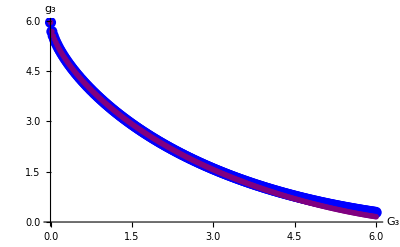

```mathematica
ListPlot[{Table[{(i-1)/40,FPstabSelect[[i,1]]},{i,1,241}],Table[{(i-1)/40,FPstabSelectpert[[i,1]]},{i,1,241}]},AxesLabel->{"G_3","g_3"}, LabelStyle->16,AxesStyle->Black, PlotStyle->{Directive[Blue, PointSize->0.02], Directive[Purple, PointSize->0.01]}]
```

```mathematica
thetastabpert=Table[-D[βgetapert1,g3]/.{g3->FPstabSelectpert[[i]]}/.{GEH->(i-1)/40},{i,1,241}]
```

{{2.},{1.95293},{1.92993},{1.91092},{1.89399},{1.87841},{1.86378},{1.84988},{1.83656},{1.82372},{1.81129},{1.79919},{1.7874},{1.77588},{1.76459},{1.75351},{1.74263},{1.73192},{1.72138},{1.71098},{1.70072},{1.69058},{1.68057},{1.67067},{1.66087},{1.65118},{1.64157},{1.63206},{1.62263},{1.61328},{1.604},{1.5948},{1.58567},{1.5766},{1.5676},{1.55866},{1.54978},{1.54095},{1.53218},{1.52346},{1.51479},{1.50618},{1.4976},{1.48908},{1.4806},{1.47216},{1.46377},{1.45541},{1.4471},{1.43882},{1.43058},{1.42238},{1.41421},{1.40608},{1.39798},{1.38992},{1.38189},{1.37389},{1.36591},{1.35797},{1.35006},{1.34218},{1.33433},{1.3265},{1.3187},{1.31093},{1.30318},{1.29546},{1.28776},{1.28009},{1.27245},{1.26482},{1.25722},{1.24965},{1.24209},{1.23456},{1.22705},{1.21956},{1.21209},{1.20465},{1.19722},{1.18981},{1.18243},{1.17506},{1.16771},{1.16039},{1.15308},{1.14579},{1.13852},{1.13126},{1.12403},{1.11681},{1.10961},{1.10243},{1.09526},{1.08811},{1.08098},{1.07386},{1.06677},{1.05968},{1.05262},{1.04556},{1.03853},{1.03151},{1.02451},{1.01752},{1.01054},{1.00358},{0.99664},{0.989711},{0.982796},{0.975896},{0.96901},{0.962139},{0.955282},{0.948438},{0.941609},{0.934794},{0.927992},{0.921204},{0.914429},{0.907669},{0.900921},{0.894187},{0.887466},{0.880758},{0.874063},{0.867381},{0.860712},{0.854056},{0.847413},{0.840782},{0.834164},{0.827559},{0.820966},{0.814386},{0.807819},{0.801263},{0.79472},{0.78819},{0.781671},{0.775165},{0.768671},{0.762189},{0.755719},{0.749261},{0.742816},{0.736382},{0.72996},{0.723551},{0.717153},{0.710767},{0.704393},{0.698031},{0.69168},{0.685342},{0.679015},{0.6727},{0.666397},{0.660106},{0.653826},{0.647558},{0.641302},{0.635058},{0.628826},{0.622605},{0.616396},{0.610199},{0.604014},{0.597841},{0.591679},{0.585529},{0.579391},{0.573265},{0.567151},{0.561048},{0.554958},{0.548879},{0.542813},{0.536758},{0.530716},{0.524686},{0.518667},{0.512661},{0.506667},{0.500686},{0.494716},{0.488759},{0.482814},{0.476882},{0.470962},{0.465055},{0.45916},{0.453278},{0.447408},{0.441552},{0.435708},{0.429877},{0.424059},{0.418254},{0.412463},{0.406684},{0.400919},{0.395167},{0.389429},{0.383704},{0.377993},{0.372296},{0.366613},{0.360943},{0.355288},{0.349647},{0.34402},{0.338408},{0.332811},{0.327228},{0.32166},{0.316107},{0.31057},{0.305047},{0.299541},{0.294049},{0.288574},{0.283115},{0.277672},{0.272245},{0.266835},{0.261442},{0.256065},{0.250706},{0.245365},{0.240041},{0.234735},{0.229447},{0.224177},{0.218926},{0.213695},{0.208482},{0.203289},{0.198116},{0.192964}}

```mathematica
Export["plotdata2a.dat",(N[Table[{(i-1)/40,thetastab[[i,1]]},{i,1,241}]]),"Table"];
Export["plotdata2b.dat",(N[Table[{(i-1)/40,thetastabpert[[i,1]]},{i,1,241}]]),"Table"];
```

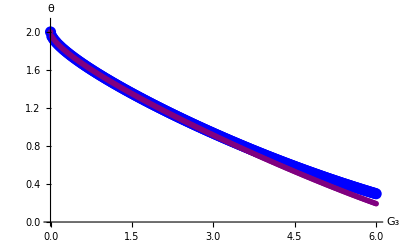

```mathematica
ListPlot[{Table[{(i-1)/40,thetastab[[i,1]]},{i,1,241}],Table[{(i-1)/40,thetastabpert[[i,1]]},{i,1,241}]},AxesLabel->{"G_3","θ"}, LabelStyle->16,AxesStyle->Black,PlotStyle->{Directive[Blue, PointSize->0.02], Directive[Purple, PointSize->0.01]},PlotRange->{0,2.1}]
```

```mathematica
etahtabpert=Table[etah/.{ηh->0, ηs->0,G3->GEH, G4->GEH,ησ->0}/.{g3->FPstabSelectpert[[i]]}/.{GEH->(i-1.)/40},{i,1,241}]
```

{0.,-0.00707355,-0.0141471,-0.0212207,-0.0282942,-0.0353678,-0.0424413,-0.0495149,-0.0565884,-0.063662,-0.0707355,-0.0778091,-0.0848826,-0.0919562,-0.0990297,-0.106103,-0.113177,-0.12025,-0.127324,-0.134398,-0.141471,-0.148545,-0.155618,-0.162692,-0.169765,-0.176839,-0.183912,-0.190986,-0.198059,-0.205133,-0.212207,-0.21928,-0.226354,-0.233427,-0.240501,-0.247574,-0.254648,-0.261721,-0.268795,-0.275869,-0.282942,-0.290016,-0.297089,-0.304163,-0.311236,-0.31831,-0.325383,-0.332457,-0.339531,-0.346604,-0.353678,-0.360751,-0.367825,-0.374898,-0.381972,-0.389045,-0.396119,-0.403193,-0.410266,-0.41734,-0.424413,-0.431487,-0.43856,-0.445634,-0.452707,-0.459781,-0.466854,-0.473928,-0.481002,-0.488075,-0.495149,-0.502222,-0.509296,-0.516369,-0.523443,-0.530516,-0.53759,-0.544664,-0.551737,-0.558811,-0.565884,-0.572958,-0.580031,-0.587105,-0.594178,-0.601252,-0.608326,-0.615399,-0.622473,-0.629546,-0.63662,-0.643693,-0.650767,-0.65784,-0.664914,-0.671988,-0.679061,-0.686135,-0.693208,-0.700282,-0.707355,-0.714429,-0.721502,-0.728576,-0.73565,-0.742723,-0.749797,-0.75687,-0.763944,-0.771017,-0.778091,-0.785164,-0.792238,-0.799311,-0.806385,-0.813459,-0.820532,-0.827606,-0.834679,-0.841753,-0.848826,-0.8559,-0.862973,-0.870047,-0.877121,-0.884194,-0.891268,-0.898341,-0.905415,-0.912488,-0.919562,-0.926635,-0.933709,-0.940783,-0.947856,-0.95493,-0.962003,-0.969077,-0.97615,-0.983224,-0.990297,-0.997371,-1.00444,-1.01152,-1.01859,-1.02567,-1.03274,-1.03981,-1.04689,-1.05396,-1.06103,-1.06811,-1.07518,-1.08225,-1.08933,-1.0964,-1.10347,-1.11055,-1.11762,-1.12469,-1.13177,-1.13884,-1.14592,-1.15299,-1.16006,-1.16714,-1.17421,-1.18128,-1.18836,-1.19543,-1.2025,-1.20958,-1.21665,-1.22372,-1.2308,-1.23787,-1.24495,-1.25202,-1.25909,-1.26617,-1.27324,-1.28031,-1.28739,-1.29446,-1.30153,-1.30861,-1.31568,-1.32275,-1.32983,-1.3369,-1.34398,-1.35105,-1.35812,-1.3652,-1.37227,-1.37934,-1.38642,-1.39349,-1.40056,-1.40764,-1.41471,-1.42178,-1.42886,-1.43593,-1.443,-1.45008,-1.45715,-1.46423,-1.4713,-1.47837,-1.48545,-1.49252,-1.49959,-1.50667,-1.51374,-1.52081,-1.52789,-1.53496,-1.54203,-1.54911,-1.55618,-1.56326,-1.57033,-1.5774,-1.58448,-1.59155,-1.59862,-1.6057,-1.61277,-1.61984,-1.62692,-1.63399,-1.64106,-1.64814,-1.65521,-1.66228,-1.66936,-1.67643,-1.68351,-1.69058,-1.69765}

```mathematica
etaσtabpert=Table[etaσ/.{ηh->0, ηs->0,g5->g3,g4->g3,ησ->0}/.{G3->GEH, G4->GEH}/.{g3->FPstabSelectpert[[i]]}/.{GEH->(i-1.)/40},{i,1,241}]
```

{0.,0.00419992,0.00839984,0.0125998,0.0167997,0.0209996,0.0251995,0.0293995,0.0335994,0.0377993,0.0419992,0.0461991,0.0503991,0.054599,0.0587989,0.0629988,0.0671988,0.0713987,0.0755986,0.0797985,0.0839984,0.0881984,0.0923983,0.0965982,0.100798,0.104998,0.109198,0.113398,0.117598,0.121798,0.125998,0.130198,0.134398,0.138597,0.142797,0.146997,0.151197,0.155397,0.159597,0.163797,0.167997,0.172197,0.176397,0.180597,0.184797,0.188996,0.193196,0.197396,0.201596,0.205796,0.209996,0.214196,0.218396,0.222596,0.226796,0.230996,0.235196,0.239396,0.243595,0.247795,0.251995,0.256195,0.260395,0.264595,0.268795,0.272995,0.277195,0.281395,0.285595,0.289795,0.293995,0.298194,0.302394,0.306594,0.310794,0.314994,0.319194,0.323394,0.327594,0.331794,0.335994,0.340194,0.344394,0.348594,0.352793,0.356993,0.361193,0.365393,0.369593,0.373793,0.377993,0.382193,0.386393,0.390593,0.394793,0.398993,0.403193,0.407392,0.411592,0.415792,0.419992,0.424192,0.428392,0.432592,0.436792,0.440992,0.445192,0.449392,0.453592,0.457792,0.461991,0.466191,0.470391,0.474591,0.478791,0.482991,0.487191,0.491391,0.495591,0.499791,0.503991,0.508191,0.51239,0.51659,0.52079,0.52499,0.52919,0.53339,0.53759,0.54179,0.54599,0.55019,0.55439,0.55859,0.56279,0.566989,0.571189,0.575389,0.579589,0.583789,0.587989,0.592189,0.596389,0.600589,0.604789,0.608989,0.613189,0.617389,0.621588,0.625788,0.629988,0.634188,0.638388,0.642588,0.646788,0.650988,0.655188,0.659388,0.663588,0.667788,0.671988,0.676187,0.680387,0.684587,0.688787,0.692987,0.697187,0.701387,0.705587,0.709787,0.713987,0.718187,0.722387,0.726587,0.730786,0.734986,0.739186,0.743386,0.747586,0.751786,0.755986,0.760186,0.764386,0.768586,0.772786,0.776986,0.781186,0.785385,0.789585,0.793785,0.797985,0.802185,0.806385,0.810585,0.814785,0.818985,0.823185,0.827385,0.831585,0.835784,0.839984,0.844184,0.848384,0.852584,0.856784,0.860984,0.865184,0.869384,0.873584,0.877784,0.881984,0.886184,0.890383,0.894583,0.898783,0.902983,0.907183,0.911383,0.915583,0.919783,0.923983,0.928183,0.932383,0.936583,0.940783,0.944982,0.949182,0.953382,0.957582,0.961782,0.965982,0.970182,0.974382,0.978582,0.982782,0.986982,0.991182,0.995382,0.999581,1.00378,1.00798}

```mathematica
Export["plotdata3a.dat",(Table[{(i-1)/40,etahtab[[i]]},{i,1,241}]//N),"Table"];
Export["plotdata3b.dat",(Table[{(i-1)/40,etahtabpert[[i]]},{i,1,241}]//N),"Table"];
```

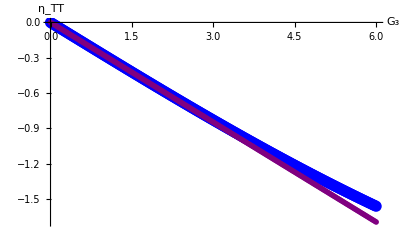

```mathematica
ListPlot[{Table[{(i-1)/40,etahtab[[i]]},{i,1,241}],Table[{(i-1)/40,etahtabpert[[i]]},{i,1,241}]},AxesLabel->{"G_3","η_TT"}, LabelStyle->16,AxesStyle->Black,PlotStyle->{Directive[Blue, PointSize->0.02], Directive[Purple, PointSize->0.01]},PlotRange->All]
```

```mathematica
Export["plotdata4a.dat",(Table[{(i-1)/40,etaσtab[[i]]},{i,1,241}]//N),"Table"];
Export["plotdata4b.dat",(Table[{(i-1)/40,etaσtabpert[[i]]},{i,1,241}]//N),"Table"];
```

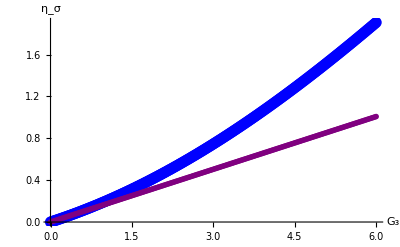

```mathematica
ListPlot[{Table[{(i-1)/40,etaσtab[[i]]},{i,1,241}],Table[{(i-1)/40,etaσtabpert[[i]]},{i,1,241}]},AxesLabel->{"G_3","η_σ"}, LabelStyle->16,AxesStyle->Black,PlotStyle->{Directive[Blue, PointSize->0.02], Directive[Purple, PointSize->0.01]},PlotRange->All]
```

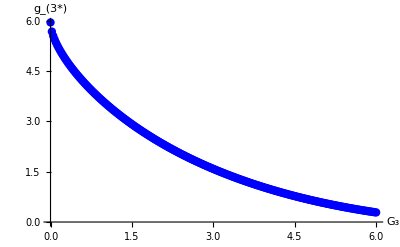

```mathematica
ListPlot[{Table[{(i-1)/40,FPstabSelect[[i,1]]},{i,1,241}]},AxesLabel->{"G_3","g_(3*)"}, LabelStyle->16,AxesStyle->Black, PlotStyle->{Directive[Blue, PointSize->0.015], Directive[Purple, PointSize->0.01]}]
```

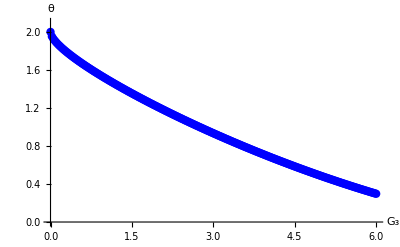

```mathematica
ListPlot[{Table[{(i-1)/40,thetastab[[i,1]]},{i,1,241}]},AxesLabel->{"G_3","θ"}, LabelStyle->16,AxesStyle->Black,PlotStyle->{Directive[Blue, PointSize->0.015], Directive[Purple, PointSize->0.01]},PlotRange->{0,2.1}]
```

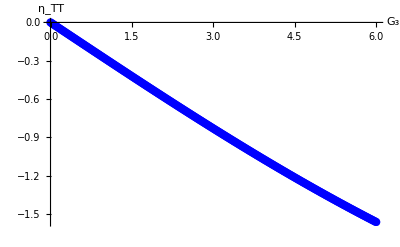

```mathematica
ListPlot[{Table[{(i-1)/40,etahtab[[i]]},{i,1,241}]},AxesLabel->{"G_3","η_TT"}, LabelStyle->16,AxesStyle->Black,PlotStyle->{Directive[Blue, PointSize->0.015], Directive[Purple, PointSize->0.01]},PlotRange->All]
```

#### approximation 1: g_5=g_3, g_4=g_3, G_EH=g_3

```mathematica
βgeta2=βgeta/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}
```

2 g3-(31 g3^2)/(18 π)+(13 g3^2 (16195 g3^2+32832 g3 π))/(81 π (-2665 g3^2+3384 g3 π-124416 π^2))-(2 g3 (-1591 g3^2+55296 g3 π))/(2665 g3^2-3384 g3 π+124416 π^2)-(55 g3^2 (-1591 g3^2+55296 g3 π))/(81 π (2665 g3^2-3384 g3 π+124416 π^2))

```mathematica
βg3/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}
```

2 g3-(31 g3^2)/(18 π)+g3 ηh+(55 g3^2 ηh)/(162 π)-(13 g3^2 ησ)/(162 π)

```mathematica
FullSimplify[etah/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}]
```

(2 g3 (1591 g3-55296 π))/(2665 g3^2-3384 g3 π+124416 π^2)

```mathematica
FullSimplify[etah/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}]/.g3->1.
```

-0.282181

```mathematica
FullSimplify[etaσ/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}]/.g3->1.
```

0.195644

```mathematica
FullSimplify[etaσ/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}]
```

(2 g3 (16195 g3+32832 π))/(2665 g3^2-3384 g3 π+124416 π^2)

```mathematica
βgetapert2=βgetapert/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}
```

2 g3-(223 g3^3)/(648 π^2)-(47 g3^2)/(18 π)

```mathematica
βgetapert2/.Ns->10
```

2 g3-(223 g3^3)/(648 π^2)-(47 g3^2)/(18 π)

```mathematica
FPs=NSolve[(βgeta2/.{Ns->1}),g3]
```

{{g3→-8.42465+22.4049 ⅈ},{g3→-8.42465-22.4049 ⅈ},{g3→2.20441},{g3→0.}}

```mathematica
thetas=-D[βgeta2,g3]/.FPs/.Ns->1
```

{32.3426+25.5044 ⅈ,32.3426-25.5044 ⅈ,2.1651,-2.}

```mathematica
ηh/.etasol/.{G3->GEH, G4->GEH, g4->g3}/.GEH->g3/.FPs
```

{7.25761+0.265205 ⅈ,7.25761-0.265205 ⅈ,-0.616391,0.}

```mathematica
ησ/.etasol/.{G3->GEH, G4->GEH, g4->g3}/.GEH->g3/.FPs
```

{4.32069-13.203 ⅈ,4.32069+13.203 ⅈ,0.502806,0.}

```mathematica
FPspert=NSolve[(βgetapert2),g3]
```

{{g3→-26.0394},{g3→0.+0. ⅈ},{g3→2.20277}}

```mathematica
thetaspert=-D[βgetapert2,g3]/.FPspert
```

{25.6425,-2.+0. ⅈ,2.16919}

```mathematica
etah/.{ηh->0, ησ->0}/.{G3->GEH, G4->GEH, g4->g3}/.GEH->g3/.FPspert
```

{7.36765,0.+0. ⅈ,-0.623255}

```mathematica
etaσ/.{ηh->0, ησ->0}/.{G3->GEH, G4->GEH, g4->g3}/.GEH->g3/.FPspert
```

{-4.37454,0.+0. ⅈ,0.370058}

```mathematica
NSolve[(βg3/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}/.{ηh->0, ησ->0})==0,g3]
```

{{g3→0.},{g3→3.6483}}

#### approximation 1: g_5=g_3, g_4=g_3, G_EH=g_3, identify η_σ=η_TT

```mathematica
βgeta2=(βg3/.{ησ->ηh})/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}
```

2 g3-(31 g3^2)/(18 π)-(2 g3 (-1591 g3^2+55296 g3 π))/(2665 g3^2-3384 g3 π+124416 π^2)-(14 g3^2 (-1591 g3^2+55296 g3 π))/(27 π (2665 g3^2-3384 g3 π+124416 π^2))

```mathematica
etasoleq=Solve[{ηh==(etah/.ησ->ηh)},ηh][[1]]
```

{ηh→-(12 (61 G3-29 G4))/(-105 G3+58 G4+432 π)}

```mathematica
βgetatest=(βg3/.{ησ->ηh})/.etasoleq/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}
```

2 g3-(31 g3^2)/(18 π)-(384 g3^2)/(-47 g3+432 π)-(896 g3^3)/(9 π (-47 g3+432 π))

```mathematica
etasoleqp=Solve[{ηh==(etah/.{ησ->0, ηh->0})},ηh][[1]]
```

{ηh→(-61 G3+29 G4)/(36 π)}

```mathematica
βgetapert2=(βg3/.{ησ->ηh})/.etasoleqp/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}
```

2 g3-(56 g3^3)/(243 π^2)-(47 g3^2)/(18 π)

```mathematica
βgetapert2/.Ns->1
```

2 g3-(56 g3^3)/(243 π^2)-(47 g3^2)/(18 π)

```mathematica
FPs=NSolve[(βgetatest/.{Ns->1}),g3]
```

{{g3→-208.474},{g3→2.19781},{g3→0.}}

```mathematica
thetas=-D[βgetatest,g3]/.FPs/.Ns->1
```

{23.3235,2.18759,-2.}

```mathematica
ηh/.etasoleq/.{G3->GEH, G4->GEH, g4->g3}/.GEH->g3/.FPs
```

{7.17623,-0.673082,0.}

```mathematica
FPspert=NSolve[(βgetapert2),g3]
```

{{g3→-37.8579},{g3→0.+0. ⅈ},{g3→2.26252}}

```mathematica
thetaspert=-D[βgetapert2,g3]/.FPspert
```

{35.4653,-2.+0. ⅈ,2.11953}

```mathematica
etah/.{ηh->0, ησ->0}/.{G3->GEH, G4->GEH, g4->g3}/.GEH->g3/.FPspert
```

{10.7116,0.+0. ⅈ,-0.640161}

#### approximation 1: g_5=g_3, g_4=g_3, G_EH=g_3+ background Newton coupling

```mathematica
βgeta2=βgeta/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}
```

2 g3-(31 g3^2)/(18 π)+(13 g3^2 (16195 g3^2+32832 g3 π))/(81 π (-2665 g3^2+3384 g3 π-124416 π^2))-(2 g3 (-1591 g3^2+55296 g3 π))/(2665 g3^2-3384 g3 π+124416 π^2)-(55 g3^2 (-1591 g3^2+55296 g3 π))/(81 π (2665 g3^2-3384 g3 π+124416 π^2))

```mathematica
FPs=NSolve[(βgeta2),g3]
```

{{g3→-8.42465+22.4049 ⅈ},{g3→-8.42465-22.4049 ⅈ},{g3→2.20441},{g3→0.}}

```mathematica
ηh/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}/.FPs[[3]]
```

-0.616391

```mathematica
ησ/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}/.FPs[[3]]
```

0.502806

```mathematica
βGbackground=2 G +G^2 (-15/(8π)+5/(18 π)(ηh/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3})-ησ/24/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}) +Ns G^2/(24 π)(4-ηs/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3})/.FPs[[3]]/.Ns->0
```

2 G-0.672282 G^2

```mathematica
FP=NSolve[βGbackground==0,G]
```

{{G→0.},{G→2.97494}}

```mathematica
-D[βGbackground,G]/.FP
```

{-2.,2.}

beta functions and fixed points, no anomalous dimensions

```mathematica
ηs=0;
```

```mathematica
ηh=0;
```

```mathematica
ησ=0;
```

```mathematica
βg3=Expand[2g3 +g3(2ηs+ηh)+2 Sqrt[g3] 1/Sqrt[32 π]((-g3^(3/2)/(2560 π^2)(-30 +ησ+2 ηs)-g3 Sqrt[G3]/(Sqrt[2] π^(3/2)320)(-30+2 ησ +ηs)+5Sqrt[g3] g4/(2304 π^2)(-16+ησ+ηs)-(19(g5)^(3/2))/(10368 π^2)(-6+ησ)+95 g5^(3/2)/(20736 π^2)(-6+ηh)+g4 Sqrt[G3]/(216 Sqrt[2] π^(3/2))(-8+ησ)+5 g4 Sqrt[G3]/(864 Sqrt[2] π^(3/2))(-8+ηh))/.{g3->32 π g3,g4->32 π g4, g5->32 π g5})]
```

2 g3+(3 g3^2)/(4 π)+(3 g3^(3/2) √G3)/(4 π)-(20 g3 g4)/(9 π)-(2 √g3 √G3 g4)/(3 π)-(19 √g3 g5^(3/2))/(18 π)

```mathematica
βg3puregrav=Expand[2g3 +g3(2ηs+ηh)+2 Sqrt[g3] 1/Sqrt[32 π]((-(19(g5)^(3/2))/(10368 π^2)(-6+ησ)+95 g5^(3/2)/(20736 π^2)(-6+ηh)+g4 Sqrt[G3]/(216 Sqrt[2] π^(3/2))(-8+ησ)+5 g4 Sqrt[G3]/(864 Sqrt[2] π^(3/2))(-8+ηh))/.{g3->32 π g3,g4->32 π g4, g5->32 π g5})]
```

2 g3-(2 √g3 √G3 g4)/(3 π)-(19 √g3 g5^(3/2))/(18 π)

#### approximation 1: treat g_4, g_5, G_EH as parameters (G3=G4)

```mathematica
βgeta0=βg3/.{G4->0, G3->0, g4->0, g5->0}
```

2 g3+(3 g3^2)/(2 π)

```mathematica
FP=NSolve[(βgeta0/.Ns->1)==0,g3]
```

{{g3→-4.18879},{g3→0.}}

```mathematica
theta=-D[βgeta0,g3]/.Ns->1/.FP
```

{2.,-2.}

```mathematica
βgeta0puregrav=βg3puregrav/.{G4->2, G3->2, g4->2, g5->2}
```

2 g3-(5 √2 √g3)/(9 π)

```mathematica
FP=NSolve[βgeta0puregrav==0,g3]
```

{{g3→0.015636},{g3→0.}}

```mathematica
theta=-D[βgeta0puregrav,g3]/.FP
```

Power::infy: Infinite expression 1/√0. encountered.

{-1.,ComplexInfinity}

#### approximation 1: g_5=g_3, g_4=g_3, G_EH=g_3

```mathematica
βgeta2=βg3/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}
```

2 g3-(22 g3^2)/(9 π)

```mathematica
FPs=NSolve[(βgeta2/.{Ns->1}),g3]
```

{{g3→0.},{g3→2.57039}}

```mathematica
thetas=-D[βgeta2,g3]/.FPs/.Ns->1
```

{-2.,2.}

```mathematica
βg2puregrav=βg3puregrav/.{g5->g3}
```

2 g3-(19 g3^2)/(18 π)-(2 √g3 √G3 g4)/(3 π)

```mathematica
FPpuregrav=NSolve[(βg2puregrav/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3})==0,g3]
```

{{g3→0.},{g3→3.6483}}

```mathematica
thetaspuregrav=-D[βg2puregrav,g3]/.FPpuregrav/.Ns->1
```

Power::infy: Infinite expression 1/√0. encountered.

{ComplexInfinity,0.451613+0.0555499 √G3 g4}

beta functions and fixed points, only graviton anomalous dimensions

```mathematica
ηs=0;
```

```mathematica
etah=Ns g3/(768 π^2)-145/(648 π)G4(-6+ηh)+29/(324 π)G4(-6+ησ)-25/(576π)G3(-16+ηh+ησ)+G3/(216 π)(-31+5 ησ)+5 G3/(864 π)(-388+53 ηh)/.{g3->32 π g3,g4->32 π g4, g5->32 π g5}
```

(g3 Ns)/(24 π)-(145 G4 (-6+ηh))/(648 π)+(5 G3 (-388+53 ηh))/(864 π)+(29 G4 (-6+ησ))/(324 π)-(25 G3 (-16+ηh+ησ))/(576 π)+(G3 (-31+5 ησ))/(216 π)

```mathematica
etaσ=g3(8-3 ηs)/(1536 π^2)Ns+G3(136 - 35 ησ)/(432π)+11 G4/(324 π)(-6+ησ)-55 G4(-6+ηh)/(648 π)+5 G3(40-23ηh)/(432 π)+5 G3(-16+ηh+ησ)/(144 π)/.{g3->32 π g3,g4->32 π g4, g5->32 π g5}
```

(g3 Ns)/(6 π)+(5 G3 (40-23 ηh))/(432 π)-(55 G4 (-6+ηh))/(648 π)+(G3 (136-35 ησ))/(432 π)+(11 G4 (-6+ησ))/(324 π)+(5 G3 (-16+ηh+ησ))/(144 π)

```mathematica
βg3=Expand[2g3 +g3(2ηs+ηh)+2 Sqrt[g3] 1/Sqrt[32 π]((-g3^(3/2)/(2560 π^2)(-30 +ησ+2 ηs)-g3 Sqrt[G3]/(Sqrt[2] π^(3/2)320)(-30+2 ησ +ηs)+5Sqrt[g3] g4/(2304 π^2)(-16+ησ+ηs)-(19(g5)^(3/2))/(10368 π^2)(-6+ησ)+95 g5^(3/2)/(20736 π^2)(-6+ηh)+g4 Sqrt[G3]/(216 Sqrt[2] π^(3/2))(-8+ησ)+5 g4 Sqrt[G3]/(864 Sqrt[2] π^(3/2))(-8+ηh))/.{g3->32 π g3,g4->32 π g4, g5->32 π g5})]
```

2 g3+(3 g3^2)/(4 π)+(3 g3^(3/2) √G3)/(4 π)-(20 g3 g4)/(9 π)-(2 √g3 √G3 g4)/(3 π)-(19 √g3 g5^(3/2))/(18 π)+g3 ηh+(5 √g3 √G3 g4 ηh)/(108 π)+(95 √g3 g5^(3/2) ηh)/(324 π)-(g3^2 ησ)/(40 π)-(g3^(3/2) √G3 ησ)/(20 π)+(5 g3 g4 ησ)/(36 π)+(√g3 √G3 g4 ησ)/(27 π)-(19 √g3 g5^(3/2) ησ)/(162 π)

```mathematica
etasol=Solve[{ηh==etah, ησ==etaσ},{ηh, ησ}]
```

{{ηh→-(2 (5160 G3^2-6751 G3 G4+90 g3 G3 Ns-840 g3 G4 Ns+105408 G3 π-50112 G4 π-2592 g3 Ns π))/(-2100 G3^2+4765 G3 G4-27000 G3 π+23616 G4 π+124416 π^2),ησ→-(2 (20760 G3^2-4565 G3 G4-3330 g3 G3 Ns+2100 g3 G4 Ns+13824 G3 π+19008 G4 π+10368 g3 Ns π))/(2100 G3^2-4765 G3 G4+27000 G3 π-23616 G4 π-124416 π^2)}}

```mathematica
etapert={etah/.{ηh->0, ησ->0},etaσ/.{ηh->0, ησ->0}}
```

{-(61 G3)/(36 π)+(29 G4)/(36 π)+(g3 Ns)/(24 π),(2 G3)/(9 π)+(11 G4)/(36 π)+(g3 Ns)/(6 π)}

```mathematica
βgfull=(βg3/.etasol)[[1]]
```

2 g3+(3 g3^2)/(4 π)+(3 g3^(3/2) √G3)/(4 π)-(20 g3 g4)/(9 π)-(2 √g3 √G3 g4)/(3 π)-(19 √g3 g5^(3/2))/(18 π)+(g3^2 (20760 G3^2-4565 G3 G4-3330 g3 G3 Ns+2100 g3 G4 Ns+13824 G3 π+19008 G4 π+10368 g3 Ns π))/(20 π (2100 G3^2-4765 G3 G4+27000 G3 π-23616 G4 π-124416 π^2))+(g3^(3/2) √G3 (20760 G3^2-4565 G3 G4-3330 g3 G3 Ns+2100 g3 G4 Ns+13824 G3 π+19008 G4 π+10368 g3 Ns π))/(10 π (2100 G3^2-4765 G3 G4+27000 G3 π-23616 G4 π-124416 π^2))-(5 g3 g4 (20760 G3^2-4565 G3 G4-3330 g3 G3 Ns+2100 g3 G4 Ns+13824 G3 π+19008 G4 π+10368 g3 Ns π))/(18 π (2100 G3^2-4765 G3 G4+27000 G3 π-23616 G4 π-124416 π^2))-(2 √g3 √G3 g4 (20760 G3^2-4565 G3 G4-3330 g3 G3 Ns+2100 g3 G4 Ns+13824 G3 π+19008 G4 π+10368 g3 Ns π))/(27 π (2100 G3^2-4765 G3 G4+27000 G3 π-23616 G4 π-124416 π^2))+(19 √g3 g5^(3/2) (20760 G3^2-4565 G3 G4-3330 g3 G3 Ns+2100 g3 G4 Ns+13824 G3 π+19008 G4 π+10368 g3 Ns π))/(81 π (2100 G3^2-4765 G3 G4+27000 G3 π-23616 G4 π-124416 π^2))-(2 g3 (5160 G3^2-6751 G3 G4+90 g3 G3 Ns-840 g3 G4 Ns+105408 G3 π-50112 G4 π-2592 g3 Ns π))/(-2100 G3^2+4765 G3 G4-27000 G3 π+23616 G4 π+124416 π^2)-(5 √g3 √G3 g4 (5160 G3^2-6751 G3 G4+90 g3 G3 Ns-840 g3 G4 Ns+105408 G3 π-50112 G4 π-2592 g3 Ns π))/(54 π (-2100 G3^2+4765 G3 G4-27000 G3 π+23616 G4 π+124416 π^2))-(95 √g3 g5^(3/2) (5160 G3^2-6751 G3 G4+90 g3 G3 Ns-840 g3 G4 Ns+105408 G3 π-50112 G4 π-2592 g3 Ns π))/(162 π (-2100 G3^2+4765 G3 G4-27000 G3 π+23616 G4 π+124416 π^2))

```mathematica
βgpert=βg3/.{ηh->etapert[[1]],ησ->etapert[[2]]}
```

2 g3+g3 (-(61 G3)/(36 π)+(29 G4)/(36 π)+(g3 Ns)/(24 π))+(3 g3^2)/(4 π)+(3 g3^(3/2) √G3)/(4 π)-(20 g3 g4)/(9 π)-(2 √g3 √G3 g4)/(3 π)-(19 √g3 g5^(3/2))/(18 π)+(5 √g3 √G3 g4 (-(61 G3)/(36 π)+(29 G4)/(36 π)+(g3 Ns)/(24 π)))/(108 π)+(95 √g3 g5^(3/2) (-(61 G3)/(36 π)+(29 G4)/(36 π)+(g3 Ns)/(24 π)))/(324 π)-(g3^2 ((2 G3)/(9 π)+(11 G4)/(36 π)+(g3 Ns)/(6 π)))/(40 π)-(g3^(3/2) √G3 ((2 G3)/(9 π)+(11 G4)/(36 π)+(g3 Ns)/(6 π)))/(20 π)+(5 g3 g4 ((2 G3)/(9 π)+(11 G4)/(36 π)+(g3 Ns)/(6 π)))/(36 π)+(√g3 √G3 g4 ((2 G3)/(9 π)+(11 G4)/(36 π)+(g3 Ns)/(6 π)))/(27 π)-(19 √g3 g5^(3/2) ((2 G3)/(9 π)+(11 G4)/(36 π)+(g3 Ns)/(6 π)))/(162 π)

#### approximation 1: g_5=g_3, g_4=g_3, G_EH=g_3

```mathematica
βgeta2=βgfull/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}
```

2 g3-(22 g3^2)/(9 π)+(53 g3^2 (16195 g3^2-1230 g3^2 Ns+32832 g3 π+10368 g3 Ns π))/(1620 π (-2665 g3^2+3384 g3 π-124416 π^2))-(2 g3 (-1591 g3^2-750 g3^2 Ns+55296 g3 π-2592 g3 Ns π))/(2665 g3^2-3384 g3 π+124416 π^2)-(55 g3^2 (-1591 g3^2-750 g3^2 Ns+55296 g3 π-2592 g3 Ns π))/(81 π (2665 g3^2-3384 g3 π+124416 π^2))

```mathematica
βg3/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}
```

2 g3-(22 g3^2)/(9 π)+g3 ηh+(55 g3^2 ηh)/(162 π)-(53 g3^2 ησ)/(3240 π)

```mathematica
βgetapert2=βgpert/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}
```

2 g3+g3 (-(8 g3)/(9 π)+(g3 Ns)/(24 π))-(22 g3^2)/(9 π)+(55 g3^2 (-(8 g3)/(9 π)+(g3 Ns)/(24 π)))/(162 π)-(53 g3^2 ((19 g3)/(36 π)+(g3 Ns)/(6 π)))/(3240 π)

```mathematica
Series[βgeta2,{Ns,0,1},{g3,0,2}]
```

(2 g3-(10 g3^2)/(3 π)+O[g3]^3)+(g3^2/(24 π)+O[g3]^3) Ns+O[Ns]^2

```mathematica
Series[βgetapert2,{Ns,0,1},{g3,0,2}]
```

(2 g3-(10 g3^2)/(3 π)+O[g3]^3)+(g3^2/(24 π)+O[g3]^3) Ns+O[Ns]^2

```mathematica
FPtab=Table[NSolve[(βgeta2/.{Ns->i})==0,g3],{i,0,30}]
```

{{{g3→-6.64809+26.0222 ⅈ},{g3→-6.64809-26.0222 ⅈ},{g3→1.79338},{g3→0.}},{{g3→-6.39864+27.2253 ⅈ},{g3→-6.39864-27.2253 ⅈ},{g3→1.82181},{g3→0.}},{{g3→-6.09021+28.627 ⅈ},{g3→-6.09021-28.627 ⅈ},{g3→1.8514},{g3→0.}},{{g3→-5.70009+30.2878 ⅈ},{g3→-5.70009-30.2878 ⅈ},{g3→1.88224},{g3→0.}},{{g3→-5.1923+32.2984 ⅈ},{g3→-5.1923-32.2984 ⅈ},{g3→1.91442},{g3→0.}},{{g3→-4.50623+34.7999 ⅈ},{g3→-4.50623-34.7999 ⅈ},{g3→1.94804},{g3→0.}},{{g3→-3.5313+38.0292 ⅈ},{g3→-3.5313-38.0292 ⅈ},{g3→1.98323},{g3→0.}},{{g3→-2.04209+42.4206 ⅈ},{g3→-2.04209-42.4206 ⅈ},{g3→2.02013},{g3→0.}},{{g3→0.502917+48.8844 ⅈ},{g3→0.502917-48.8844 ⅈ},{g3→2.05888},{g3→0.}},{{g3→5.81405+59.784 ⅈ},{g3→5.81405-59.784 ⅈ},{g3→2.09966},{g3→0.}},{{g3→23.6181+84.3818 ⅈ},{g3→23.6181-84.3818 ⅈ},{g3→2.14267},{g3→0.}},{{g3→-492.594},{g3→88.8885},{g3→2.18814},{g3→0.}},{{g3→-115.522},{g3→47.4012},{g3→2.23635},{g3→0.}},{{g3→-80.6931},{g3→35.4347},{g3→2.28761},{g3→0.}},{{g3→-65.8806},{g3→28.917},{g3→2.3423},{g3→0.}},{{g3→-57.3096},{g3→24.6097},{g3→2.40086},{g3→0.}},{{g3→-51.5853},{g3→21.4651},{g3→2.46385},{g3→0.}},{{g3→-47.4281},{g3→19.0225},{g3→2.53194},{g3→0.}},{{g3→-44.2381},{g3→17.0423},{g3→2.60596},{g3→0.}},{{g3→-41.6928},{g3→15.3846},{g3→2.68701},{g3→0.}},{{g3→-39.602},{g3→13.9611},{g3→2.77648},{g3→0.}},{{g3→-37.8454},{g3→12.7124},{g3→2.87626},{g3→0.}},{{g3→-36.3429},{g3→11.5958},{g3→2.989},{g3→0.}},{{g3→-35.0388},{g3→10.5787},{g3→3.11856},{g3→0.}},{{g3→-33.893},{g3→9.63367},{g3→3.27095},{g3→0.}},{{g3→-32.8759},{g3→8.73433},{g3→3.45645},{g3→0.}},{{g3→-31.9651},{g3→7.84792},{g3→3.69524},{g3→0.}},{{g3→-31.1433},{g3→6.9127},{g3→4.03921},{g3→0.}},{{g3→-30.3968},{g3→5.58926},{g3→4.81981},{g3→0.}},{{g3→-29.7147},{g3→4.95411+1.22301 ⅈ},{g3→4.95411-1.22301 ⅈ},{g3→0.}},{{g3→-29.0882},{g3→4.72203+1.70672 ⅈ},{g3→4.72203-1.70672 ⅈ},{g3→0.}}}

```mathematica
FPtabSelect=Table[DeleteCases[Table[If[Abs[Im[g3/.FPtab[[i,j]]]]>0,x,If[(g3/.FPtab[[i,j]])==0,x,If[Abs[(g3/.FPtab[[i,j]])]>5.5,x,FPtab[[i,j]]]]],{j,1,4}],x],{i,1,Length[FPtab]}]
```

{{{g3→1.79338}},{{g3→1.82181}},{{g3→1.8514}},{{g3→1.88224}},{{g3→1.91442}},{{g3→1.94804}},{{g3→1.98323}},{{g3→2.02013}},{{g3→2.05888}},{{g3→2.09966}},{{g3→2.14267}},{{g3→2.18814}},{{g3→2.23635}},{{g3→2.28761}},{{g3→2.3423}},{{g3→2.40086}},{{g3→2.46385}},{{g3→2.53194}},{{g3→2.60596}},{{g3→2.68701}},{{g3→2.77648}},{{g3→2.87626}},{{g3→2.989}},{{g3→3.11856}},{{g3→3.27095}},{{g3→3.45645}},{{g3→3.69524}},{{g3→4.03921}},{{g3→4.81981}},{},{}}

```mathematica
thetatab=Table[-D[(βgeta2/.Ns->i-1),g3]/.FPtabSelect[[i]],{i,1,28}]
```

{{2.09292},{2.08598},{2.07851},{2.07046},{2.06178},{2.05239},{2.04223},{2.03121},{2.01923},{2.00618},{1.99194},{1.97634},{1.9592},{1.94031},{1.91942},{1.89619},{1.87025},{1.8411},{1.80812},{1.77052},{1.72721},{1.67675},{1.61705},{1.54504},{1.45584},{1.34096},{1.18342},{0.938779}}

```mathematica
etahtab=Table[etah/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}/.Ns->i-1/.FPtabSelect[[i]][[1]],{i,1,28}]
```

{{-0.50339},{-0.482787},{-0.461437},{-0.43929},{-0.416289},{-0.392373},{-0.367472},{-0.341507},{-0.314391},{-0.286024},{-0.256293},{-0.225066},{-0.192195},{-0.157502},{-0.120782},{-0.08179},{-0.0402301},{0.00425745},{0.0521189},{0.103918},{0.160385},{0.22249},{0.29157},{0.369559},{0.459425},{0.566161},{0.69943},{0.883575}}

```mathematica
etaσtab=Table[etaσ/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}/.Ns->i-1/.FPtabSelect[[i]][[1]],{i,1,28}]
```

{{0.389446},{0.487787},{0.589212},{0.693909},{0.802087},{0.913973},{1.02982},{1.14992},{1.27457},{1.40414},{1.53902},{1.67968},{1.82664},{1.98049},{2.14195},{2.31184},{2.49116},{2.68109},{2.8831},{3.09902},{3.33118},{3.58266},{3.85764},{4.16207},{4.50498},{4.90129},{5.37941},{6.00953}}

```mathematica
FPtabpert=Table[NSolve[(βgetapert2/.{Ns->i})==0,g3],{i,0,50}]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
FPtabSelectpert=Table[DeleteCases[Table[If[Abs[Im[g3/.FPtabpert[[i,j]]]]>0,x,If[(g3/.FPtabpert[[i,j]])≤0,x,If[(g3/.FPtabpert[[i,j]])>8,x,FPtabpert[[i,j]]]]],{j,1,3}],x],{i,1,Length[FPtabpert]}]
```

{{{g3→1.78998}},{{g3→1.8137}},{{g3→1.83812}},{{g3→1.86327}},{{g3→1.88919}},{{g3→1.91591}},{{g3→1.94347}},{{g3→1.97192}},{{g3→2.0013}},{{g3→2.03167}},{{g3→2.06309}},{{g3→2.0956}},{{g3→2.12928}},{{g3→2.1642}},{{g3→2.20043}},{{g3→2.23805}},{{g3→2.27715}},{{g3→2.31784}},{{g3→2.36022}},{{g3→2.40442}},{{g3→2.45056}},{{g3→2.49879}},{{g3→2.54928}},{{g3→2.60221}},{{g3→2.65777}},{{g3→2.71621}},{{g3→2.77779}},{{g3→2.84279}},{{g3→2.91156}},{{g3→2.98449}},{{g3→3.06202}},{{g3→3.14469}},{{g3→3.23312}},{{g3→3.32804}},{{g3→3.43033}},{{g3→3.54107}},{{g3→3.66159}},{{g3→3.79354}},{{g3→3.93903}},{{g3→4.10083}},{{g3→4.28264}},{{g3→4.48959}},{{g3→4.72914}},{{g3→5.01271}},{{g3→5.35939}},{{g3→5.80512}},{{g3→6.43392}},{{g3→7.57889}},{},{},{}}

```mathematica
thetatabpert=Table[-D[(βgetapert2/.Ns->i-1),g3]/.FPtabSelectpert[[i]],{i,1,48}]
```

{{2.10077},{2.09966},{2.09845},{2.09714},{2.09573},{2.09421},{2.09257},{2.0908},{2.0889},{2.08684},{2.08462},{2.08223},{2.07965},{2.07686},{2.07385},{2.0706},{2.06709},{2.0633},{2.05919},{2.05473},{2.04991},{2.04467},{2.03897},{2.03277},{2.02601},{2.01863},{2.01056},{2.00171},{1.99198},{1.98127},{1.96943},{1.95632},{1.94173},{1.92545},{1.90718},{1.88658},{1.86321},{1.83653},{1.80579},{1.77005},{1.72799},{1.67774},{1.61656},{1.54012},{1.44108},{1.30525},{1.0987},{0.682899}}

```mathematica
etahtabpert=Table[etapert[[1]]/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}/.Ns->i-1/.FPtabSelectpert[[i]][[1]],{i,1,48}]
```

{-0.506461,-0.489118,-0.471325,-0.453061,-0.434306,-0.415038,-0.395232,-0.374865,-0.353908,-0.332333,-0.310109,-0.287203,-0.263578,-0.239196,-0.214016,-0.187992,-0.161076,-0.133212,-0.104345,-0.0744091,-0.0433354,-0.0110471,0.0225406,0.0575214,0.0939995,0.132091,0.171927,0.213654,0.257438,0.30347,0.351965,0.403175,0.457393,0.51496,0.576285,0.641854,0.712262,0.788243,0.870717,0.960872,1.06027,1.17105,1.29626,1.44047,1.61117,1.82216,2.10487,2.57997}

```mathematica
etaσtabpert=Table[etapert[[2]]/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}/.Ns->i-1/.FPtabSelectpert[[i]][[1]],{i,1,48}]
```

{{0.300711},{0.400917},{0.50383},{0.609573},{0.718276},{0.830076},{0.945121},{1.06357},{1.18559},{1.31137},{1.44109},{1.57498},{1.71326},{1.85616},{2.00397},{2.15697},{2.31546},{2.4798},{2.65036},{2.82754},{3.01181},{3.20365},{3.40363},{3.61234},{3.83048},{4.05881},{4.29818},{4.54958},{4.8141},{5.09301},{5.38777},{5.70006},{6.03187},{6.38551},{6.76376},{7.16998},{7.60826},{8.08368},{8.60269},{9.17361},{9.80751},{10.5196},{11.3318},{12.2772},{13.4106},{14.834},{16.7821},{20.1707}}

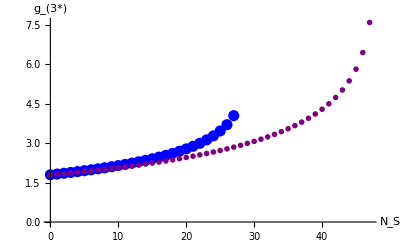

```mathematica
ListPlot[{Table[{i-1,(g3/.FPtabSelect[[i]])[[1]]},{i,1,28}],Table[{i-1,(g3/.FPtabSelectpert[[i]])[[1]]},{i,1,48}]}, LabelStyle->16,PlotStyle->{Directive[Blue, PointSize->0.02], Directive[Purple, PointSize->0.01]}, AxesLabel->{"N_S","g_(3*)"}, LabelStyle->16, AxesStyle->Black]
```

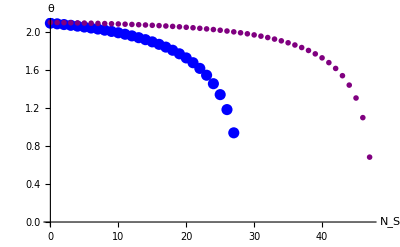

```mathematica
ListPlot[{Table[{i-1,thetatab[[i,1]]},{i,1,28}],Table[{i-1,thetatabpert[[i,1]]},{i,1,48}]}, LabelStyle->16,PlotStyle->{Directive[Blue, PointSize->0.02], Directive[Purple, PointSize->0.01]}, AxesLabel->{"N_S","θ"}, LabelStyle->16, AxesStyle->Black, PlotRange->All]
```

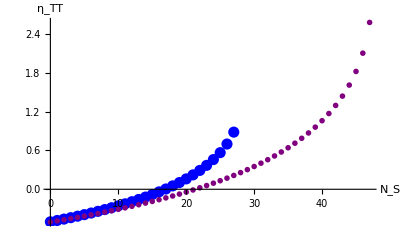

```mathematica
ListPlot[{Table[{i-1,etahtab[[i,1]]},{i,1,28}],Table[{i-1,etahtabpert[[i]]},{i,1,48}]}, LabelStyle->16,PlotStyle->{Directive[Blue, PointSize->0.02], Directive[Purple, PointSize->0.01]}, AxesLabel->{"N_S","η_TT"}, LabelStyle->16, AxesStyle->Black, PlotRange->All]
```

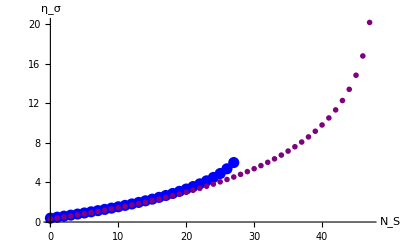

```mathematica
ListPlot[{Table[{i-1,etaσtab[[i,1]]},{i,1,28}],Table[{i-1,etaσtabpert[[i,1]]},{i,1,48}]}, LabelStyle->16,PlotStyle->{Directive[Blue, PointSize->0.02], Directive[Purple, PointSize->0.01]}, AxesLabel->{"N_S","η_σ"}, LabelStyle->16, AxesStyle->Black, PlotRange->All]
```

#### approximation 1: g_5=g_3, g_4=g_3, distinguish G_EH

```mathematica
βgeta2=βgfull/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3}
```

2 g3-(91 g3^2)/(36 π)+(g3^(3/2) √GEH)/(12 π)+(11 g3^2 (16195 GEH^2-1230 g3 GEH Ns+32832 GEH π+10368 g3 Ns π))/(1620 π (-2665 GEH^2+3384 GEH π-124416 π^2))+(7 g3^(3/2) √GEH (16195 GEH^2-1230 g3 GEH Ns+32832 GEH π+10368 g3 Ns π))/(270 π (-2665 GEH^2+3384 GEH π-124416 π^2))-(2 g3 (-1591 GEH^2-750 g3 GEH Ns+55296 GEH π-2592 g3 Ns π))/(2665 GEH^2-3384 GEH π+124416 π^2)-(95 g3^2 (-1591 GEH^2-750 g3 GEH Ns+55296 GEH π-2592 g3 Ns π))/(162 π (2665 GEH^2-3384 GEH π+124416 π^2))-(5 g3^(3/2) √GEH (-1591 GEH^2-750 g3 GEH Ns+55296 GEH π-2592 g3 Ns π))/(54 π (2665 GEH^2-3384 GEH π+124416 π^2))

```mathematica
FPtab=Table[NSolve[(βgeta2/.{Ns->1, GEH->i/10})==0,g3],{i,1,60}]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
FPtabSelect=Table[DeleteCases[Table[If[Abs[Im[g3/.FPtab[[i,j]]]]>0,x,If[(g3/.FPtab[[i,j]])==0,x,If[(g3/.FPtab[[i,j]])>6,x,FPtab[[i,j]]]]],{j,1,Length[FPtab[[i]]]}],x],{i,1,Length[FPtab]}]
```

{{{g3→2.5465}},{{g3→2.63138}},{{g3→2.68997}},{{g3→2.73474}},{{g3→2.77058}},{{g3→2.8}},{{g3→2.82451}},{{g3→2.84509}},{{g3→2.86245}},{{g3→2.87709}},{{g3→2.8894}},{{g3→2.89968}},{{g3→2.90817}},{{g3→2.91509}},{{g3→2.92058}},{{g3→2.92481}},{{g3→2.92787}},{{g3→2.92988}},{{g3→2.93094}},{{g3→2.93111}},{{g3→2.93047}},{{g3→2.92909}},{{g3→2.92701}},{{g3→2.9243}},{{g3→2.921}},{{g3→2.91716}},{{g3→2.9128}},{{g3→2.90797}},{{g3→2.90271}},{{g3→2.89704}},{{g3→2.89099}},{{g3→2.88459}},{{g3→2.87787}},{{g3→2.87085}},{{g3→2.86355}},{{g3→2.85599}},{{g3→2.8482}},{{g3→2.84019}},{{g3→2.83199}},{{g3→2.8236}},{{g3→2.81505}},{{g3→2.80636}},{{g3→2.79753}},{{g3→2.78858}},{{g3→2.77953}},{{g3→2.7704}},{{g3→2.76118}},{{g3→2.75191}},{{g3→2.74258}},{{g3→2.73321}},{{g3→2.72382}},{{g3→2.71441}},{{g3→2.705}},{{g3→2.6956}},{{g3→2.68621}},{{g3→2.67685}},{{g3→2.66752}},{{g3→2.65825}},{{g3→2.64903}},{{g3→2.63987}}}

```mathematica
thetatab=Table[-D[(βgeta2/.{Ns->1, GEH->i/10}),g3]/.FPtabSelect[[i]],{i,1,Length[FPtabSelect]}]
```

{{2.08318},{2.10746},{2.12057},{2.12784},{2.13132},{2.13209},{2.13079},{2.12784},{2.12353},{2.11807},{2.11163},{2.10434},{2.09629},{2.08759},{2.07829},{2.06845},{2.05814},{2.04739},{2.03623},{2.02472},{2.01287},{2.00072},{1.98829},{1.9756},{1.96268},{1.94954},{1.9362},{1.92268},{1.90899},{1.89516},{1.88119},{1.86709},{1.85288},{1.83857},{1.82417},{1.80969},{1.79514},{1.78054},{1.76588},{1.75119},{1.73646},{1.72171},{1.70695},{1.69218},{1.67741},{1.66265},{1.6479},{1.63317},{1.61848},{1.60382},{1.5892},{1.57464},{1.56012},{1.54567},{1.53129},{1.51698},{1.50275},{1.48861},{1.47456},{1.4606}}

```mathematica
etahtab=Table[etah/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3}/.Ns->1/.GEH->i/10/.FPtabSelect[[i]][[1]],{i,1,Length[FPtabSelect]}]
```

{{0.00582173},{-0.0209766},{-0.0481024},{-0.0753902},{-0.102774},{-0.130219},{-0.157701},{-0.185206},{-0.212721},{-0.240236},{-0.267743},{-0.295235},{-0.322705},{-0.350147},{-0.377555},{-0.404925},{-0.432251},{-0.459529},{-0.486753},{-0.51392},{-0.541025},{-0.568063},{-0.595031},{-0.621925},{-0.64874},{-0.675472},{-0.702118},{-0.728673},{-0.755134},{-0.781498},{-0.807759},{-0.833916},{-0.859964},{-0.8859},{-0.911719},{-0.93742},{-0.962998},{-0.98845},{-1.01377},{-1.03896},{-1.06402},{-1.08893},{-1.11371},{-1.13834},{-1.16282},{-1.18715},{-1.21133},{-1.23535},{-1.25921},{-1.28291},{-1.30645},{-1.32981},{-1.35301},{-1.37604},{-1.39889},{-1.42157},{-1.44406},{-1.46638},{-1.48851},{-1.51045}}

```mathematica
etaσtab=Table[etaσ/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3}/.Ns->1/.GEH->i/10/.FPtabSelect[[i]][[1]],{i,1,Length[FPtabSelect]}]
```

{{0.151778},{0.173485},{0.19433},{0.21498},{0.235694},{0.256606},{0.277795},{0.299314},{0.321198},{0.343473},{0.366159},{0.389269},{0.412816},{0.436806},{0.461248},{0.486146},{0.511503},{0.537323},{0.563607},{0.590357},{0.617574},{0.645256},{0.673404},{0.702017},{0.731094},{0.760632},{0.79063},{0.821086},{0.851996},{0.883359},{0.915171},{0.947429},{0.980129},{1.01327},{1.04684},{1.08085},{1.11528},{1.15013},{1.1854},{1.22108},{1.25718},{1.29367},{1.33056},{1.36785},{1.40552},{1.44358},{1.48201},{1.52081},{1.55998},{1.5995},{1.63938},{1.67961},{1.72018},{1.76108},{1.80231},{1.84387},{1.88574},{1.92792},{1.9704},{2.01318}}

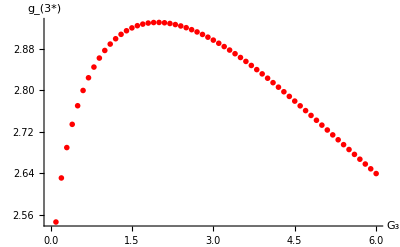

```mathematica
ListPlot[{Table[{i/10,(g3/.FPtabSelect[[i]])[[1]]},{i,1,Length[FPtabSelect]}]}, PlotStyle->{Directive[Red, PointSize->0.01]}, AxesLabel->{"G_3","g_(3*)"}, LabelStyle->16, AxesStyle->Black]
```

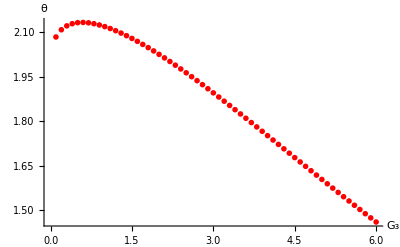

```mathematica
ListPlot[{Table[{i/10,thetatab[[i,1]]},{i,1,Length[FPtabSelect]}]}, PlotStyle->{Directive[Red, PointSize->0.01]}, AxesLabel->{"G_3","θ"}, LabelStyle->16, AxesStyle->Black]
```

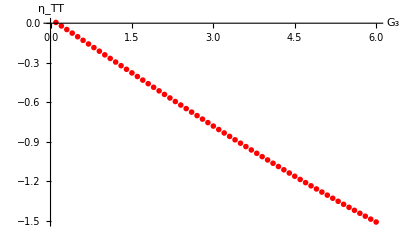

```mathematica
ListPlot[{Table[{i/10,etahtab[[i,1]]},{i,1,Length[FPtabSelect]}]}, PlotStyle->{Directive[Red, PointSize->0.01]}, AxesLabel->{"G_3","η_TT"}, LabelStyle->16, AxesStyle->Black]
```

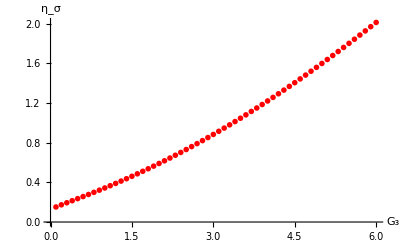

```mathematica
ListPlot[{Table[{i/10,etaσtab[[i,1]]},{i,1,Length[FPtabSelect]}]}, PlotStyle->{Directive[Red, PointSize->0.01]}, AxesLabel->{"G_3","η_σ"}, LabelStyle->16, AxesStyle->Black]
```

#### approximation 1: g_5=g_3, g_4=g_3, distinguish G_EH as function of Ns

```mathematica
βgeta2=βgfull/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3}
```

2 g3-(91 g3^2)/(36 π)+(g3^(3/2) √GEH)/(12 π)+(11 g3^2 (16195 GEH^2-1230 g3 GEH Ns+32832 GEH π+10368 g3 Ns π))/(1620 π (-2665 GEH^2+3384 GEH π-124416 π^2))+(7 g3^(3/2) √GEH (16195 GEH^2-1230 g3 GEH Ns+32832 GEH π+10368 g3 Ns π))/(270 π (-2665 GEH^2+3384 GEH π-124416 π^2))-(2 g3 (-1591 GEH^2-750 g3 GEH Ns+55296 GEH π-2592 g3 Ns π))/(2665 GEH^2-3384 GEH π+124416 π^2)-(95 g3^2 (-1591 GEH^2-750 g3 GEH Ns+55296 GEH π-2592 g3 Ns π))/(162 π (2665 GEH^2-3384 GEH π+124416 π^2))-(5 g3^(3/2) √GEH (-1591 GEH^2-750 g3 GEH Ns+55296 GEH π-2592 g3 Ns π))/(54 π (2665 GEH^2-3384 GEH π+124416 π^2))

```mathematica
FPtabG1=Table[NSolve[(βgeta2/.{Ns->i, GEH->1})==0,g3],{i,1,24}]
```

{{{g3→622.83},{g3→2.14977},{g3→0.}},{{g3→304.573},{g3→2.19749},{g3→0.}},{{g3→198.474},{g3→2.24777},{g3→0.}},{{g3→145.406},{g3→2.30084},{g3→0.}},{{g3→113.544},{g3→2.35698},{g3→0.}},{{g3→92.2835},{g3→2.4165},{g3→0.}},{{g3→77.0781},{g3→2.47977},{g3→0.}},{{g3→65.6551},{g3→2.54722},{g3→0.}},{{g3→56.7517},{g3→2.61934},{g3→0.}},{{g3→49.6098},{g3→2.69672},{g3→0.}},{{g3→43.7468},{g3→2.7801},{g3→0.}},{{g3→38.8405},{g3→2.87031},{g3→0.}},{{g3→34.6676},{g3→2.96844},{g3→0.}},{{g3→31.0677},{g3→3.07581},{g3→0.}},{{g3→27.9227},{g3→3.19412},{g3→0.}},{{g3→25.143},{g3→3.32558},{g3→0.}},{{g3→22.659},{g3→3.47314},{g3→0.}},{{g3→20.4144},{g3→3.64092},{g3→0.}},{{g3→18.3623},{g3→3.83484},{g3→0.}},{{g3→16.4609},{g3→4.06401},{g3→0.}},{{g3→14.6684},{g3→4.34357},{g3→0.}},{{g3→12.9346},{g3→4.70203},{g3→0.}},{{g3→11.175},{g3→5.20594},{g3→0.}},{{g3→9.10949},{g3→6.12047},{g3→0.}}}

```mathematica
FPtabG2=Table[NSolve[(βgeta2/.{Ns->i, GEH->2})==0,g3],{i,1,24}]
```

{{{g3→587.395},{g3→1.75256},{g3→0.}},{{g3→286.954},{g3→1.79253},{g3→0.}},{{g3→186.822},{g3→1.83464},{g3→0.}},{{g3→136.75},{g3→1.8791},{g3→0.}},{{g3→106.696},{g3→1.92613},{g3→0.}},{{g3→86.6458},{g3→1.976},{g3→0.}},{{g3→72.3106},{g3→2.02901},{g3→0.}},{{g3→61.5449},{g3→2.08551},{g3→0.}},{{g3→53.1569},{g3→2.14591},{g3→0.}},{{g3→46.4313},{g3→2.21069},{g3→0.}},{{g3→40.9128},{g3→2.28044},{g3→0.}},{{g3→36.2976},{g3→2.35586},{g3→0.}},{{g3→32.375},{g3→2.4378},{g3→0.}},{{g3→28.9941},{g3→2.52732},{g3→0.}},{{g3→26.0435},{g3→2.62577},{g3→0.}},{{g3→23.4392},{g3→2.73488},{g3→0.}},{{g3→21.1158},{g3→2.85693},{g3→0.}},{{g3→19.0213},{g3→2.99504},{g3→0.}},{{g3→17.1125},{g3→3.15362},{g3→0.}},{{g3→15.3519},{g3→3.33924},{g3→0.}},{{g3→13.704},{g3→3.56237},{g3→0.}},{{g3→12.1299},{g3→3.84144},{g3→0.}},{{g3→10.5745},{g3→4.21461},{g3→0.}},{{g3→8.91491},{g3→4.79056},{g3→0.}}}

```mathematica
FPtabG3=Table[NSolve[(βgeta2/.{Ns->i, GEH->3})==0,g3],{i,1,25}]
```

{{{g3→559.301},{g3→1.38005},{g3→0.}},{{g3→272.993},{g3→1.41203},{g3→0.}},{{g3→177.601},{g3→1.44572},{g3→0.}},{{g3→129.913},{g3→1.48127},{g3→0.}},{{g3→101.297},{g3→1.51885},{g3→0.}},{{g3→82.2132},{g3→1.55868},{g3→0.}},{{g3→68.5736},{g3→1.60098},{g3→0.}},{{g3→58.3343},{g3→1.64601},{g3→0.}},{{g3→50.3603},{g3→1.69409},{g3→0.}},{{g3→43.9702},{g3→1.74559},{g3→0.}},{{g3→38.7304},{g3→1.80094},{g3→0.}},{{g3→34.3517},{g3→1.86065},{g3→0.}},{{g3→30.6336},{g3→1.92535},{g3→0.}},{{g3→27.4327},{g3→1.9958},{g3→0.}},{{g3→24.6432},{g3→2.07297},{g3→0.}},{{g3→22.1856},{g3→2.15807},{g3→0.}},{{g3→19.9982},{g3→2.25265},{g3→0.}},{{g3→18.0323},{g3→2.3588},{g3→0.}},{{g3→16.2482},{g3→2.47935},{g3→0.}},{{g3→14.6125},{g3→2.61837},{g3→0.}},{{g3→13.0951},{g3→2.78193},{g3→0.}},{{g3→11.6669},{g3→2.97982},{g3→0.}},{{g3→10.294},{g3→3.2296},{g3→0.}},{{g3→8.92582},{g3→3.5686},{g3→0.}},{{g3→7.43728},{g3→4.11056},{g3→0.}}}

```mathematica
FPtabG6=Table[NSolve[(βgeta2/.{Ns->i, GEH->6})==0,g3],{i,1,31}]
```

{{{g3→505.527},{g3→0.460866},{g3→0.}},{{g3→246.309},{g3→0.471492},{g3→0.}},{{g3→160.023},{g3→0.482647},{g3→0.}},{{g3→116.926},{g3→0.494373},{g3→0.}},{{g3→91.0894},{g3→0.506715},{g3→0.}},{{g3→73.8772},{g3→0.519728},{g3→0.}},{{g3→61.5896},{g3→0.533471},{g3→0.}},{{g3→52.3779},{g3→0.54801},{g3→0.}},{{g3→45.2152},{g3→0.56342},{g3→0.}},{{g3→39.4859},{g3→0.579789},{g3→0.}},{{g3→34.7981},{g3→0.597213},{g3→0.}},{{g3→30.8908},{g3→0.615807},{g3→0.}},{{g3→27.5831},{g3→0.635701},{g3→0.}},{{g3→24.746},{g3→0.657048},{g3→0.}},{{g3→22.2847},{g3→0.680027},{g3→0.}},{{g3→20.1282},{g3→0.704851},{g3→0.}},{{g3→18.2219},{g3→0.731772},{g3→0.}},{{g3→16.5235},{g3→0.761098},{g3→0.}},{{g3→14.9993},{g3→0.793204},{g3→0.}},{{g3→13.6223},{g3→0.828554},{g3→0.}},{{g3→12.3703},{g3→0.867737},{g3→0.}},{{g3→11.225},{g3→0.911504},{g3→0.}},{{g3→10.1709},{g3→0.96085},{g3→0.}},{{g3→9.19451},{g3→1.01711},{g3→0.}},{{g3→8.28379},{g3→1.08218},{g3→0.}},{{g3→7.42739},{g3→1.15879},{g3→0.}},{{g3→6.61369},{g3→1.25125},{g3→1.25067},{g3→0.}},{{g3→5.82915},{g3→1.36683},{g3→0.}},{{g3→5.05427},{g3→1.51962},{g3→0.}},{{g3→4.24973},{g3→1.74424},{g3→0.}},{{g3→3.24563},{g3→2.20652},{g3→0.}}}

```mathematica
FPtabSelect1=Table[DeleteCases[Table[If[Abs[Im[g3/.FPtabG1[[i,j]]]]>0,x,If[(g3/.FPtabG1[[i,j]])==0,x,If[(g3/.FPtabG1[[i,j]])>8,x,FPtabG1[[i,j]]]]],{j,1,Length[FPtabG1[[i]]]}],x],{i,1,Length[FPtabG1]}]
```

{{{g3→2.14977}},{{g3→2.19749}},{{g3→2.24777}},{{g3→2.30084}},{{g3→2.35698}},{{g3→2.4165}},{{g3→2.47977}},{{g3→2.54722}},{{g3→2.61934}},{{g3→2.69672}},{{g3→2.7801}},{{g3→2.87031}},{{g3→2.96844}},{{g3→3.07581}},{{g3→3.19412}},{{g3→3.32558}},{{g3→3.47314}},{{g3→3.64092}},{{g3→3.83484}},{{g3→4.06401}},{{g3→4.34357}},{{g3→4.70203}},{{g3→5.20594}},{{g3→6.12047}}}

```mathematica
FPtabSelect2=Table[DeleteCases[Table[If[Abs[Im[g3/.FPtabG2[[i,j]]]]>0,x,If[(g3/.FPtabG2[[i,j]])==0,x,If[(g3/.FPtabG2[[i,j]])>8,x,FPtabG2[[i,j]]]]],{j,1,Length[FPtabG2[[i]]]}],x],{i,1,Length[FPtabG2]}]
```

{{{g3→1.75256}},{{g3→1.79253}},{{g3→1.83464}},{{g3→1.8791}},{{g3→1.92613}},{{g3→1.976}},{{g3→2.02901}},{{g3→2.08551}},{{g3→2.14591}},{{g3→2.21069}},{{g3→2.28044}},{{g3→2.35586}},{{g3→2.4378}},{{g3→2.52732}},{{g3→2.62577}},{{g3→2.73488}},{{g3→2.85693}},{{g3→2.99504}},{{g3→3.15362}},{{g3→3.33924}},{{g3→3.56237}},{{g3→3.84144}},{{g3→4.21461}},{{g3→4.79056}}}

```mathematica
FPtabSelect3=Table[DeleteCases[Table[If[Abs[Im[g3/.FPtabG3[[i,j]]]]>0,x,If[(g3/.FPtabG3[[i,j]])==0,x,If[(g3/.FPtabG3[[i,j]])>7,x,FPtabG3[[i,j]]]]],{j,1,Length[FPtabG3[[i]]]}],x],{i,1,Length[FPtabG3]}]
```

{{{g3→1.38005}},{{g3→1.41203}},{{g3→1.44572}},{{g3→1.48127}},{{g3→1.51885}},{{g3→1.55868}},{{g3→1.60098}},{{g3→1.64601}},{{g3→1.69409}},{{g3→1.74559}},{{g3→1.80094}},{{g3→1.86065}},{{g3→1.92535}},{{g3→1.9958}},{{g3→2.07297}},{{g3→2.15807}},{{g3→2.25265}},{{g3→2.3588}},{{g3→2.47935}},{{g3→2.61837}},{{g3→2.78193}},{{g3→2.97982}},{{g3→3.2296}},{{g3→3.5686}},{{g3→4.11056}}}

```mathematica
FPtabSelect6=Table[DeleteCases[Table[If[Abs[Im[g3/.FPtabG6[[i,j]]]]>0,x,If[(g3/.FPtabG6[[i,j]])==0,x,If[(g3/.FPtabG6[[i,j]])>3,x,FPtabG6[[i,j]]]]],{j,1,Length[FPtabG6[[i]]]}],x],{i,1,Length[FPtabG6]}]
```

{{{g3→0.460866}},{{g3→0.471492}},{{g3→0.482647}},{{g3→0.494373}},{{g3→0.506715}},{{g3→0.519728}},{{g3→0.533471}},{{g3→0.54801}},{{g3→0.56342}},{{g3→0.579789}},{{g3→0.597213}},{{g3→0.615807}},{{g3→0.635701}},{{g3→0.657048}},{{g3→0.680027}},{{g3→0.704851}},{{g3→0.731772}},{{g3→0.761098}},{{g3→0.793204}},{{g3→0.828554}},{{g3→0.867737}},{{g3→0.911504}},{{g3→0.96085}},{{g3→1.01711}},{{g3→1.08218}},{{g3→1.15879}},{{g3→1.25125},{g3→1.25067}},{{g3→1.36683}},{{g3→1.51962}},{{g3→1.74424}},{{g3→2.20652}}}

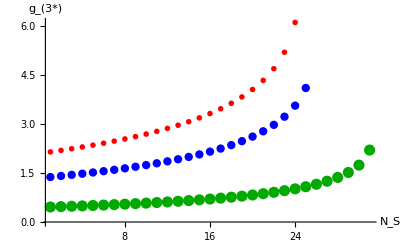

```mathematica
ListPlot[{Table[{i,g3/.FPtabSelect1[[i,1]]},{i,1,Length[FPtabSelect1]}],(*Table[{i,g3/.FPtabSelect2[[i,1]]},{i,1,Length[FPtabSelect2]-4}],*)Table[{i,g3/.FPtabSelect3[[i,1]]},{i,1,Length[FPtabSelect3]}],Table[{i,g3/.FPtabSelect6[[i,1]]},{i,1,Length[FPtabSelect6]}]}, PlotRange->All, AxesLabel->{"N_S","g_(3*)"}, LabelStyle->16, PlotStyle->{Directive[Red, PointSize->0.01],Directive[Blue, PointSize->0.015],Directive[Darker[Green], PointSize->0.02]},AxesStyle->Black]
```

```mathematica
thetatab1=Table[-D[(βgeta2/.{Ns->i, GEH->1}),g3]/.FPtabSelect1[[i]],{i,1,Length[FPtabSelect1]}]
```

{{1.72759},{1.72118},{1.71418},{1.70651},{1.69809},{1.68882},{1.67858},{1.66723},{1.65462},{1.64054},{1.62476},{1.60697},{1.58679},{1.56375},{1.53723},{1.50639},{1.47011},{1.42678},{1.37405},{1.30819},{1.22291},{1.10605},{0.928469},{0.570577}}

```mathematica
thetatab3=Table[-D[(βgeta2/.{Ns->i, GEH->3}),g3]/.FPtabSelect3[[i]],{i,1,Length[FPtabSelect3]}]
```

{{1.17753},{1.17437},{1.17091},{1.1671},{1.1629},{1.15826},{1.15312},{1.14742},{1.14106},{1.13396},{1.12598},{1.11697},{1.10677},{1.09513},{1.08176},{1.06627},{1.04818},{1.02677},{1.0011},{0.969739},{0.930513},{0.879805},{0.81095},{0.709305},{0.528681}}

```mathematica
thetatab6=Table[-D[(βgeta2/.{Ns->i, GEH->6}),g3]/.FPtabSelect6[[i]],{i,1,Length[FPtabSelect6]}]
```

{{0.432489},{0.431968},{0.431402},{0.430786},{0.430113},{0.429376},{0.428569},{0.427682},{0.426705},{0.425627},{0.424432},{0.423104},{0.421624},{0.419968},{0.418106},{0.416004},{0.413619},{0.410897},{0.407769},{0.404148},{0.399922},{0.394937},{0.388989},{0.381787},{0.372912},{0.36172},{0.347171,0.346926},{0.32742},{0.298726},{0.251421},{0.136174}}

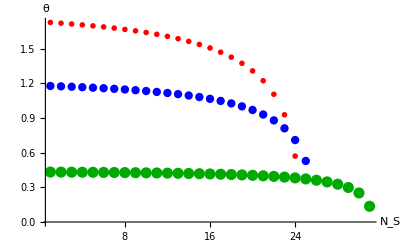

```mathematica
ListPlot[{Table[{i,thetatab1[[i,1]]},{i,1,Length[thetatab1]}],Table[{i,thetatab3[[i,1]]},{i,1,Length[thetatab3]}],Table[{i,thetatab6[[i,1]]},{i,1,Length[thetatab6]}]}, PlotRange->All, AxesLabel->{"N_S","θ"}, LabelStyle->16, PlotStyle->{Directive[Red, PointSize->0.01],Directive[Blue, PointSize->0.015],Directive[Darker[Green], PointSize->0.02]},AxesStyle->Black]
```

```mathematica
etahtab1=Table[etah/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3}/.Ns->i/.GEH->1/.FPtabSelect1[[i]],{i,1,Length[FPtabSelect1]}]
```

{{{-0.25084}},{{-0.218107}},{{-0.18387}},{{-0.148005}},{{-0.110369}},{{-0.0707998}},{{-0.0291125}},{{0.0149065}},{{0.0615055}},{{0.110976}},{{0.163661}},{{0.219976}},{{0.28042}},{{0.345612}},{{0.416327}},{{0.493558}},{{0.578615}},{{0.673278}},{{0.780076}},{{0.902806}},{{1.04765}},{{1.22594}},{{1.46346}},{{1.85936}}}

```mathematica
etahtab3=Table[etah/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3}/.Ns->i/.GEH->3/.FPtabSelect3[[i]],{i,1,Length[FPtabSelect3]}]
```

{{{-0.807343}},{{-0.782741}},{{-0.756962}},{{-0.729908}},{{-0.701469}},{{-0.671521}},{{-0.639921}},{{-0.606506}},{{-0.57109}},{{-0.533453}},{{-0.493341}},{{-0.45045}},{{-0.40442}},{{-0.354812}},{{-0.301087}},{{-0.242573}},{{-0.178411}},{{-0.107479}},{{-0.0282665}},{{0.0613445}},{{0.164472}},{{0.286044}},{{0.43469}},{{0.628329}},{{0.919969}}}

```mathematica
etahtab6=Table[etah/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3}/.Ns->i/.GEH->6/.FPtabSelect6[[i]],{i,1,Length[FPtabSelect6]}]
```

{{{-1.55418}},{{-1.5445}},{{-1.53437}},{{-1.52374}},{{-1.51259}},{{-1.50085}},{{-1.48849}},{{-1.47545}},{{-1.46167}},{{-1.44708}},{{-1.4316}},{{-1.41514}},{{-1.39759}},{{-1.37884}},{{-1.35874}},{{-1.33712}},{{-1.31379}},{{-1.28852}},{{-1.261}},{{-1.2309}},{{-1.19776}},{{-1.16102}},{{-1.11996}},{{-1.07358}},{{-1.02053}},{{-0.95884}},{{-0.885492},{-0.885807}},{{-0.795443}},{{-0.679103}},{{-0.513388}},{{-0.19081}}}

```mathematica
etaσtab1=Table[etaσ/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3}/.Ns->i/.GEH->1/.FPtabSelect1[[i]],{i,1,Length[FPtabSelect1]}]
```

{{{0.306102}},{{0.421465}},{{0.542126}},{{0.668527}},{{0.80117}},{{0.940625}},{{1.08755}},{{1.24268}},{{1.40691}},{{1.58126}},{{1.76695}},{{1.96542}},{{2.17845}},{{2.40821}},{{2.65743}},{{2.92962}},{{3.22939}},{{3.56301}},{{3.93941}},{{4.37195}},{{4.88242}},{{5.5108}},{{6.3479}},{{7.74316}}}

```mathematica
etaσtab3=Table[etaσ/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3}/.Ns->i/.GEH->3/.FPtabSelect3[[i]],{i,1,Length[FPtabSelect3]}]
```

{{{0.811535}},{{0.879904}},{{0.951544}},{{1.02673}},{{1.10576}},{{1.18898}},{{1.2768}},{{1.36966}},{{1.46808}},{{1.57267}},{{1.68414}},{{1.80334}},{{1.93125}},{{2.06911}},{{2.21841}},{{2.38102}},{{2.55933}},{{2.75645}},{{2.97658}},{{3.22561}},{{3.5122}},{{3.85004}},{{4.26313}},{{4.80125}},{{5.61171}}}

```mathematica
etaσtab6=Table[etaσ/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3}/.Ns->i/.GEH->6/.FPtabSelect6[[i]],{i,1,Length[FPtabSelect6]}]
```

{{{1.92605}},{{1.94533}},{{1.96552}},{{1.98669}},{{2.00893}},{{2.03231}},{{2.05694}},{{2.08292}},{{2.11038}},{{2.13945}},{{2.1703}},{{2.2031}},{{2.23806}},{{2.27543}},{{2.31548}},{{2.35855}},{{2.40504}},{{2.4554}},{{2.51023}},{{2.57021}},{{2.63624}},{{2.70944}},{{2.79126}},{{2.88368}},{{2.98938}},{{3.1123}},{{3.25845},{3.25783}},{{3.43788}},{{3.6697}},{{3.9999}},{{4.64265}}}

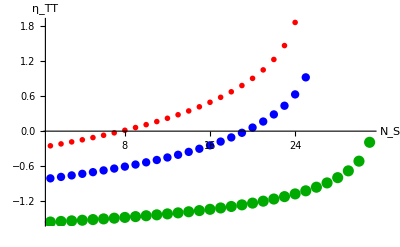

```mathematica
ListPlot[{Table[{i,etahtab1[[i,1,1]]},{i,1,Length[thetatab1]}],Table[{i,etahtab3[[i,1,1]]},{i,1,Length[thetatab3]}],Table[{i,etahtab6[[i,1,1]]},{i,1,Length[thetatab6]}]}, PlotRange->All, AxesLabel->{"N_S","η_TT"}, LabelStyle->16, PlotStyle->{Directive[Red, PointSize->0.01],Directive[Blue, PointSize->0.015],Directive[Darker[Green], PointSize->0.02]},AxesStyle->Black]
```

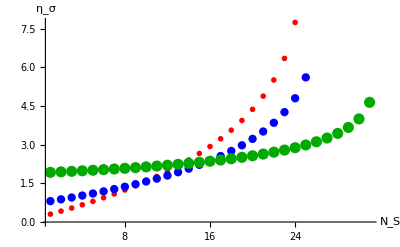

```mathematica
ListPlot[{Table[{i,etaσtab1[[i,1,1]]},{i,1,Length[thetatab1]}],Table[{i,etaσtab3[[i,1,1]]},{i,1,Length[thetatab3]}],Table[{i,etaσtab6[[i,1,1]]},{i,1,Length[thetatab6]}]}, PlotRange->All, AxesLabel->{"N_S","η_σ"}, LabelStyle->16, PlotStyle->{Directive[Red, PointSize->0.01],Directive[Blue, PointSize->0.015],Directive[Darker[Green], PointSize->0.02]},AxesStyle->Black]
```

#### approximation 1: g_5=g_3, g_4=g_3, G_EH=g_3, add background beta functions

```mathematica
betagback=2G-G^2/π(15/8-5 ηh/18+ησ/24-Ns/24(4))
```

2 G-(G^2 (15/8-Ns/6-(5 ηh)/18+ησ/24))/π

```mathematica
backgroundtab=Table[Solve[(betagback/.{Ns->i,ηh->etahtab[[i]], ησ->etaσtab[[i]]})==0,G][[2]],{i,1,14}]
```

{{G→3.3701},{G→3.70449},{G→4.11277},{G→4.62247},{G→5.27678},{G→6.14748},{G→7.36324},{G→9.18},{G→12.19},{G→18.1443},{G→35.5012},{G→837.183},{G→0.+0. ⅈ},{G→0.+0. ⅈ}}

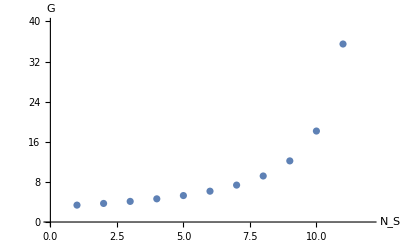

```mathematica
ListPlot[Table[{i,G/.backgroundtab[[i]]},{i,1,Length[backgroundtab]-2}], AxesLabel->{"N_S","G"}, LabelStyle->16, AxesStyle->Thick]
```

```mathematica
FPtabSelect=Table[DeleteCases[Table[If[Abs[Im[g3/.FPtab[[i,j]]]]>0,x,If[(g3/.FPtab[[i,j]])==0,x,If[(g3/.FPtab[[i,j]])>6,x,FPtab[[i,j]]]]],{j,1,4}],x],{i,1,Length[FPtab]}]
```

{{{g3→2.90257}},{{g3→2.9894}},{{g3→3.08365}},{{g3→3.18654}},{{g3→3.29963}},{{g3→3.42494}},{{g3→3.56512}},{{g3→3.72385}},{{g3→3.90632}},{{g3→4.12032}},{{g3→4.37837}},{{g3→4.7026}},{{g3→5.13905}},{{g3→5.81836}},{},{},{},{},{{g3→-4498.58}},{{g3→-1127.85}}}

```mathematica
thetatab=Table[-D[(βgeta2/.Ns->i),g3]/.FPtabSelect[[i]],{i,1,14}]
```

{{2.01329},{1.99225},{1.96845},{1.94137},{1.91034},{1.87446},{1.83254},{1.78293},{1.72326},{1.64993},{1.5571},{1.43438},{1.26004},{0.972356}}

```mathematica
etahtab=Table[etah/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}/.Ns->i/.FPtabSelect[[i]][[1]],{i,1,14}]
```

{{-0.755812},{-0.726251},{-0.69452},{-0.660293},{-0.623156},{-0.582582},{-0.537881},{-0.488118},{-0.431979},{-0.367529},{-0.291709},{-0.199195},{-0.0791416},{0.0985029}}

```mathematica
etaσtab=Table[etaσ/.etasol/.{G3->GEH, G4->GEH}/.{g5->g3,g4->g3,GEH->g3}/.Ns->i/.FPtabSelect[[i]][[1]],{i,1,14}]
```

{{0.852796},{1.02597},{1.20982},{1.40581},{1.61569},{1.84171},{2.08675},{2.35463},{2.65061},{2.98231},{3.36141},{3.80775},{4.3605},{5.12402}}

```mathematica
etas/.{ηh->-0.76 ,ησ->0.85, ηs->0, g4->g3}/.g3->2.9
```

1.77793

```mathematica
etas/.{ηh->-0.73 ,ησ->1.03, ηs->0, g4->g3}/.g3->2.99
```

1.83072

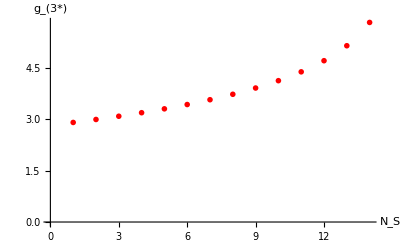

```mathematica
ListPlot[{Table[(g3/.FPtabSelect[[i]])[[1]],{i,1,14}]}, PlotStyle->{Directive[Red, PointSize->0.01]}, AxesLabel->{"N_S","g_(3*)"}, LabelStyle->16, AxesStyle->Black]
```

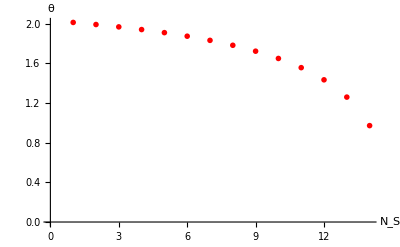

```mathematica
ListPlot[{Table[thetatab[[i,1]],{i,1,14}]}, PlotStyle->{Directive[Red, PointSize->0.01]}, AxesLabel->{"N_S","θ"}, LabelStyle->16, AxesStyle->Black]
```

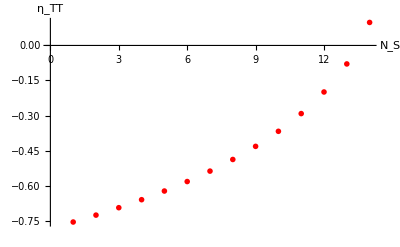

```mathematica
ListPlot[{Table[etahtab[[i,1]],{i,1,14}]}, PlotStyle->{Directive[Red, PointSize->0.01]}, AxesLabel->{"N_S","η_TT"}, LabelStyle->16, AxesStyle->Black]
```

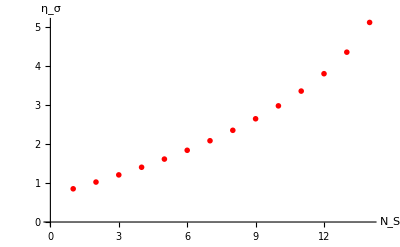

```mathematica
ListPlot[{Table[etaσtab[[i,1]],{i,1,14}]}, PlotStyle->{Directive[Red, PointSize->0.01]}, AxesLabel->{"N_S","η_σ"}, LabelStyle->16, AxesStyle->Black]
```